# TensoriaCalc: User’s Guide Introduction through examples

## Welcome

Welcome, and thanks for downloading TensoriaCalc!

TensoriaCalc is a package that computes – within a Riemannian geometry framework (i.e., no torsion) – the Christoffel symbols, Riemann tensor, Ricci tensor, Ricci scalar, Einstein tensor, etc., once a metric and a coordinate system is specified. Arbitrary space(time) tensors may also be readily defined; and other operations such as coordinate transformations, covariant derivatives, Lie derivatives, Hodge duals, etc. may too be performed. This User’s Guide walks you through key features of TensoriaCalc via concrete examples. (More details can be found in the accompanying TensoriaCalc manual.) Basic knowledge of the Wolfram Language and differential geometry is assumed.

Please feel free to write if you have suggestions, comments, questions, bug reports, etc. If you ever use this software for education purposes or scientific research, please do cite arXiv:2512.18796 and the following URLs

	https://github.com/tensoria/TensoriaCalc
	https://www.stargazing.net/yizen/Tensoria.html

	- Wei-Hao Chen, Yi-Zen Chu, and Vaidehi Varma
	tensoria [dot] wolfram [at] gmail [dot] com
	December 2025

### Package Directory

Enter the directory where TensoriaCalc.m can be found

```mathematica
<<"C:\TensoriaCalc.m";
```

## Geometric Objects and Operations: Definitions

We start by collecting the definitions of the various geometry-related objects and operations carried out by TensoriaCalc.

We employ Einstein's summation convention, whereby repeated indices are assumed to be summed over. In this notebook we shall adhere to the convention that Greek indices start at zero (the time coordinate) followed by the spatial ones over {1,...,D=d-1}; where D is the dimension of space and d is that of spacetime. Latin/English alphabets run over only over the spatial dimensions {1,...,D}. Of course, when using TensoriaCalc, the user is free to use whatever notation she desires.

The orthonormal frame field (ε^(α̂))_μ and its inverse (ε_(α̂))^μ are defined are defined through their relation to the metric itself:
	η_(α̂ β̂) (ε^(α̂))_μ (ε^(β̂))_ν = g_μν and η^(α̂ β̂) (ε_(α̂))^μ (ε_(β̂))^ν = g^μν,
where η_(α̂ β̂) is the flat space(time) metric.

The Christoffel symbols are: (Γ^α)_μν≡(1/2)g^αλ(∂_μ g_νλ+∂_ν g_μλ-∂_λ g_μν).

The covariant derivative of a vector V is ∇_α V^γ=∂_α V^γ+(Γ^γ)_αβ V^β and that of a 1-form A is ∇_α A_β=∂_α A_β-(Γ^γ)_αβ A_γ.

The Riemann curvature tensor is: (R^α)_βμν≡∂_μ (Γ^α)_νβ-∂_ν (Γ^α)_μβ+(Γ^α)_σμ(Γ^σ)_νβ-(Γ^α)_σν(Γ^σ)_μβ.

The Ricci tensor is: R_βν≡(R^α)_βαν.

The Ricci scalar is: R≡g^αβ R_αβ.

The Hodge dual of a rank N ≤ d tensor T in d dimensional space(time) is (★T)^(μ_1... μ_(d-N))≡(T̃)^(μ_1... μ_(d-N))≡(1/N!)(ϵ̃)^(μ_1... μ_(d-N)ν_1... ν_N)T_(ν_1... ν_N).

Here, the covariant Levi-Civita pseudo-tensor itself is defined as (ϵ̃)_(μ_1... μ_d)≡|g|^(1/2)ϵ_(μ_1... μ_d), where |g|^(1/2) is the square root of the absolute value of the metric determinant; and the ϵ_(μ_1... μ_d) is the fully anti-symmetric Levi-Civita symbol, with ϵ_((0)(1) ... (d-1)) ≡ 1.

The Lie derivative of a vector V along a vector W is (£_W V)^α=W^β∂_β V^α-V^β∂_β W^α and that of a 1-form A is (£_W A)_α=W^β∂_β A_α+A_β∂_α W^β.

The exterior derivative on an N-form B_(μ_1... μ_N) is (ⅆB)_(νμ_1... μ_N)=1/(N!)∂_([ν) B_(μ_1... μ_N]), where the square bracket denotes anti-symmetrization.

We denote index symmetrization and anti-symmetrization with {} and []. For example, T_{αβγ}=T_αβγ+T_αγβ+T_βαγ+T_βγα+T_γβα+T_γαβ, and T_[αβγ]=T_αβγ-T_αγβ-T_βαγ+T_βγα-T_γβα+T_γαβ.

## Defining the metric, other tensors

One of the key aspects of the Wolfram language is its symbolic computation ability. There is no programming overhead spent in terms of variable(s) declaration. Together with Mathematica’s multitude of in-built functions, this means mathematical calculations can often be accomplished with a single or few lines of code. For instance, one may perform an indefinite integral, say sin x with respect to x —

```mathematica
Integrate[Sin[x],x]
```

-Cos[x]

— without having to declare the integration variable x. (Strictly speaking, x and the abstract variables used in this notebook should be identified in the Wolfram Language as Symbol’s, in that MatchQ[x,_Symbol] = True or, equivalently, Head[x] = Symbol.) Let us now illustrate how this straightforward style of symbolic computation works similarly for TensoriaCalc, by defining the metric tensor — the primary object in most differential geometry calculations.

Round 2-Sphere

In TensoriaCalc, an arbitrary metric tensor may be defined by specifying its indices, explicit components, and the associated coordinate system. For example, the round 2-sphere geometry with the usual spherical coordinates {0 ≤ θ ≤ π, 0 ≤ ϕ < 2π} is defined either by the sum of squares of infinitesimal displacements — namely, superposition of (ⅆθ)^2 = DifferentialD[θ]^2 and (ⅆϕ)^2 = DifferentialD[ϕ]^2 — or by its matrix representation. (The ⅆ can be entered via the keystrokes Esc dd Esc.)

```mathematica
g2Sphere=Metric[SubMinus[a],SubMinus[b],(ⅆθ)^2+Sin[θ]^2(ⅆϕ)^2,Coordinates->{θ,ϕ},StartIndex->1,TensorAssumption->{0<=θ<=Pi,0<=ϕ<2Pi}]
g2Sphere===Metric[SubMinus[a],SubMinus[b],({{1, 0}, {0, Sin[θ]^2}}),Coordinates->{θ,ϕ},StartIndex->1,TensorAssumption->{0<=θ<=Pi,0<=ϕ<2Pi}]
```

g
a
b

True

The same geometry may also be defined through the inverse metric, as a sum over the squares of the partial derivatives — namely, superposition of (∇θ)^2=Del[θ]^2 (≡∂_θ ⊗∂_θ ) and (∇ϕ)^2=Del[ϕ]^2 (≡∂_ϕ ⊗∂_ϕ ) — or by its matrix representation.

```mathematica
gInverse2Sphere=Metric[SuperMinus[a],SuperMinus[b],(∇θ)^2+(∇ϕ)^2/Sin[θ]^2,Coordinates->{θ,ϕ},StartIndex->1,TensorAssumption->{0≤θ≤Pi,0≤ϕ<2Pi}]
gInverse2Sphere===Metric[SuperMinus[a],SuperMinus[b],({{1, 0}, {0, 1/Sin[θ]^2}}),Coordinates->{θ,ϕ},StartIndex->1,TensorAssumption->{0≤θ≤Pi,0≤ϕ<2Pi}]
```

ga
b

True

Above, the a and b indices cannot belong to the given coordinate system but are otherwise arbitrary Symbol’s. The SubMinus notation, SubMinus[a] = a_- and SubMinus[b] = b_-, indicates they are lower indices; while the SuperMinus notation, SuperMinus[a] = a^- and SuperMinus[b] = b^-, indicates they are upper indices.

The StartIndex and TensorAssumption Rule’s are optional arguments; with default values given by StartIndex → 0 and TensorAssumption → {}. Our notation here follows that of the Wolfram Language, where optional arguments are Rule’s, with a predefined default value. In our online manual, whenever a default value for a function argument is given, that means the argument in question is an optional one. Note, however, even though Coordinates looks like an optional argument, it is actually mandatory.

StartIndex refers to the integer associated with the first coordinate. For example, in the flat spacetime (ⅆs)^2 = (ⅆt)^2- ⅆx⃗·ⅆx⃗, it is common practice to let the time t be not only the leading coordinate, but also labeled as t = x^0; while x^i = (x^1,⋯,x^D) are the spatial ones (where D is the dimension of space). For the 2-sphere metric at hand, StartIndex → 1 means (x^1,x^2) = (θ,ϕ).

TensorAssumption allows the user to record properties of the parameters occurring within the metric components, which may then be invoked when, applying Simplify or FullSimplify on expressions.

Other optional arguments associated with Metric are described in the online manual; which shall be released in the near future.

Lastly, you may want to hover your mouse cursor over the g_ab. By default, in TensoriaCalc, rank 0, 1 and 2 tensors will have their components and coordinates displayed whenever the mouse cursor hovers over them.

Once a metric (or the inverse metric) has been defined, its inverse (or the metric) can be readily obtained by feeding it back into the Metric function.

```mathematica
Metric[SuperMinus[a],SuperMinus[b],g2Sphere]
Metric[SubMinus[a],SubMinus[b],gInverse2Sphere]
```

ga
b

g
a
b

Upon entering the metric and the coordinates through Metric, TensoriaCalc then outputs a Tensor object with arguments consisting of Rule’s containing the metric components, indices, coordinates, Christoffel symbols, Ricci scalar, Ricci tensor and Riemann tensor, etc. — see below. TensoriaCalc has built in functions to extract these geometric information. This allows for different geometries to be defined and computed within the same Mathematica session.

Specifically, the g2Sphere reads as follows.

```mathematica
g2Sphere//FullForm
```

Tensor[Rule[ChristoffelComponents,List[Rule[ChristoffelComponents[SuperMinus[1],SubMinus[1],SubMinus[1]],0],Rule[ChristoffelComponents[SuperMinus[1],SubMinus[1],SubMinus[2]],0],Rule[ChristoffelComponents[SuperMinus[1],SubMinus[2],SubMinus[1]],0],Rule[ChristoffelComponents[SuperMinus[1],SubMinus[2],SubMinus[2]],Times[-1,Cos[\[Theta]],Sin[\[Theta]]]],Rule[ChristoffelComponents[SuperMinus[2],SubMinus[1],SubMinus[1]],0],Rule[ChristoffelComponents[SuperMinus[2],SubMinus[1],SubMinus[2]],Cot[\[Theta]]],Rule[ChristoffelComponents[SuperMinus[2],SubMinus[2],SubMinus[1]],Cot[\[Theta]]],Rule[ChristoffelComponents[SuperMinus[2],SubMinus[2],SubMinus[2]],0]]],Rule[Coordinates,List[\[Theta],\[Phi]]],Rule[FlatMetric,Null],Rule[Indices,List[SubMinus[a],SubMinus[b]]],Rule[InverseOrthonormalFrameField,Null],Rule[MetricDeterminant,Power[Sin[\[Theta]],2]],Rule[OrthonormalFrameField,Null],Rule[OrthonormalFrameFieldIndices,Null],Rule[OrthonormalFrameFieldOperator,Simplify],Rule[RicciComponents,List[Rule[RicciComponents[SubMinus[1],SubMinus[1]],1],Rule[RicciComponents[SubMinus[1],SubMinus[2]],0],Rule[RicciComponents[SubMinus[2],SubMinus[1]],0],Rule[RicciComponents[SubMinus[2],SubMinus[2]],Power[Sin[\[Theta]],2]]]],Rule[RicciScalarInvariant,List[Rule[RicciScalar,2]]],Rule[RiemannComponents,List[Rule[RiemannComponents[SuperMinus[1],SubMinus[1],SubMinus[1],SubMinus[1]],0],Rule[RiemannComponents[SuperMinus[1],SubMinus[2],SubMinus[1],SubMinus[1]],0],Rule[RiemannComponents[SuperMinus[2],SubMinus[1],SubMinus[1],SubMinus[1]],0],Rule[RiemannComponents[SuperMinus[2],SubMinus[2],SubMinus[1],SubMinus[1]],0],Rule[RiemannComponents[SuperMinus[1],SubMinus[1],SubMinus[1],SubMinus[2]],0],Rule[RiemannComponents[SuperMinus[1],SubMinus[2],SubMinus[1],SubMinus[2]],Power[Sin[\[Theta]],2]],Rule[RiemannComponents[SuperMinus[2],SubMinus[1],SubMinus[1],SubMinus[2]],-1],Rule[RiemannComponents[SuperMinus[2],SubMinus[2],SubMinus[1],SubMinus[2]],0],Rule[RiemannComponents[SuperMinus[1],SubMinus[1],SubMinus[2],SubMinus[1]],0],Rule[RiemannComponents[SuperMinus[1],SubMinus[2],SubMinus[2],SubMinus[1]],Times[-1,Power[Sin[\[Theta]],2]]],Rule[RiemannComponents[SuperMinus[2],SubMinus[1],SubMinus[2],SubMinus[1]],1],Rule[RiemannComponents[SuperMinus[2],SubMinus[2],SubMinus[2],SubMinus[1]],0],Rule[RiemannComponents[SuperMinus[1],SubMinus[1],SubMinus[2],SubMinus[2]],0],Rule[RiemannComponents[SuperMinus[1],SubMinus[2],SubMinus[2],SubMinus[2]],0],Rule[RiemannComponents[SuperMinus[2],SubMinus[1],SubMinus[2],SubMinus[2]],0],Rule[RiemannComponents[SuperMinus[2],SubMinus[2],SubMinus[2],SubMinus[2]],0]]],Rule[StartIndex,1],Rule[TensorAssumption,List[LessEqual[0,\[Theta],Pi],Inequality[0,LessEqual,\[Phi],Less,Times[2,Pi]]]],Rule[TensorComponents,List[List[1,0],List[0,Power[Sin[\[Theta]],2]]]],Rule[TensorName,"g"],Rule[TensorOperator,Simplify],Rule[TensorType,"Metric"],Rule[TooltipDisplay,Null],Rule[TooltipStyle,List[]]]

This is analogous to, say, the output of any graphics related function in the Wolfram Language; where a Graphics object is generated, with its arguments containing the (text-based) relevant information that would allow Mathematica to display it correctly. For example,

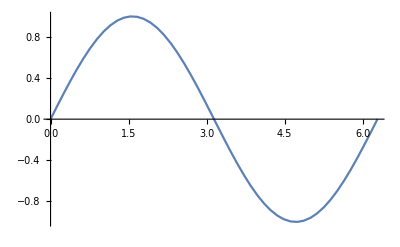

Graphics[List[List[List[List[],List[],Annotation[List[Directive[Opacity[1.],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],Line[List[List[1.28228×10^-7,1.28228×10^-7],List[0.123331,0.123018],List[0.257035,0.254214],List[0.381879,0.372665],List[0.504274,0.483172],List[0.637043,0.594821],List[0.760951,0.68961],List[0.895233,0.780355],List[1.02707,0.855785],List[1.15004,0.91278],List[1.28339,0.958981],List[1.40787,0.986757],List[1.52991,0.999164],List[1.66232,0.995814],List[1.78587,0.97696],List[1.9198,0.939714],List[2.05128,0.886774],List[2.17389,0.823584],List[2.30688,0.741103],List[2.43101,0.652275],List[2.56551,0.54474],List[2.69757,0.429578],List[2.82076,0.315355],List[2.95433,0.186171],List[3.07904,0.0625152],List[3.2013,-0.0596671],List[3.33393,-0.191151],List[3.4577,-0.310869],List[3.59185,-0.435193],List[3.72354,-0.549654],List[3.84638,-0.647871],List[3.97959,-0.743305],List[4.10394,-0.820535],List[4.22584,-0.883952],List[4.35812,-0.937899],List[4.48153,-0.97347],List[4.61532,-0.995292],List[4.74025,-0.999612],List[4.86273,-0.988721],List[4.99558,-0.960169],List[5.11957,-0.91824],List[5.25394,-0.85691],List[5.38586,-0.781663],List[5.50892,-0.699195],List[5.64235,-0.597868],List[5.76692,-0.493638],List[5.88904,-0.38402],List[6.02154,-0.258675],List[6.14517,-0.137577],List[6.28319,-1.28228×10^-7]]]],"Charting`Private`Tag$1653#1"]]],List[]],List[Rule[DisplayFunction,Identity],Rule[Ticks,List[Automatic,Automatic]],Rule[AxesOrigin,List[0,0]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[DisplayFunction,Identity],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.05],Scaled[0.05]]]],Rule[PlotRangeClipping,True],Rule[ImagePadding,All],Rule[DisplayFunction,Identity],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[Method,List[Rule["DefaultBoundaryStyle",Automatic],Rule["DefaultGraphicsInteraction",List[Rule["Version",1.2],Rule["TrackMousePosition",List[True,False]],Rule["Effects",List[Rule["Highlight",List[Rule["ratio",2]]],Rule["HighlightPoint",List[Rule["ratio",2]]],Rule["Droplines",List[Rule["freeformCursorMode",True],Rule["placement",List[Rule["x","All"],Rule["y","None"]]]]]]]]],Rule["DefaultMeshStyle",AbsolutePointSize[6]],Rule["ScalingFunctions",None],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[All,All]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[Ticks,List[Automatic,Automatic]]]]

```mathematica
Plot[Sin[x],{x,0,2Pi},PlotRange->All,PlotPoints->50,MaxRecursion->0]
%//FullForm
```

To extract the information stored within the metric Tensor object g2Sphere, we simply apply to it the associated functions: Indices, Coordinates, Christoffel, Riemann, Ricci, RicciScalar and the (metric) Determinant.

```mathematica
Indices[g2Sphere]
```

{a_-,b_-}

```mathematica
Coordinates[g2Sphere]
```

{θ,ϕ}

```mathematica
Christoffel[SuperMinus[a],SubMinus[m],SubMinus[n],g2Sphere]
```

Γa

m
n

```mathematica
Riemann[SuperMinus[a],SubMinus[b],SubMinus[m],SubMinus[n],g2Sphere]
Riemann[SuperMinus[a],SuperMinus[b],SubMinus[m],SubMinus[n],g2Sphere]
```

Ra

b
m
n

Ra
b

m
n

```mathematica
Ricci[SuperMinus[a],SubMinus[b],g2Sphere]
Ricci[SuperMinus[a],SuperMinus[b],g2Sphere]
```

Ra

b

Ra
b

```mathematica
RicciScalar[g2Sphere]
```

2

```mathematica
Determinant[g2Sphere]
```

Sin[θ]^2

TensorComponents applied to any Tensor object returns its components, usually a List. For instance, the components of the metric or inverse metric expressed as a square matrix (List of List’s) can themselves be extracted with TensorComponents.

```mathematica
Metric[SubMinus[a],SubMinus[b],gInverse2Sphere]//TensorComponents
Metric[SuperMinus[a],SuperMinus[b],g2Sphere]//TensorComponents
Metric[SubMinus[a],SuperMinus[b],g2Sphere]//TensorComponents
```

{{1,0},{0,Sin[θ]^2}}

{{1,0},{0,Csc[θ]^2}}

{{1,0},{0,1}}

The 2-sphere is a maximally symmetric spacetime with three Killing vectors — the maximum allowed for a two-dimensional (2D) space. One feature of such a spacetime is that its Riemann tensor can be constructed from a tensor product of the metric: R_abmn = (R/2)(g_(a[m)g_(n]b)), where [mn] denotes antisymmetrization; for e.g., T_[mn]≡T_mn-T_nm.

```mathematica
Riemann[SubMinus[a],SubMinus[b],SubMinus[m],SubMinus[n],g2Sphere]==RicciScalar[g2Sphere]/2(Metric[SubMinus[a],SubMinus[m],g2Sphere]Metric[SubMinus[b],SubMinus[n],g2Sphere]-Metric[SubMinus[a],SubMinus[n],g2Sphere]Metric[SubMinus[b],SubMinus[m],g2Sphere])
Table[%,{a,1,2},{b,1,2},{m,1,2},{n,1,2}]//Flatten
```

R
a
b
m
n==-g
a
n g
b
m+g
a
m g
b
n

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

Some words of caution: if we had applied TensorComponents on the right hand side, the Indices information on the product of metrics would be lost and the matrix 
		TensorComponents[ Metric[a_-,m_-,g2Sphere]Metric[b_-,n_-,g2Sphere] ] 
would be equal to 
		TensorComponents[ Metric[a_-,n_-,g2Sphere]Metric[b_-,m_-,g2Sphere] ] 
— both are just the TensorProduct of the same matrix TensorComponents[ Metric[a_-,b_-,g2Sphere] ].

```mathematica
TensorComponents[Metric[SubMinus[a],SubMinus[b],g2Sphere]Metric[SubMinus[m],SubMinus[n],g2Sphere]]==TensorComponents[Metric[SubMinus[a],SubMinus[m],g2Sphere]Metric[SubMinus[b],SubMinus[n],g2Sphere]]==TensorProduct[TensorComponents[Metric[SubMinus[a],SubMinus[m],g2Sphere]],TensorComponents[Metric[SubMinus[a],SubMinus[m],g2Sphere]]]
```

True

Generic Tensors

Let us now turn, briefly, to defining other (i.e., non-metric) tensors. Just as the above 2-sphere metric was really a Tensor object, non-metric tensors may simply be directly entered as Tensor objects. A scalar φ, vector V^a, and rank-2 tensor (T^m)_n are defined as follows.

```mathematica
Tensor[Indices->{},TensorName->"φ",TensorComponents->φ[θ,ϕ],Coordinates->{θ,ϕ},StartIndex->1]
```

φ

```mathematica
Tensor[Indices->{SuperMinus[a]},TensorName->"V",TensorComponents->{V1[θ,ϕ],V2[θ,ϕ]},Coordinates->{θ,ϕ},StartIndex->1]
```

Va

```mathematica
τ11=Tensor[
Indices->{SuperMinus[m],SubMinus[n]},Coordinates->{θ,ϕ},StartIndex->1,TensorName->"Τ",TensorComponents->Module[{a,b},Table[ToExpression["Τ"<>ToString[a]<>ToString[b]][θ,ϕ],{a,1,2},{b,1,2}]]]
```

Τm

n

Note that the order of the arguments of Tensor is immaterial; we have set its Attributes to be Orderless.

```mathematica
Attributes[Tensor]
```

{Orderless,Protected}

The information stored in an arbitrary Tensor object can be extracted in a similar way as we did for the metric Tensor. Specifically, the left hand sides of all replacement Rule’s occurring in a Tensor can be used an extraction function, in that applying it to the Tensor object returns the corresponding right hand side.

```mathematica
TensorComponents[τ11]
```

{{Τ11[θ,ϕ],Τ12[θ,ϕ]},{Τ21[θ,ϕ],Τ22[θ,ϕ]}}

```mathematica
Coordinates[τ11]
```

{θ,ϕ}

```mathematica
Indices[τ11]
```

{m^-,n_-}

```mathematica
StartIndex[τ11]
```

1

```mathematica
TensorName[τ11]
```

Τ

Thus far, we have dealt with tensors with abstract indices. If we wish to extract specific components of tensors, however, we would need to evaluate their indices at the desired coordinates or their associated numerical values. For the 2-sphere example at hand, with StartIndex → 1, we may re-construct the metric component-by-component.

```mathematica
{{Metric[SubMinus[θ],SubMinus[θ],gInverse2Sphere],Metric[SubMinus[θ],SubMinus[ϕ],gInverse2Sphere]},{Metric[SubMinus[ϕ],SubMinus[θ],gInverse2Sphere],Metric[SubMinus[ϕ],SubMinus[ϕ],gInverse2Sphere]}}==TensorComponents[Metric[SubMinus[m],SubMinus[n],gInverse2Sphere]]
{{Metric[SubMinus[1],SubMinus[1],gInverse2Sphere],Metric[SubMinus[1],SubMinus[2],gInverse2Sphere]},{Metric[SubMinus[2],SubMinus[1],gInverse2Sphere],Metric[SubMinus[2],SubMinus[2],gInverse2Sphere]}}==TensorComponents[Metric[SubMinus[m],SubMinus[n],gInverse2Sphere]]
{{Metric[SubMinus[1],SubMinus[θ],gInverse2Sphere],Metric[SubMinus[1],SubMinus[ϕ],gInverse2Sphere]},{Metric[SubMinus[ϕ],SubMinus[1],gInverse2Sphere],Metric[SubMinus[ϕ],SubMinus[2],gInverse2Sphere]}}==TensorComponents[Metric[SubMinus[m],SubMinus[n],gInverse2Sphere]]
```

True

True

True

Or, extract the 2X2 matrix given by the Christoffel symbol (Γ^θ)_mn=(Γ^1)_mn.

```mathematica
Christoffel[SuperMinus[θ],SubMinus[m],SubMinus[n],g2Sphere]
TensorComponents/@(Christoffel[SuperMinus[1],SubMinus[m],SubMinus[n],g2Sphere]==%)
```

Γθ̲

m
n

True

Or, the 2X2 matrix given by the Riemann tensor components R_ϕmθn=R_(2m1n).

```mathematica
Riemann[SubMinus[ϕ],SubMinus[m],SubMinus[θ],SubMinus[n],g2Sphere]
Riemann[SubMinus[2],SubMinus[m],SubMinus[1],SubMinus[n],g2Sphere]
```

R
ϕ̲
m
θ̲
n

R
UnderBar[2]
m
UnderBar[1]
n

The θn≡1n components of the rank (1,1) tensor above are {(T^1)_1, (T^1)_2}.

```mathematica
τ11/.{m->θ}
τ11/.{m->1}
%//TensorComponents
```

Τθ̲

n

ΤUnderBar[1]

n

{Τ11[θ,ϕ],Τ12[θ,ϕ]}

Notice, upon evaluation at a specific coordinate, an index becomes underlined — i.e., UnderBar is applied to it. This is to indicate its now inert nature.

Einstein Summation

We close this section by highlighting, TensoriaCalc implements Einstein’s summation convention within a single Tensor object — namely, any pair of up-down repeated indices is automatically summed over. The 2-sphere metric obeys

```mathematica
Metric[SubMinus[a],SuperMinus[a],gInverse2Sphere]
```

2

The Ricci tensor is the result of contracting the first and third indices of Riemann:

```mathematica
Riemann[SuperMinus[a],SubMinus[b],SubMinus[a],SubMinus[c],g2Sphere]==Ricci[SubMinus[b],SubMinus[c],g2Sphere]
TensorComponents/@%
```

Ra̲

b
a̲
c==R
b
c

True

A pair of repeated upper or lower indices would not trigger Einstein summation.

```mathematica
Metric[SuperMinus[a],SuperMinus[a],gInverse2Sphere]
Metric[SubMinus[a],SubMinus[a],gInverse2Sphere]
```

ga
a

g
a
a

## 3D Euclidean Space and the 2-Sphere

3D Flat Space and its Euclidean Group

In this section, we shall study the Euclidean group consisting of spatial translation and rotational symmetries of 3-dimensional (3D) flat space from a differential geometry point of view.

The most general active coordinate transformation that leaves the flat geometry

```mathematica
g3DFlatCartesian=(ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2
g3DFlatCartesian=Metric[SubMinus[a],SubMinus[b],g3DFlatCartesian,Coordinates->{x1,x2,x3},StartIndex->1]
```

(ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2

g
a
b

invariant (namely, δ_ij → δ_ij) is given by
		 x^i→(R^i)_j x^j+a^i, 
for the space-independent orthogonal transformation (R^i)_j obeying
		(R^a)_i(R^b)_j δ_ab=δ_ij; 
and space-independent spatial translation vector a^i.

Spatial translations are generated by the three "linear momentum" operators
		 P_i = P^i = -i∂_(x^i) .

Spatial rotations
		 R = Exp[-I θ⃗·L⃗] ≈ 1 - I θ⃗·L⃗ + ... 
around the k-th axis are generated by the "angular momentum" operator
		 L^k= -i(x⃗ X OverVector[∇])^k = (x⃗ X P⃗)^k.

Let us first define both the linear and angular momentum operators in TensoriaCalc using NonMetricTensor, whose mandatory arguments are the Indices, TensorComponents, TensorName, and Coordinates.

```mathematica
linearmomentum=-I{Del[x1],Del[x2],Del[x3]}
P1=NonMetricTensor[{SuperMinus[a]},linearmomentum⟦1⟧,"P1",Coordinates->{x1,x2,x3},StartIndex->1]
P2=NonMetricTensor[{SuperMinus[a]},linearmomentum⟦2⟧,"P2",Coordinates->{x1,x2,x3},StartIndex->1]
P3=NonMetricTensor[{SuperMinus[a]},linearmomentum⟦3⟧,"P3",Coordinates->{x1,x2,x3},StartIndex->1]
```

{-ⅈ ∇x1,-ⅈ ∇x2,-ⅈ ∇x3}

P1a

P2a

P3a

```mathematica
displacement={x1,x2,x3};
angularmomentum=Cross[displacement,linearmomentum]
L1=NonMetricTensor[{SuperMinus[a]},angularmomentum⟦1⟧,"L1",Coordinates->{x1,x2,x3},StartIndex->1]
L2=NonMetricTensor[{SuperMinus[a]},angularmomentum⟦2⟧,"L2",Coordinates->{x1,x2,x3},StartIndex->1]
L3=NonMetricTensor[{SuperMinus[a]},angularmomentum⟦3⟧,"L3",Coordinates->{x1,x2,x3},StartIndex->1]
```

{ⅈ x3 ∇x2-ⅈ x2 ∇x3,-ⅈ x3 ∇x1+ⅈ x1 ∇x3,ⅈ x2 ∇x1-ⅈ x1 ∇x2}

L1a

L2a

L3a

The Lie derivative of a scalar φ along some vector field V is simply the latter contracted into the partial derivatives of the former; namely, £_V φ = V^a∂_a φ. In TensoriaCalc, the Lie derivative of a scalar or tensor B along the vector V can be implemented as LieD[V,B]. The output Indices are simply the Indices of B.

Under translations, φ[x⃗] → φ[x⃗+a⃗] = φ[x⃗] + ia⃗·P⃗ φ[x⃗] + ...

```mathematica
{Normal[Series[φ[x1+a1,x2,x3],{a1,0,1}]]==φ[x1,x2,x3]+I a1 LieD[P1,φ[x1,x2,x3]],
Normal[Series[φ[x1,x2+a2,x3],{a2,0,1}]]==φ[x1,x2,x3]+I a2 LieD[P2,φ[x1,x2,x3]],
Normal[Series[φ[x1,x2,x3+a3],{a3,0,1}]]==φ[x1,x2,x3]+I a3 LieD[P3,φ[x1,x2,x3]]}
```

{True,True,True}

Under rotations, φ[x⃗] → φ[R·x⃗] = φ[x⃗] + iθ⃗·L⃗ φ[x⃗] + ... To be specific, consider a counter-clockwise infinitesimal rotation around the 1-, 2-, and 3-axes.

```mathematica
Normal[Series[φ[Sequence@@(({{1, 0, 0}, {0, Cos[θ], -Sin[θ]}, {0, Sin[θ], Cos[θ]}}).{x1,x2,x3})],{θ,0,1}]]==φ[x1,x2,x3]+I θ LieD[L1,φ[x1,x2,x3]]
```

True

```mathematica
(Normal[Series[φ[Sequence@@(({{Cos[θ], 0, Sin[θ]}, {0, 1, 0}, {-Sin[θ], 0, Cos[θ]}}).{x1,x2,x3})],{θ,0,1}]]==φ[x1,x2,x3]+I θ LieD[L2,φ[x1,x2,x3]])//FullSimplify
```

True

```mathematica
Normal[Series[φ[Sequence@@(({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}}).{x1,x2,x3})],{θ,0,1}]]==φ[x1,x2,x3]+I θ LieD[L3,φ[x1,x2,x3]]
```

True

Furthermore, the negative Laplacian is simply the “square” of the linear momentum operator.

```mathematica
LieD[P1,LieD[P1,φ[x1,x2,x3]]]+LieD[P2,LieD[P2,φ[x1,x2,x3]]]+LieD[P3,LieD[P3,φ[x1,x2,x3]]]
(%==-CovariantBox[φ[x1,x2,x3],g3DFlatCartesian])//FullSimplify
```

-φ^(0,0,2)[x1,x2,x3]-φ^(0,2,0)[x1,x2,x3]-φ^(2,0,0)[x1,x2,x3]

True

CovariantBox[stuff, M_Tensor] returns a Tensor object whose components are ∇_α ∇^α (stuff), where the covariant derivative is with respect to the metric Tensor M, while “stuff” can be either a regular expression or a Tensor object.

That the infinitesimal coordinate transformations generated by these vector fields leave the flat 3D metric invariant means the Lie derivative of the metric along them is zero — these vectors satisfy Killing’s equations. (At this point, should we also demonstrate coordinate transformation for rotation+translation for Cartesian Metric?)

```mathematica
{LieD[L1,g3DFlatCartesian],LieD[L2,g3DFlatCartesian],LieD[L3,g3DFlatCartesian],
LieD[P1,g3DFlatCartesian],LieD[P2,g3DFlatCartesian],LieD[P3,g3DFlatCartesian]}
ZeroTensorQ/@%
```

{(£
L1g)
a
b,(£
L2g)
a
b,(£
L3g)
a
b,(£
P1g)
a
b,(£
P2g)
a
b,(£
P3g)
a
b}

{True,True,True,True,True,True}

The so_3 Lie algebra of the rotation group is given by
		 [L^a,L^b]=iϵ^abc L^c, 
where ϵ^abc is the Levi-Civita symbol with ϵ^123≡1. In quantum mechanics, these are the familiar commutation relations between the angular momentum operators.

Moreover, the Lie derivative of a vector B with respect to vector A is simply their Lie bracket; namely, £_A B=[A,B].

This means we may simply verify the so_3 Lie algebra using Lie derivatives.

```mathematica
{LieD[L1,L2]==I Signature[{1,2,3}]L3,
LieD[L1,L3]==I Signature[{1,3,2}]L2,
LieD[L2,L3]==I Signature[{2,3,1}]L1}
%/.Equal[lhs_,rhs_]:>(TensorComponents/@Equal[lhs,rhs])
```

{(£
L1L2)a
==ⅈ L3a
,(£
L1L3)a
==-ⅈ L2a
,(£
L2L3)a
==ⅈ L1a
}

{True,True,True}

That the momentum operator P_i transforms as a vector under rotations imply its commutator with the angular momentum operators must obey the following relation:
		 [L^a,P^b] = iϵ^abc P^c.

```mathematica
Flatten[Module[{a,b,c},Table[Which[
(* If the Lie bracket tensor is zero we simply return 0 *)
ZeroTensorQ[LieD[ToExpression["L"<>ToString[a]],ToExpression["P"<>ToString[b]]]],0,
(* otherwise we return the result itself *)
True,LieD[ToExpression["L"<>ToString[a]],ToExpression["P"<>ToString[b]]]]==I Sum[Signature[{a,b,c}]ToExpression["P"<>ToString[c]],{c,1,3}],
{a,1,3},{b,1,3}]]]
DeleteCases[%,True];
%/.Equal[lhs_,rhs_]:>Which[rhs===0,ZeroTensorQ[lhs],True,Thread[(TensorComponents/@Equal[lhs,rhs])]]
```

{True,(£
L1P2)a
==ⅈ P3a
,(£
L1P3)a
==-ⅈ P2a
,(£
L2P1)a
==-ⅈ P3a
,True,(£
L2P3)a
==ⅈ P1a
,(£
L3P1)a
==ⅈ P2a
,(£
L3P2)a
==-ⅈ P1a
,True}

{True,True,True,True,True,True}

The linear momentum operators commute amongst themselves.

```mathematica
{LieD[P1,P2],LieD[P1,P3],LieD[P2,P3]}
ZeroTensorQ/@%
```

{(£
P1P2)a
,(£
P1P3)a
,(£
P2P3)a
}

{True,True,True}

Altogether, we may now gather the Lie algebra of the 3D Euclidean group consisting of rotations and translations:
[L^a,L^b] = iϵ^abc L^c, 		[L^a,P^b] = iϵ^abc P^c, 		[P^a,P^b] = 0.

Round 2 Sphere and Spherical Harmonics

Let us focus now on the rotation subgroup of the 3D Euclidean group. Since the {L^a} generate rotations, we expect that these “angular momentum” vector fields are strictly tangent to the round 2-sphere. To facilitate the ensuing analysis, therefore, let us introduce spherical coordinates {r ≥ 0, 0 ≤ θ ≤ π, 0 ≤ ϕ < 2π}.

```mathematica
CartTorθϕ={x1->r Sin[θ]Cos[ϕ],x2->r Sin[θ]Sin[ϕ],x3->r Cos[θ]};
```

TensoriaCalc’s CoordinateTransformation[{x1 → f1[y1,y2,...], x2 → f2[y1,y2,...],...},{y1,y2,...}] returns a List of Rule’s containing the input coordinate transformations; together with the transformations of the infinitesimal displacements
		ⅆx1 → ∂f1/∂y1 ⅆy1 + ∂f1/∂y2 ⅆy2 + ..., 
		ⅆx2 → ∂f2/∂y1 ⅆy1 + ∂f2/∂y2 ⅆy2 + ...,
		etc.
as well as the transformations of the basis partial derivatives 
		∇x1 → ∂y1/∂x1 ∇y1 + ∂y2/∂x1 ∇y2 + ..., 
		∇x2 → ∂y1/∂x2 ∇y1 + ∂y2/∂x2 ∇y2 + ...,
		etc.
where the ∂y/∂x’s are the components of the inverse of the Jacobian matrix formed from the ∂f/∂y’s. (If the second List {y1,y2,...} in CoordinateTransformation is not provided, TensoriaCalc will assume the transformation is an active one, from {x1,x2,...} to itself.) It is important to enter a single Symbol on the left hand side of each Rule; and while the order of the x1 → ..., x2 → ,... Rule’s in the first argument is immaterial, the order of the output/new coordinates in {y1, y2, ...} is significant.

As a specific example, the Cartesian to spherical transformation reads as follows.

```mathematica
CoordinateTransformation[CartTorθϕ,{r,θ,ϕ}]
```

{ⅆx1→r Cos[θ] Cos[ϕ] ⅆθ+Cos[ϕ] ⅆr Sin[θ]-r ⅆϕ Sin[θ] Sin[ϕ],ⅆx2→r Cos[ϕ] ⅆϕ Sin[θ]+r Cos[θ] ⅆθ Sin[ϕ]+ⅆr Sin[θ] Sin[ϕ],ⅆx3→Cos[θ] ⅆr-r ⅆθ Sin[θ],x1→r Cos[ϕ] Sin[θ],x2→r Sin[θ] Sin[ϕ],x3→r Cos[θ],∇x1→(Cos[θ] Cos[ϕ] ∇θ)/r+Cos[ϕ] ∇r Sin[θ]-(Csc[θ] ∇ϕ Sin[ϕ])/r,∇x2→(Cos[ϕ] Csc[θ] ∇ϕ)/r+(Cos[θ] ∇θ Sin[ϕ])/r+∇r Sin[θ] Sin[ϕ],∇x3→Cos[θ] ∇r-(∇θ Sin[θ])/r}

We may readily use CoordinateTransformation to convert the Cartesian expression for flat 3D space into its spherical coordinates counterpart. First, we apply ToExpressionForm to g3DFlatCartesian to convert it into its quadratic form, as a sum over the squares of infinitesimal displacements. (More generally, ToExpressionForm[τ_Tensor] converts the Tensor object τ into the corresponding sum over its basis 1-forms and/or partial derivatives.) Then, we apply the Rule’s of coordinate transformations.

```mathematica
ToExpressionForm[g3DFlatCartesian]
(%/.CoordinateTransformation[CartTorθϕ,{r,θ,ϕ}])//FullSimplify
g3DFlatSpherical=Metric[SubMinus[a],SubMinus[b],%,Coordinates->{r,θ,ϕ},StartIndex->1]
```

(ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2

(ⅆr)^2+r^2 ((ⅆθ)^2+(ⅆϕ)^2 Sin[θ]^2)

g
a
b

Somewhat more directly, we may use CoordinateTransformation[inputtensor, {x1 → f1[y1,y2,...], x2 → f2[y1,y2,...],...},{y1,y2,...}] to transform the Tensor object inputtensor from the coordinate system {x1,x2,...} into {y1,y2,...}. For example, to transform the Cartesian 3D flat space into spherical coordinates, we may do the following.

```mathematica
CoordinateTransformation[g3DFlatCartesian,CartTorθϕ,{r,θ,ϕ}]
%==g3DFlatSpherical
```

g
a
b

True

Let us now coordinate transform the angular momentum operators — really generators of 3D rotations — from Cartesian to the spherical coordinate basis.

```mathematica
L1=CoordinateTransformation[L1,CartTorθϕ,{r,θ,ϕ}]
L2=CoordinateTransformation[L2,CartTorθϕ,{r,θ,ϕ}]
L3=CoordinateTransformation[L3,CartTorθϕ,{r,θ,ϕ}]
```

L1a

L2a

L3a

We may confirm that the first (r-)components of these vectors are zero; i.e., they are tangent to the surface of the 2-sphere.

```mathematica
TensorComponents[L1]
TensorComponents[L2]
TensorComponents[L3]
```

{0,ⅈ Sin[ϕ],ⅈ Cos[ϕ] Cot[θ]}

{0,-ⅈ Cos[ϕ],ⅈ Cot[θ] Sin[ϕ]}

{0,0,-ⅈ}

The “square” of the angular momentum operators L⃗·L⃗ ought to be a rotationally invariant object. Given that it is built out of angular derivatives only, it is reasonable to guess it may be related to the angular portion (as opposed to the radial derivatives) of the 3D Laplacian. An explicit calculation would reveal that 
		 -(OverVector[∇]_(3D)^2)^φ = r^-2L⃗·L⃗φ - ∂_r (r^2∂_r φ)/r^2.

```mathematica
-CovariantBox[φ[r,θ,ϕ],g3DFlatSpherical]==1/r^2 FullSimplify[LieD[L1,LieD[L1,φ[r,θ,ϕ]]]+LieD[L2,LieD[L2,φ[r,θ,ϕ]]]+LieD[L3,LieD[L3,φ[r,θ,ϕ]]]]-D[r^2 D[φ[r,θ,ϕ],r],r]/r^2
%//FullSimplify
```

-(Csc[θ]^2 φ^(0,0,2)[r,θ,ϕ])/r^2-(Cot[θ] φ^(0,1,0)[r,θ,ϕ])/r^2-(φ^(0,2,0)[r,θ,ϕ])/r^2-(2 φ^(1,0,0)[r,θ,ϕ])/r-φ^(2,0,0)[r,θ,ϕ]==(-Csc[θ]^2 φ^(0,0,2)[r,θ,ϕ]-Cot[θ] φ^(0,1,0)[r,θ,ϕ]-φ^(0,2,0)[r,θ,ϕ])/r^2-(2 r φ^(1,0,0)[r,θ,ϕ]+r^2 φ^(2,0,0)[r,θ,ϕ])/r^2

True

In fact, we shall verify that L⃗·L⃗ is nothing but the negative Laplacian -∇_i ∇^i  on the round unit 2-sphere. To this end, let us first compute the latter’s metric by simply taking the 3D flat metric and setting r = 1 (and, hence, ⅆr = 0).

```mathematica
g2Sphere=CoordinateTransformation[g3DFlatSpherical,{r->1,θ->θ,ϕ->ϕ},{θ,ϕ}]
ToExpressionForm[g2Sphere]
```

g
a
b

(ⅆθ)^2+(ⅆϕ)^2 Sin[θ]^2

As we see above, when employing CoordinateTransformation[RulesI_List, RulesII_List], it is possible to use fewer variables on the “right hand side” RulesII than on the “left hand side” RulesI defining the coordinate transformation(s).

A direct comparison between L⃗·L⃗φ and -∇_i ∇^i φ on the 2-sphere verifies their equivalence.

```mathematica
FullSimplify[LieD[L1,LieD[L1,φ[θ,ϕ]]]+LieD[L2,LieD[L2,φ[θ,ϕ]]]+LieD[L3,LieD[L3,φ[θ,ϕ]]]]==-CovariantBox[φ[θ,ϕ],g2Sphere]
```

True

Each L^a and the negative Laplacian L⃗·L⃗ = -∇_i ∇^i  are Hermitian operators. We know that the {L^a} do not mutually commute; but rotational symmetry of the Laplacian means [L^a,-∇_i ∇^i ] = 0, as we may readily verify.

```mathematica
(LieD[L1,CovariantBox[φ[θ,ϕ],g2Sphere]]==CovariantBox[LieD[L1,φ[θ,ϕ]],g2Sphere])//FullSimplify
```

True

```mathematica
(LieD[L2,CovariantBox[φ[θ,ϕ],g2Sphere]]==CovariantBox[LieD[L2,φ[θ,ϕ]],g2Sphere])//FullSimplify
```

True

```mathematica
(LieD[L3,CovariantBox[φ[θ,ϕ],g2Sphere]]==CovariantBox[LieD[L3,φ[θ,ϕ]],g2Sphere])//FullSimplify
```

True

We may therefore seek the simultaneous eigenfunctions of L^3 and L⃗·L⃗. To find the eigenfunctions of the latter, we first turn to the homogeneous solution φ of Laplace’s equation in 3D flat space. 
		 -(OverVector[∇]_(3D)^2)^φ = 0

If we perform a Taylor expansion of φ in Cartesian coordinates,
		 φ[x⃗] = Σ_ℓ(1/ℓ!)x^i_1... x^i_ℓ∂_i_1...∂_i_ℓ φ[OverVector[0]], 
we may recognize the terms containing precisely ℓ powers of Cartesian coordinates to be proportional to r^ℓ when re-expressed in spherical coordinates. That is, the ℓ-th term of the Taylor-expanded Laplace's equation then reads as follows.

```mathematica
-CovariantBox[r^l f[θ,ϕ],g3DFlatSpherical]==0
```

-2 l r^(-2+l) f[θ,ϕ]-(-1+l) l r^(-2+l) f[θ,ϕ]-r^(-2+l) Csc[θ]^2 f^(0,2)[θ,ϕ]-r^(-2+l) Cot[θ] f^(1,0)[θ,ϕ]-r^(-2+l) f^(2,0)[θ,ϕ]==0

Moreover, we may now postulate that f[θ,ϕ] must be expressible as a superposition over the eigenfunctions of L⃗·L⃗. Let such an eigenfunction be Y and L⃗·L⃗Y = -λ L⃗·L⃗Y. Imposing this on Laplace’s equation, we uncover the well known fact that λ=ℓ(ℓ+1).

```mathematica
((-CovariantBox[r^l Y[θ,ϕ],g3DFlatSpherical]==0)/.(* employ eigenfunction equation *)Solve[-CovariantBox[Y[θ,ϕ],g2Sphere]==λ Y[θ,ϕ],Derivative[0,2][Y][θ,ϕ]])//FullSimplify
Solve[%,λ]
```

{r^(-1+l) (l+l^2-λ) Y[θ,ϕ]==0}

{{λ→l+l^2}}

As for the eigenfunction of L^3, assuming its eigenvalue to be m, we need to solve the following.

```mathematica
LieD[L3,Y[ϕ]]==m Y[ϕ]
DSolve[%,Y,ϕ]
```

-ⅈ Y'[ϕ]==m Y[ϕ]

{{Y→Function[{ϕ},ⅇ^(ⅈ m ϕ) C[1]]}}

Since ϕ and ϕ+2π must refer to the same location for a fixed θ, this implies m must be integer. Additionally, one may argue that no more than ℓ powers of exp[±i ϕ] may appear in the combination r^ℓ f[θ,ϕ] since it arose from ℓ powers of the Cartesian coordinates. This implies |m| ≤ l.

Incidentally, if we define the raising (+) and lowering (-) operators L_±≡L^1± i L^2, then L^3 L_± = [L^3, L_±] + m L_± when acting on an eigenstate. To verify L_± are in fact raising and lowering operators acting on the m azimuthal eigenvalue — namely, L^3 L_± = (m±1) L_± whenever this product of operators are acting on an eigenstate — we want to check that [L^3, L_±] = ± L_±.

```mathematica
LPlus=NonMetricTensor[{SuperMinus[a]},
FullSimplify[TensorComponents[L1+I L2]],
"L+",Coordinates->{r,θ,ϕ},StartIndex->1]
LMinus=NonMetricTensor[{SuperMinus[a]},
FullSimplify[TrigExpand[TensorComponents[L1-I L2]]],
"L-",Coordinates->{r,θ,ϕ},StartIndex->1]/.{(I Cos[ϕ]+Sin[ϕ])->I Exp[-I ϕ]}
TensorComponents/@(LieD[L3,LPlus]==LPlus)
TensorComponents/@(LieD[L3,LMinus]==-LMinus)
```

L+a

L-a

True

True

At this point we have justified a separation-of-variables ansatz for the eigenfunction equation; and therefore Y = Exp[i m ϕ] P[cos θ]. The θ-dependence, in turn, leads to the associated Legendre equation in terms of χ ≡ cos θ.

```mathematica
CovariantBox[Exp[I m ϕ]P[Cos[θ]],g2Sphere]==-ℓ(ℓ+1)Exp[I m ϕ]P[Cos[θ]]
FullSimplify[(#/Exp[I m ϕ]&/@%)/.{Cos[θ]->χ,Sin[θ]^2->1-χ^2,Csc[θ]^2->(1-χ^2)^-1}]
DSolve[%,P,χ]
```

-ⅇ^(ⅈ m ϕ) m^2 Csc[θ]^2 P[Cos[θ]]-2 ⅇ^(ⅈ m ϕ) Cos[θ] P'[Cos[θ]]+ⅇ^(ⅈ m ϕ) Sin[θ]^2 P''[Cos[θ]]==-ⅇ^(ⅈ m ϕ) ℓ (1+ℓ) P[Cos[θ]]

(ℓ+ℓ^2+m^2/(-1+χ^2)) P[χ]==2 χ P'[χ]+(-1+χ^2) P''[χ]

{{P→Function[{χ},C[1] LegendreP[ℓ,m,χ]+C[2] LegendreQ[ℓ,m,χ]]}}

The two linearly independent solutions to the associated Legendre equation are P_ℓ^m and Q_ℓ^m, though the Q_ℓ^m[cos θ] is singular at the poles θ ∈ {0,π} and must therefore be rejected.

```mathematica
Series[LegendreQ[#,0,Cos[θ]],{θ,0,1}]&/@Range[0,10]
Series[LegendreQ[#,0,Cos[θ]],{θ,Pi,1}]&/@Range[0,10]
```

{1/2 (Log[2]-Log[θ^2/2])+O[θ]^2,1/2 (-2+Log[2]-Log[θ^2/2])+O[θ]^2,1/2 (-3+Log[2]-Log[θ^2/2])+O[θ]^2,1/6 (-11+3 Log[2]-3 Log[θ^2/2])+O[θ]^2,1/12 (-25+6 Log[2]-6 Log[θ^2/2])+O[θ]^2,1/60 (-137+30 Log[2]-30 Log[θ^2/2])+O[θ]^2,1/20 (-49+10 Log[2]-10 Log[θ^2/2])+O[θ]^2,1/140 (-363+70 Log[2]-70 Log[θ^2/2])+O[θ]^2,1/280 (-761+140 Log[2]-140 Log[θ^2/2])+O[θ]^2,(-7129+1260 Log[2]-1260 Log[θ^2/2])/2520+O[θ]^2,(-7381+1260 Log[2]-1260 Log[θ^2/2])/2520+O[θ]^2}

{1/2 (-Log[2]+Log[1/2 (-π+θ)^2])+O[θ-π]^2,1/2 (-2+Log[2]-Log[1/2 (-π+θ)^2])+O[θ-π]^2,1/2 (3-Log[2]+Log[1/2 (-π+θ)^2])+O[θ-π]^2,1/6 (-11+3 Log[2]-3 Log[1/2 (-π+θ)^2])+O[θ-π]^2,1/12 (25-6 Log[2]+6 Log[1/2 (-π+θ)^2])+O[θ-π]^2,1/60 (-137+30 Log[2]-30 Log[1/2 (-π+θ)^2])+O[θ-π]^2,1/20 (49-10 Log[2]+10 Log[1/2 (-π+θ)^2])+O[θ-π]^2,1/140 (-363+70 Log[2]-70 Log[1/2 (-π+θ)^2])+O[θ-π]^2,1/280 (761-140 Log[2]+140 Log[1/2 (-π+θ)^2])+O[θ-π]^2,(-7129+1260 Log[2]-1260 Log[1/2 (-π+θ)^2])/2520+O[θ-π]^2,(7381-1260 Log[2]+1260 Log[1/2 (-π+θ)^2])/2520+O[θ-π]^2}

These eigenfunctions of L⃗·L⃗ are commonly dubbed spherical harmonics Y_ℓ^m. We have thus argued that Y_ℓ^m ∝ P_ℓ^m[cos θ] exp[i m ϕ], where ℓ ∈ {0,1,2,3,...} and ( |m| ≤ ℓ )&&(m ∈ Integers). Mathematica’s inbuilt version is named SphericalHarmonicY.

Basis Vector Fields on 2-Sphere

Using these {Y_ℓ^m} we may construct basis vector fields on the round 2-sphere by simply taking their gradients and the Hodge duals of these gradients; namely, {∇^a Y_ℓ^m, (ϵ̃)^ab∇_b Y_ℓ^m}. We first turn these {Y_ℓ^m} into Tensor objects.

```mathematica
YlmScalar[ℓ_,m_]=NonMetricTensor[{},
SphericalHarmonicY[ℓ,m,θ,ϕ]/(ℓ(ℓ+1))^(1/2),Row[{"Ŷ",Column[{m,ℓ}]}],Coordinates->{θ,ϕ},StartIndex->1]
```

(Ŷm
ℓ)

For example, the ℓ=0 spherical harmonics are the following.

```mathematica
{YlmScalar[1,-1],YlmScalar[1,0],YlmScalar[1,1]}
```

{(Ŷ-1
1),(Ŷ0
1),(Ŷ1
1)}

We may take the gradient using the covariant derivative operator CovariantD, where CovariantD[a_-,τ_Tensor,M_Tensor] returns a Tensor object corresponding to ∇_a τ; namely, covariant derivative on τ with respect to the geometry M.

```mathematica
CovariantD[SubMinus[a],YlmScalar[ℓ,m],g2Sphere]
CovariantD[SuperMinus[a],YlmScalar[ℓ,m],g2Sphere]
```

(∇Ŷm
ℓ)
a

(∇Ŷm
ℓ)a

Additionally, in D dimensional space with metric M, the Hodge dual of a rank-N tensor τ may be computed as CovariantHodgeDual[a1^-,...,ak^-,τ_Tensor,M_Tensor], where the output Indices are { a1_-,..., ak_- }, and k = D - N.

```mathematica
CovariantHodgeDual[SuperMinus[b],CovariantD[SubMinus[a],YlmScalar[ℓ,m],g2Sphere],g2Sphere]//FullSimplify[#,{0<θ<Pi,0<ϕ<2π}]&
CovariantHodgeDual[SubMinus[b],CovariantD[SubMinus[a],YlmScalar[ℓ,m],g2Sphere],g2Sphere]//FullSimplify[#,{0<θ<Pi,0<ϕ<2π}]&
```

(★∇Ŷm
ℓ)b

(★∇Ŷm
ℓ)
b

These basis vector fields {∇^a Y_ℓ^m, (ϵ̃)^ab∇_b Y_ℓ^m} are in fact the eigenfunction of ∇_c ∇^c  with eigenvalue 1 - ℓ(ℓ+1) for fixed ℓ and m. Below, we compute ∇_c ∇^c  ∇^a Y_ℓ^m == -λ ∇^a Y_ℓ^m and ∇_c ∇^c  (ϵ̃)^ab∇_b Y_ℓ^m == -λ (ϵ̃)^ab∇_b Y_ℓ^m; then employ the scalar eigensystem relation ∇_c ∇^c  Y_ℓ^m == -ℓ(ℓ+1) Y_ℓ^m and its θ- and ϕ-derivative to solve for λ.

```mathematica
CovariantBox[CovariantD[SuperMinus[a],Ylm[θ,ϕ],g2Sphere],g2Sphere]==-λ CovariantD[SuperMinus[a],Ylm[θ,ϕ],g2Sphere]
(Thread[(TensorComponents/@%)]/.Flatten[Solve[
{CovariantBox[Ylm[θ,ϕ],g2Sphere]==-ℓ(ℓ+1)Ylm[θ,ϕ],
D[CovariantBox[Ylm[θ,ϕ],g2Sphere]==-ℓ(ℓ+1)Ylm[θ,ϕ],ϕ],
D[CovariantBox[Ylm[θ,ϕ],g2Sphere]==-ℓ(ℓ+1)Ylm[θ,ϕ],θ]},
{Derivative[0,2][Ylm][θ,ϕ],Derivative[0,3][Ylm][θ,ϕ],Derivative[1,2][Ylm][θ,ϕ]}]])//FullSimplify
(FullSimplify[Solve[#,λ]]&/@%)//Flatten//Union
```

□∇Ylm[θ,ϕ]a
==-λ (∇Ylm[θ,ϕ])a

{(-1+ℓ+ℓ^2-λ) Ylm^(1,0)[θ,ϕ]==0,(-1+ℓ+ℓ^2-λ) Csc[θ] Ylm^(0,1)[θ,ϕ]==0}

{λ→-1+ℓ+ℓ^2}

```mathematica
(CovariantBox[CovariantHodgeDual[SuperMinus[b],CovariantD[SubMinus[a],Ylm[θ,ϕ],g2Sphere],g2Sphere]//FullSimplify[#,{0<θ<Pi,0<ϕ<2π}]&,g2Sphere]==-λ (CovariantHodgeDual[SuperMinus[b],CovariantD[SubMinus[a],Ylm[θ,ϕ],g2Sphere],g2Sphere]//FullSimplify[#,{0<θ<Pi,0<ϕ<2π}]&))
(Thread[(TensorComponents/@%)]/.Flatten[Solve[
{CovariantBox[Ylm[θ,ϕ],g2Sphere]==-ℓ(ℓ+1)Ylm[θ,ϕ],
D[CovariantBox[Ylm[θ,ϕ],g2Sphere]==-ℓ(ℓ+1)Ylm[θ,ϕ],ϕ],
D[CovariantBox[Ylm[θ,ϕ],g2Sphere]==-ℓ(ℓ+1)Ylm[θ,ϕ],θ]},
{Derivative[0,2][Ylm][θ,ϕ],Derivative[0,3][Ylm][θ,ϕ],Derivative[1,2][Ylm][θ,ϕ]}]])//FullSimplify[#,{0<θ<Pi,0<ϕ<2π}]&
(FullSimplify[Solve[#,λ]]&/@%)//Flatten//Union
```

□★∇Ylm[θ,ϕ]b
==-λ (★∇Ylm[θ,ϕ])b

{(-1+ℓ+ℓ^2-λ) Ylm^(0,1)[θ,ϕ]==0,(-1+ℓ+ℓ^2-λ) Ylm^(1,0)[θ,ϕ]==0}

{λ→-1+ℓ+ℓ^2}

Given a Tensor object τ, we may move its Indices to some user-specified ones idx (a List of Indices) with MoveIndices[τ_Tensor,idx_List,M_Tensor], which returns τ but with its indices moved using the metric contained in M.

Hence, if we wish to create a rank-1 Tensor object with arbitrary position for its index, we further apply MoveIndices to the above definitions.

```mathematica
YlmGradient[b_,ℓ_,m_]:=Module[{a},MoveIndices[CovariantD[SubMinus[a],YlmScalar[ℓ,m],g2Sphere],{b},g2Sphere]];
YlmCurl[b_,ℓ_,m_]:=Module[{a},MoveIndices[CovariantHodgeDual[b,YlmGradient[SubMinus[a],ℓ,m],g2Sphere],{b},g2Sphere]];
```

```mathematica
YlmGradient[SuperMinus[a],ℓ,m]
YlmGradient[SubMinus[a],ℓ,m]
```

(∇Ŷm
ℓ)a

(∇Ŷm
ℓ)
a

```mathematica
YlmCurl[SuperMinus[a],ℓ,m]
YlmCurl[SubMinus[a],ℓ,m]
```

(★∇Ŷm
ℓ)a

(★∇Ŷm
ℓ)
a

As its name suggests, ContractTensors contract Tensor objects together whenever they share repeated Indices. Whenever the result is a rank-0 Tensor, the output would be a regular expression.

```mathematica
Conjugate[YlmGradient[SuperMinus[a],ℓ,mp]]YlmGradient[SubMinus[a],ℓ,m]
%//ContractTensors
```

(∇Ŷm
ℓ)
a OverBar[∇Ŷmp
ℓ]a

1/(√(ℓ (1+ℓ)))m Conjugate[mp] Conjugate[1/(√(ℓ (1+ℓ)))] Conjugate[Csc[θ]]^2 Conjugate[SphericalHarmonicY[ℓ,mp,θ,ϕ]] SphericalHarmonicY[ℓ,m,θ,ϕ]+1/(√(ℓ (1+ℓ)))Conjugate[1/(√(ℓ (1+ℓ)))] (Conjugate[mp] Conjugate[Cot[θ]] Conjugate[SphericalHarmonicY[ℓ,mp,θ,ϕ]]+ⅇ^(ⅈ Conjugate[ϕ]) Conjugate[1/(√Gamma[-mp+ℓ])] Conjugate[√Gamma[1-mp+ℓ]] Conjugate[1/(√Gamma[1+mp+ℓ])] Conjugate[√Gamma[2+mp+ℓ]] Conjugate[SphericalHarmonicY[ℓ,1+mp,θ,ϕ]]) (m Cot[θ] SphericalHarmonicY[ℓ,m,θ,ϕ]+(ⅇ^(-ⅈ ϕ) √Gamma[1-m+ℓ] √Gamma[2+m+ℓ] SphericalHarmonicY[ℓ,1+m,θ,ϕ])/(√Gamma[-m+ℓ] √Gamma[1+m+ℓ]))

The gradients involving distinct {ℓ,m} labels are mutually orthonormal. Let us verify 
		∫_(S^2) OverBar[∇_a Y_ℓ^m'] ∇^a Y_ℓ^m(ⅆ^2 Ω)/(ℓ(ℓ+1)) = (δ^m')_m
by running the inner product over ℓ ∈ {1,...,5} and |m|, |m’|≤ℓ.

```mathematica
Do[
Print["ℓ = ",ℓ];
Table[Integrate[ContractTensors[Conjugate[YlmGradient[SuperMinus[a],ℓ,mp]]YlmGradient[SubMinus[a],ℓ,m]] Determinant[g2Sphere]^(1/2),{θ,0,Pi},{ϕ,0,2Pi}],{mp,-ℓ,ℓ},{m,-ℓ,ℓ}]//MatrixForm//Print,{ℓ,1,5}]
```

ℓ = 1

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

ℓ = 2

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

ℓ = 3

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

ℓ = 4

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

ℓ = 5

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

The Hodge duals of the gradients involving distinct {ℓ,m} labels are, too, mutually orthonormal:
		∫_(S^2) OverBar[(ϵ̃)^ab∇_b Y_ℓ^m'] (ϵ̃)_ac∇^c Y_ℓ^m(ⅆ^2 Ω)/(ℓ(ℓ+1)) = (δ^m')_m.

```mathematica
Do[
Print["ℓ = ",ℓ];
Table[Integrate[ContractTensors[Conjugate[YlmCurl[SuperMinus[a],ℓ,mp]]YlmCurl[SubMinus[a],ℓ,m]] Determinant[g2Sphere]^(1/2),{θ,0,Pi},{ϕ,0,2Pi}],{mp,-ℓ,ℓ},{m,-ℓ,ℓ}]//MatrixForm//Print,{ℓ,1,5}]
```

ℓ = 1

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

ℓ = 2

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

ℓ = 3

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

ℓ = 4

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

ℓ = 5

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

The gradients are always orthogonal to their Hodge duals:
		∫_(S^2) OverBar[(ϵ̃)^ab∇_b Y_ℓ^m'] ∇_a Y_ℓ^m(ⅆ^2 Ω)/(ℓ(ℓ+1)) = 0.

```mathematica
Do[
Print["ℓ = ",ℓ];
Table[Integrate[ContractTensors[Conjugate[YlmGradient[SuperMinus[a],ℓ,mp]]YlmCurl[SubMinus[a],ℓ,m]] Determinant[g2Sphere]^(1/2),{θ,0,Pi},{ϕ,0,2Pi}],{mp,-ℓ,ℓ},{m,-ℓ,ℓ}]//MatrixForm//Print,{ℓ,1,5}]
```

ℓ = 1

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

ℓ = 2

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

ℓ = 3

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

ℓ = 4

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

ℓ = 5

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## 3D Vector Calculus

One way to learn differential geometry itself is to see how 3D multi-variable vector calculus is completely contained with the differential geometry of flat space written in arbitrary coordinate systems. We summarize here the main operations:

Gradient of a scalar φ, yielding a vector, is ∇^a φ.

Laplacian of a scalar φ, yielding a scalar, is ∇_a ∇^a φ.

Divergence of a vector A^c, yielding a scalar, is ∇_a A^a.

Curl of a vector A^c, yielding a vector, is (ϵ̃)^abc ∇_b A_c = 1/2(ϵ̃)^abc (ⅆA)_bc = (^★(ⅆA))^a, where (ϵ̃)^abc is the covariant Levi-Civita pseudo-tensor. Here, we have used the exterior derivative of a 1-form (ⅆA)_ab=∂_a A_b-∂_b A_a≡∂_([a) A_(b]).

### Cartesian Coordinates

First we begin with Cartesian coordinates {x1,x2,x3 ∈ Reals}, where the coordinate basis coincides with the orthonormal basis since the metric is already a sum of squares consisting solely of infinitesimal displacements.

```mathematica
g3DFlatCartesian//ToExpressionForm
```

(ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2

Gradient on scalar

```mathematica
CovariantD[SuperMinus[a],φ[x1,x2,x3],g3DFlatCartesian]
%//TensorComponents
```

(∇φ[x1,x2,x3])a

{φ^(1,0,0)[x1,x2,x3],φ^(0,1,0)[x1,x2,x3],φ^(0,0,1)[x1,x2,x3]}

Laplacian on scalar

```mathematica
CovariantBox[φ[x1,x2,x3],g3DFlatCartesian]
```

φ^(0,0,2)[x1,x2,x3]+φ^(0,2,0)[x1,x2,x3]+φ^(2,0,0)[x1,x2,x3]

Divergence of a vector

First we define the vector A.

```mathematica
A[b_]:=Module[{a},MoveIndices[NonMetricTensor[{SuperMinus[a]},{A1[x1,x2,x3],A2[x1,x2,x3],A3[x1,x2,x3]},"A",Coordinates->{x1,x2,x3},StartIndex->1],{b},g3DFlatCartesian]]
```

Then we take its divergence.

```mathematica
CovariantD[SubMinus[a],A[SuperMinus[a]],g3DFlatCartesian]
```

A3^(0,0,1)[x1,x2,x3]+A2^(0,1,0)[x1,x2,x3]+A1^(1,0,0)[x1,x2,x3]

Curl of a vector

In TensoriaCalc, ExteriorD[a,τ_Tensor] (short form ⅆ_a τ) produces the exterior derivative of the Tensor object τ; the a is an index pre-pended to those of τ. If the first argument is omitted TensoriaCalc would generate a random unique index. For instance, we may take the exterior derivative of the 1-form A in the following ways.

```mathematica
ExteriorD[SubMinus[a],A[SubMinus[b]]]
ExteriorD[A[SubMinus[a]]]
```

(ⅆA)
a
b

(ⅆA)
TensoriaCalc`Private`μ$21725
a

```mathematica
Subscript[ⅆ, SubMinus[a]] A[SubMinus[b]]
ⅆA[SubMinus[a]]
```

(ⅆA)
a
b

(ⅆA)
TensoriaCalc`Private`μ$21828
a

Let us proceed to take the vector calculus curl of the vector A by computing the Hodge dual of its exterior derivative.

```mathematica
CovariantHodgeDual[SuperMinus[a],ⅆA[SubMinus[b]],g3DFlatCartesian]
%//TensorComponents
```

(★ⅆA)a

{-A2^(0,0,1)[x1,x2,x3]+A3^(0,1,0)[x1,x2,x3],A1^(0,0,1)[x1,x2,x3]-A3^(1,0,0)[x1,x2,x3],-A1^(0,1,0)[x1,x2,x3]+A2^(1,0,0)[x1,x2,x3]}

Eigensystem of Laplacian

The eigenfunction of the Hermitian Laplacian in infinite flat space is the plane wave E^(I k^(->).x^(->)), with the corresponding eigenvalue -k^2≡-k^(->)·k^(->). It is also the eigenfunction of the generators of spatial translations {-I ∂_(x^i) }.  The set of plane waves with different wave vectors k^(->) form the set of basis functions underlying Fourier analysis.

```mathematica
CovariantBox[Exp[I {k1,k2,k3}.{x1,x2,x3}],g3DFlatCartesian]//FullSimplify
```

-ⅇ^(ⅈ (k1 x1+k2 x2+k3 x3)) (k1^2+k2^2+k3^2)

### Polar Coordinates

Next we turn to polar coordinates {ρ ≥ 0, 0 ≤ ϕ < 2π, z ∈ Reals}.

```mathematica
CartToPolar={x1->ρ Cos[ϕ],x2->ρ Sin[ϕ],x3->z};
```

Use CoordinateTransformation to convert the 3D flat metric to the polar coordinate system.

```mathematica
PolarAssumptions={ρ>0,0≤θ≤Pi,z∈Reals};
g3DFlatPolar=CoordinateTransformation[g3DFlatCartesian,CartToPolar,{ρ,ϕ,z}]
g3DFlatPolar//ToExpressionForm
```

g
a
b

(ⅆz)^2+(ⅆρ)^2+ρ^2 (ⅆϕ)^2

Orthonormal Frame Fields

To compute the orthonormal frame fields and append them to the metric Tensor object g3DFlatPolar, we apply OrthonormalFrameField to g3DFlatPolar, with the FlatMetric {1,1,1} and Indices {â,b} — a refers to the orthonormal index and b the coordinate one on the orthonormal frame fields; for e.g., (ε^(â))_b or (ε_(â))^b. A given component of the input FlatMetric tells TensoriaCalc what sign (+ or -) is to be multiplied to the corresponding diagonal component of the metric before taking the square root to form the orthonormal frame field matrix; in our case, the non-zero components are (ε^(ρ̂))_ρ=(+g_ρρ)^(1/2),  (ε^(ϕ̂))_ϕ=(+g_ϕϕ)^(1/2),  (ε^(ẑ))_z=(+g_zz)^(1/2). TensoriaCalc currently does not support automatic computation of orthonormal frame fields for non-diagonal metrics.

```mathematica
g3DFlatPolar=OrthonormalFrameField[g3DFlatPolar,FlatMetric->{1,1,1},OrthonormalFrameFieldIndices->{â,b}]//FullSimplify[#,PolarAssumptions]&
OrthonormalFrameField[g3DFlatPolar]
```

g
a
b

{εâ

b,ε
âb
}

Gradient on scalar

We may now use MoveIndices to express the CovariantD on a scalar in either a coordinate or orthonormal basis.

```mathematica
CovariantD[SuperMinus[a],φ[ρ,ϕ,z],g3DFlatPolar]
%//TensorComponents
```

(∇φ[ρ,ϕ,z])a

{φ^(1,0,0)[ρ,ϕ,z],(φ^(0,1,0)[ρ,ϕ,z])/ρ^2,φ^(0,0,1)[ρ,ϕ,z]}

```mathematica
MoveIndices[CovariantD[SuperMinus[a],φ[ρ,ϕ,z],g3DFlatPolar],{SuperMinus[â]},g3DFlatPolar]
%//TensorComponents
```

(∇φ[ρ,ϕ,z])â

{φ^(1,0,0)[ρ,ϕ,z],(φ^(0,1,0)[ρ,ϕ,z])/ρ,φ^(0,0,1)[ρ,ϕ,z]}

Laplacian on scalar

```mathematica
CovariantBox[φ[ρ,ϕ,z],g3DFlatPolar]
```

φ^(0,0,2)[ρ,ϕ,z]+(φ^(0,2,0)[ρ,ϕ,z])/ρ^2+(φ^(1,0,0)[ρ,ϕ,z])/ρ+φ^(2,0,0)[ρ,ϕ,z]

Divergence of a vector

To derive the vector calculus formulas provided in J.D.Jackson’s electromagnetism textbook, we first re-express the vector A in terms of its orthonormal components, but still remaining within the coordinate basis. We append the names of orthonormal frame components with a “h”; for e.g., {Aρh, Aϕh, Azh} corresponds to the components of A^(â).

Let us first define the vector A in a coordinate basis.

```mathematica
Clear[A];
A[b_]:=Module[{a},MoveIndices[NonMetricTensor[{SuperMinus[a]},
{Aρ[ρ,ϕ,z],Aϕ[ρ,ϕ,z],Az[ρ,ϕ,z]},"A",Coordinates->{ρ,ϕ,z},StartIndex->1],{b},g3DFlatPolar]];
```

We proceed to use MoveIndices to convert it to an orthonormal basis, then derive from it the relations between the coordinate and orthonormal components.

```mathematica
ACoordToOrthoRules={Aρ->Function[{ρ,ϕ,z},Evaluate[Aρ[ρ,ϕ,z]/.#]],Aϕ->Function[{ρ,ϕ,z},Evaluate[Aϕ[ρ,ϕ,z]/.#]],Az->Function[{ρ,ϕ,z},Evaluate[Az[ρ,ϕ,z]/.#]]}&[Flatten[Solve[TensorComponents/@(A[SuperMinus[â]]==NonMetricTensor[{SuperMinus[â]},
{Aρh[ρ,ϕ,z],Aϕh[ρ,ϕ,z],Azh[ρ,ϕ,z]},"A",Coordinates->{ρ,ϕ,z},StartIndex->1]),{Aρ[ρ,ϕ,z],Aϕ[ρ,ϕ,z],Az[ρ,ϕ,z]}]]]
```

{Aρ→Function[{ρ,ϕ,z},Aρh[ρ,ϕ,z]],Aϕ→Function[{ρ,ϕ,z},Aϕh[ρ,ϕ,z]/ρ],Az→Function[{ρ,ϕ,z},Azh[ρ,ϕ,z]]}

Let’s check that the orthonormal components are recovered.

```mathematica
A[SuperMinus[â]]
%/.ACoordToOrthoRules
%//TensorComponents
```

Aâ

Aâ

{Aρh[ρ,ϕ,z],Aϕh[ρ,ϕ,z],Azh[ρ,ϕ,z]}

Now, we take the divergence of A.

```mathematica
CovariantD[SubMinus[a],A[SuperMinus[a]],g3DFlatPolar]
(%/.ACoordToOrthoRules)//FullSimplify
```

Aρ[ρ,ϕ,z]/ρ+Az^(0,0,1)[ρ,ϕ,z]+Aϕ^(0,1,0)[ρ,ϕ,z]+Aρ^(1,0,0)[ρ,ϕ,z]

Azh^(0,0,1)[ρ,ϕ,z]+(Aρh[ρ,ϕ,z]+Aϕh^(0,1,0)[ρ,ϕ,z])/ρ+Aρh^(1,0,0)[ρ,ϕ,z]

Curl of a vector

Compute the curl of A, first in the coordinate basis

```mathematica
CovariantHodgeDual[SuperMinus[a],ⅆA[SubMinus[b]],g3DFlatPolar]//FullSimplify[#,PolarAssumptions]&
%//TensorComponents
((CovariantHodgeDual[SuperMinus[a],ⅆA[SubMinus[b]],g3DFlatPolar]/.ACoordToOrthoRules)//FullSimplify[#,PolarAssumptions]&)
%//TensorComponents
```

(★ⅆA)a

{-ρ Aϕ^(0,0,1)[ρ,ϕ,z]+(Az^(0,1,0)[ρ,ϕ,z])/ρ,(Aρ^(0,0,1)[ρ,ϕ,z]-Az^(1,0,0)[ρ,ϕ,z])/ρ,2 Aϕ[ρ,ϕ,z]-(Aρ^(0,1,0)[ρ,ϕ,z])/ρ+ρ Aϕ^(1,0,0)[ρ,ϕ,z]}

(★ⅆA)a

{-Aϕh^(0,0,1)[ρ,ϕ,z]+(Azh^(0,1,0)[ρ,ϕ,z])/ρ,(Aρh^(0,0,1)[ρ,ϕ,z]-Azh^(1,0,0)[ρ,ϕ,z])/ρ,(Aϕh[ρ,ϕ,z]-Aρh^(0,1,0)[ρ,ϕ,z])/ρ+Aϕh^(1,0,0)[ρ,ϕ,z]}

and next in the orthonormal basis

```mathematica
CovariantHodgeDual[SuperMinus[a],ⅆA[SubMinus[b]],g3DFlatPolar]//FullSimplify[#,PolarAssumptions]&;
MoveIndices[%,{SuperMinus[â]},g3DFlatPolar]
%//TensorComponents
(CovariantHodgeDual[SuperMinus[a],ⅆA[SubMinus[b]],g3DFlatPolar]/.ACoordToOrthoRules)//FullSimplify[#,PolarAssumptions]&;
MoveIndices[%,{SuperMinus[â]},g3DFlatPolar]
%//TensorComponents
```

(★ⅆA)â

{-ρ Aϕ^(0,0,1)[ρ,ϕ,z]+(Az^(0,1,0)[ρ,ϕ,z])/ρ,Aρ^(0,0,1)[ρ,ϕ,z]-Az^(1,0,0)[ρ,ϕ,z],2 Aϕ[ρ,ϕ,z]-(Aρ^(0,1,0)[ρ,ϕ,z])/ρ+ρ Aϕ^(1,0,0)[ρ,ϕ,z]}

(★ⅆA)â

{-Aϕh^(0,0,1)[ρ,ϕ,z]+(Azh^(0,1,0)[ρ,ϕ,z])/ρ,Aρh^(0,0,1)[ρ,ϕ,z]-Azh^(1,0,0)[ρ,ϕ,z],(Aϕh[ρ,ϕ,z]-Aρh^(0,1,0)[ρ,ϕ,z])/ρ+Aϕh^(1,0,0)[ρ,ϕ,z]}

Eigensystem of Laplacian

The generator of rotations on the (1,2)-plane -I ∂_ϕ  (with eigenfunctions {E^(I m ϕ)}, m ∈ Integers), the generator of spatial translations along the 3-axis -I ∂_z  (with eigenfunctions {E^(I q z)}, q ∈ Reals), and the 3D Laplacian (with eigenvalues {-k^2}) are mutually commuting Hermitian operators. To find their simultaneous eigenfunctions we postulate a separation-of-variables ansatz: R[ρ] E^(I m ϕ) E^(I q z). This yields the Bessel differential equation for the radial mode function R[ρ].

```mathematica
CovariantBox[Exp[I q z]Exp[I m ϕ]R[ρ],g3DFlatPolar]==-k^2 Exp[I q z]Exp[I m ϕ]R[ρ]
FullSimplify[#/(Exp[I q z]Exp[I m ϕ])&/@%]
DSolve[%,R,ρ]
```

-ⅇ^(ⅈ q z+ⅈ m ϕ) q^2 R[ρ]-(ⅇ^(ⅈ q z+ⅈ m ϕ) m^2 R[ρ])/ρ^2+(ⅇ^(ⅈ q z+ⅈ m ϕ) R'[ρ])/ρ+ⅇ^(ⅈ q z+ⅈ m ϕ) R''[ρ]==-ⅇ^(ⅈ q z+ⅈ m ϕ) k^2 R[ρ]

k^2 R[ρ]+R'[ρ]/ρ+R''[ρ]==(q^2+m^2/ρ^2) R[ρ]

{{R→Function[{ρ},BesselJ[m,-ⅈ √(-k^2+q^2) ρ] C[1]+BesselY[m,-ⅈ √(-k^2+q^2) ρ] C[2]]}}

The simultaneous eigenfunction of the generator of rotations, the generator of spatial translations along the 3-axis, and the 3D Laplacian is therefore proportional to BesselJ[m, (k^2-q^2)^(1/2)ρ] E^(I m ϕ) E^(I q z) because the SphericalBesselY blows up as r → 0.

```mathematica
Series[BesselY[#,z],{z,0,0}]&/@Range[0,10]
```

{(2 (EulerGamma-Log[2]+Log[z]))/π+O[z]^1,-2/(π z)+O[z]^1,-4/(π z^2)-1/π+O[z]^1,-16/(π z^3)-2/(π z)+O[z]^1,-96/(π z^4)-8/(π z^2)-1/(2 π)+O[z]^1,-768/(π z^5)-48/(π z^3)-2/(π z)+O[z]^1,-7680/(π z^6)-384/(π z^4)-12/(π z^2)-1/(3 π)+O[z]^1,-92160/(π z^7)-3840/(π z^5)-96/(π z^3)-2/(π z)+O[z]^1,-1290240/(π z^8)-46080/(π z^6)-960/(π z^4)-16/(π z^2)-1/(4 π)+O[z]^1,-20643840/(π z^9)-645120/(π z^7)-11520/(π z^5)-160/(π z^3)-2/(π z)+O[z]^1,-371589120/(π z^10)-10321920/(π z^8)-161280/(π z^6)-1920/(π z^4)-20/(π z^2)-1/(5 π)+O[z]^1}

### Spherical Coordinates

Next we turn to spherical coordinates {r ≥ 0, 0 ≤ θ ≤ π, 0 ≤ ϕ < 2π}.

```mathematica
CartToSpherical={x1->r Sin[θ]Cos[ϕ],x2->r Sin[θ]Sin[ϕ],x3->r Cos[θ]};
```

Use CoordinateTransformation to convert the 3D flat metric to the spherical coordinate system.

```mathematica
SphericalAssumptions={r≥0,0≤θ≤Pi,0≤ϕ<2Pi};
g3DFlatSpherical=CoordinateTransformation[g3DFlatCartesian,CartToSpherical,{r,θ,ϕ}]
%//ToExpressionForm
```

g
a
b

(ⅆr)^2+r^2 (ⅆθ)^2+r^2 (ⅆϕ)^2 Sin[θ]^2

Use OrthonormalFrameField to compute the orthonormal frame fields.

```mathematica
g3DFlatSpherical=OrthonormalFrameField[g3DFlatSpherical,FlatMetric->{1,1,1},OrthonormalFrameFieldIndices->{â,b}]//FullSimplify[#,SphericalAssumptions]&
```

g
a
b

Gradient on scalar

We may now use MoveIndices to express the CovariantD on a scalar in either a coordinate or orthonormal basis.

```mathematica
CovariantD[SuperMinus[a],φ[r,θ,ϕ],g3DFlatSpherical]
%//TensorComponents
```

(∇φ[r,θ,ϕ])a

{φ^(1,0,0)[r,θ,ϕ],(φ^(0,1,0)[r,θ,ϕ])/r^2,(Csc[θ]^2 φ^(0,0,1)[r,θ,ϕ])/r^2}

```mathematica
MoveIndices[CovariantD[SuperMinus[a],φ[r,θ,ϕ],g3DFlatSpherical],{SuperMinus[â]},g3DFlatSpherical]
%//TensorComponents
```

(∇φ[r,θ,ϕ])â

{φ^(1,0,0)[r,θ,ϕ],(φ^(0,1,0)[r,θ,ϕ])/r,(Csc[θ] φ^(0,0,1)[r,θ,ϕ])/r}

Laplacian on scalar

```mathematica
CovariantBox[φ[r,θ,ϕ],g3DFlatSpherical]
```

(Csc[θ]^2 φ^(0,0,2)[r,θ,ϕ])/r^2+(Cot[θ] φ^(0,1,0)[r,θ,ϕ])/r^2+(φ^(0,2,0)[r,θ,ϕ])/r^2+(2 φ^(1,0,0)[r,θ,ϕ])/r+φ^(2,0,0)[r,θ,ϕ]

Divergence of a vector

Let us first define the vector A in a coordinate basis.

```mathematica
Clear[A];
A[b_]:=MoveIndices[Module[{a},NonMetricTensor[{SuperMinus[a]},
{Ar[r,θ,ϕ],Aθ[r,θ,ϕ],Aϕ[r,θ,ϕ]},"A",Coordinates->{r,θ,ϕ},StartIndex->1]],{b},g3DFlatSpherical];
```

We then use MoveIndices to convert it to an orthonormal basis, then derive from it the relations between the coordinate and orthonormal components.

```mathematica
ACoordToOrthoRules={Ar->Function[{r,θ,ϕ},Evaluate[Ar[r,θ,ϕ]/.#]],Aθ->Function[{r,θ,ϕ},Evaluate[Aθ[r,θ,ϕ]/.#]],Aϕ->Function[{r,θ,ϕ},Evaluate[Aϕ[r,θ,ϕ]/.#]]}&[Flatten[Solve[TensorComponents/@(A[SuperMinus[â]]==NonMetricTensor[{SuperMinus[â]},{Arh[r,θ,ϕ],Aθh[r,θ,ϕ],Aϕh[r,θ,ϕ]},"A",Coordinates->{r,θ,ϕ},StartIndex->1]),{Ar[r,θ,ϕ],Aθ[r,θ,ϕ],Aϕ[r,θ,ϕ]}]]]
```

{Ar→Function[{r,θ,ϕ},Arh[r,θ,ϕ]],Aθ→Function[{r,θ,ϕ},Aθh[r,θ,ϕ]/r],Aϕ→Function[{r,θ,ϕ},(Aϕh[r,θ,ϕ] Csc[θ])/r]}

Then we take the divergence of A.

```mathematica
CovariantD[SubMinus[a],A[SuperMinus[a]],g3DFlatSpherical]
(%/.ACoordToOrthoRules)//FullSimplify[#,SphericalAssumptions]&
```

(2 Ar[r,θ,ϕ])/r+Aθ[r,θ,ϕ] Cot[θ]+Aϕ^(0,0,1)[r,θ,ϕ]+Aθ^(0,1,0)[r,θ,ϕ]+Ar^(1,0,0)[r,θ,ϕ]

1/r(2 Arh[r,θ,ϕ]+Aθh[r,θ,ϕ] Cot[θ]+Csc[θ] Aϕh^(0,0,1)[r,θ,ϕ]+Aθh^(0,1,0)[r,θ,ϕ])+Arh^(1,0,0)[r,θ,ϕ]

Curl of a vector

Compute the curl of A in the coordinate basis

```mathematica
CovariantHodgeDual[SuperMinus[a],ⅆA[SubMinus[b]],g3DFlatSpherical]//FullSimplify[#,SphericalAssumptions]&
%//TensorComponents
(CovariantHodgeDual[SuperMinus[a],ⅆA[SubMinus[b]],g3DFlatSpherical]/.ACoordToOrthoRules)//FullSimplify[#,SphericalAssumptions]&
%//TensorComponents
```

(★ⅆA)a

{2 Aϕ[r,θ,ϕ] Cos[θ]-Csc[θ] Aθ^(0,0,1)[r,θ,ϕ]+Sin[θ] Aϕ^(0,1,0)[r,θ,ϕ],(Csc[θ] Ar^(0,0,1)[r,θ,ϕ]-r Sin[θ] (2 Aϕ[r,θ,ϕ]+r Aϕ^(1,0,0)[r,θ,ϕ]))/r^2,(Csc[θ] (2 r Aθ[r,θ,ϕ]-Ar^(0,1,0)[r,θ,ϕ]+r^2 Aθ^(1,0,0)[r,θ,ϕ]))/r^2}

(★ⅆA)a

{(Aϕh[r,θ,ϕ] Cot[θ]-Csc[θ] Aθh^(0,0,1)[r,θ,ϕ]+Aϕh^(0,1,0)[r,θ,ϕ])/r,-(Aϕh[r,θ,ϕ]-Csc[θ] Arh^(0,0,1)[r,θ,ϕ]+r Aϕh^(1,0,0)[r,θ,ϕ])/r^2,(Csc[θ] (Aθh[r,θ,ϕ]-Arh^(0,1,0)[r,θ,ϕ]+r Aθh^(1,0,0)[r,θ,ϕ]))/r^2}

and in the orthonormal basis

```mathematica
CovariantHodgeDual[SuperMinus[a],ⅆA[SubMinus[b]],g3DFlatSpherical]//FullSimplify[#,SphericalAssumptions]&;
MoveIndices[%,{SuperMinus[â]},g3DFlatSpherical]
%//TensorComponents
(CovariantHodgeDual[SuperMinus[a],ⅆA[SubMinus[b]],g3DFlatSpherical]/.ACoordToOrthoRules)//FullSimplify[#,SphericalAssumptions]&;
MoveIndices[%,{SuperMinus[â]},g3DFlatSpherical]
%//TensorComponents
```

(★ⅆA)â

{2 Aϕ[r,θ,ϕ] Cos[θ]-Csc[θ] Aθ^(0,0,1)[r,θ,ϕ]+Sin[θ] Aϕ^(0,1,0)[r,θ,ϕ],(Csc[θ] Ar^(0,0,1)[r,θ,ϕ]-r Sin[θ] (2 Aϕ[r,θ,ϕ]+r Aϕ^(1,0,0)[r,θ,ϕ]))/r,(2 r Aθ[r,θ,ϕ]-Ar^(0,1,0)[r,θ,ϕ]+r^2 Aθ^(1,0,0)[r,θ,ϕ])/r}

(★ⅆA)â

{(Aϕh[r,θ,ϕ] Cot[θ]-Csc[θ] Aθh^(0,0,1)[r,θ,ϕ]+Aϕh^(0,1,0)[r,θ,ϕ])/r,-(Aϕh[r,θ,ϕ]-Csc[θ] Arh^(0,0,1)[r,θ,ϕ]+r Aϕh^(1,0,0)[r,θ,ϕ])/r,(Aθh[r,θ,ϕ]-Arh^(0,1,0)[r,θ,ϕ]+r Aθh^(1,0,0)[r,θ,ϕ])/r}

Eigensystem of Laplacian

The Laplacian on the 2-sphere (with eigenvalues {-ℓ(ℓ+1}, ℓ ∈ {0,1,2,...}) and the 3D flat space Laplacian (with eigenvalues {-k^2}, k≥0) are mutually commuting Hermitian operators. To find their simultaneous eigenfunctions we postulate a separation-of-variables ansatz: R[r] Y_ℓ^m. This yields the spherical Bessel differential equation for the radial mode function R[r].

```mathematica
CovariantBox[Ylm[θ,ϕ]R[r],g3DFlatSpherical]==-k^2 Ylm[θ,ϕ]R[r];
FullSimplify[(#/.Flatten[Solve[CovariantBox[Ylm[θ,ϕ],g2Sphere]==-ℓ(ℓ+1)Ylm[θ,ϕ],Derivative[0,2][Ylm][θ,ϕ]]])&/@%,Join[SphericalAssumptions,{ℓ∈Integers,ℓ>=0,m∈Integers,-ℓ<=m<=ℓ}]]
DSolve[%,R,r]
```

(Ylm[θ,ϕ] ((k^2 r^2-ℓ (1+ℓ)) R[r]+r (2 R'[r]+r R''[r])))/r==0

{{R→Function[{r},C[1] SphericalBesselJ[ℓ,k r]+C[2] SphericalBesselY[ℓ,k r]]}}

The simultaneous eigenfunction of the Laplacian on the 2-sphere and that in 3D infinite flat space is therefore proportional to SphericalBesselJ[ℓ, k r] Y_ℓ^m because the SphericalBesselY blows up as r → 0.

```mathematica
Series[SphericalBesselY[#,z],{z,0,0}]&/@Range[0,10]
```

{-1/z+O[z]^1,-1/z^2-1/2+O[z]^1,-3/z^3-1/(2 z)+O[z]^1,-15/z^4-3/(2 z^2)-1/8+O[z]^1,-105/z^5-15/(2 z^3)-3/(8 z)+O[z]^1,-945/z^6-105/(2 z^4)-15/(8 z^2)-1/16+O[z]^1,-10395/z^7-945/(2 z^5)-105/(8 z^3)-5/(16 z)+O[z]^1,-135135/z^8-10395/(2 z^6)-945/(8 z^4)-35/(16 z^2)-5/128+O[z]^1,-2027025/z^9-135135/(2 z^7)-10395/(8 z^5)-315/(16 z^3)-35/(128 z)+O[z]^1,-34459425/z^10-2027025/(2 z^8)-135135/(8 z^6)-3465/(16 z^4)-315/(128 z^2)-7/256+O[z]^1,-654729075/z^11-34459425/(2 z^9)-2027025/(8 z^7)-45045/(16 z^5)-3465/(128 z^3)-63/(256 z)+O[z]^1}

### Exterior Derivative and the Poincare lemma

In 3D vector calculus, and within a simply connected region of space, a vector E^(->) is curl-free if and only if (iff) it is a gradient of a scalar (E^(->) = -∇^(->) Φ); and a vector B^(->) is divergence-free iff it is a curl of another vector (B^(->) = ∇^(->)  X A^(->)). These theorems can, respectively, be expressed using the exterior derivative: (ⅆE)_ab = 0 iff E_a=-ⅆΦ and (ⅆ B̃)_abc=0 iff (B̃)_bc=(ⅆA)_bc, with (B̃)_bc ≡ (ϵ̃)_bcf B^f.

More generally, the Poincare lemma says that a fully anti-symmetric tensor A_(i_1... i_N) is the exterior derivative of a rank N-1 tensor (A_(i_1... i_N)= (ⅆB)_(i_1... i_N)) iff its own exterior derivative is zero ((ⅆA)_(i_(i_0 1)... i_N) = 0). In such a case, B may be computed using A via the formula
		B_(i_1... i_(N-1))[x^(->)] = (x^l - x'^l)(∫_0)^1A_(i_1... i_(N-1)l)[x^(->)'+λ(x^(->)-x^(->)')] λ^(N-1)ⅆλ.

We implement this formula in PotentialForm[A] = B. To illustrate its use, we shall start by defining the electric and magnetic fields.

```mathematica
Electric3D[b_]:=Module[{a},MoveIndices[NonMetricTensor[{SuperMinus[a]},{E1[x0,x1,x2,x3],E2[x0,x1,x2,x3],E3[x0,x1,x2,x3]},"E",Coordinates->{x1,x2,x3},StartIndex->1],{b},g3DFlatCartesian]]
Magnetic3D[b_]:=Module[{a},MoveIndices[NonMetricTensor[{SuperMinus[a]},{B1[x0,x1,x2,x3],B2[x0,x1,x2,x3],B3[x0,x1,x2,x3]},"B",Coordinates->{x1,x2,x3},StartIndex->1],{b},g3DFlatCartesian]]
```

Coulomb Potential

The electric field due to a unit point charge Q is given by Q/(4π r^2) r̂, where r̂ is the unit radial vector.

```mathematica
CoulombE=Electric3D[SubMinus[b]]/.{E1[x0,x1,x2,x3],E2[x0,x1,x2,x3],E3[x0,x1,x2,x3]}->-Q (D[1/(4Pi (x1^2+x2^2+x3^2)^(1/2)),#]&/@{x1,x2,x3})
```

E
b

The curl of this point charge electric field is zero; equivalently, (ⅆE)_ab = 0.

```mathematica
ⅆCoulombE//ZeroTensorQ
```

True

This implies there must be some Coulomb potential Φ such that -ⅆΦ = E_iⅆx^i. To find Φ we shall use PotentialForm, and through the optional argument StartingPoint instruct it to start its integration from an arbitrary point {xp1,xp2,xp3} — before sending it infinitely far away at the end of the calculation.

```mathematica
-PotentialForm[CoulombE,StartingPoint->{xp1,xp2,xp3}]
%//Limit[#,{xp1->∞,xp2->∞,xp3->∞}]&
```

Q/(4 π √(x1^2+x2^2+x3^2))-Q/(4 π √(xp1^2+xp2^2+xp3^2))

Q/(4 π √(x1^2+x2^2+x3^2))

Constant Magnetic Field

Consider a constant magnetic field B^(->) pointing along the 3-axis.

```mathematica
ConstantB=Magnetic3D[SubMinus[b]]/.{B1[x0,x1,x2,x3],B2[x0,x1,x2,x3],B3[x0,x1,x2,x3]}->{0,0,B0}
```

B
b

Such a constant vector satisfies the divergence-free condition that B^(->) must obey; equivalently, (ⅆB̃)_abc = 0. Therefore, there must be some A_a such that (B̃)_a = (ⅆA)_ab.

```mathematica
ConstantB=CovariantHodgeDual[SubMinus[a],SubMinus[b],ConstantB,g3DFlatCartesian]
ⅆConstantB//ZeroTensorQ
```

(★B)
a
b

True

We shall use PotentialForm to derive this vector potential A_a. By default PotentialForm starts integration at the origin of the coordinate system (i.e., {0,...,0}); and specifically in 3D, we have StartingPoint → {0,0,0}. We shall make this choice since (unlike the Coulomb case above) there are no singularities at the origin.

```mathematica
AConstantB=PotentialForm[ConstantB,TensorName->"A"]
%//TensorComponents
```

A
b

{-(B0 x2)/2,(B0 x1)/2,0}

We may readily check that the constant magnetic field along the 3-axis is recovered from its curl.

```mathematica
CovariantHodgeDual[SuperMinus[a],ⅆAConstantB,g3DFlatCartesian]
%//TensorComponents
```

(★ⅆA)a

{0,0,B0}

## 4D Minkowski Spacetime

In this section, we shall study the Poincare group consisting of spacetime translation, Lorentz boost and spatial rotational symmetries of 4-dimensional (4D) flat spacetime (aka Minkowski spacetime) from a differential geometry point of view. In the second portion, we study the scalar wave equation and Maxwell’s equations in 4D flat spacetime.

The most general active coordinate transformation that leaves the flat geometry

```mathematica
g4DFlatCartesian=(ⅆx0)^2-((ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2)
g4DFlatCartesian=Metric[SubMinus[α],SubMinus[β],g4DFlatCartesian,Coordinates->{x0,x1,x2,x3},TensorName->"η"]
```

(ⅆx0)^2-(ⅆx1)^2-(ⅆx2)^2-(ⅆx3)^2

η
α
β

invariant (namely, η_μν → η_μν) is given by
		 x^μ→(Λ^μ)_ν x^ν+a^μ, 
for the spacetime-independent Lorentz transformation (Λ^μ)_ν obeying
		(Λ^μ)_α(Λ^ν)_β η_μν=η_αβ; 
and spacetime-independent spatial translation vector a^μ.

Isometries

Spacetime translations are generated by the four "linear momentum" operators
		 p_μ = -i∂_(x^μ) .

A Lorentz transformation
		Λ = Exp[-I/2 ω_μν·J^μν] ≈ 1 -I/2 ω_μν·J^μν + ... 
acting upon the (μ,ν)-plane is generated by the boost-angular-momentum operators
		 J^μν= +i x^([μ)∂^(ν])  = -x^([μ)p^(ν]).

Let us first define both the linear and boost-angular-momentum operators in TensoriaCalc using NonMetricTensor.

```mathematica
linear4momentum=-I{Del[x0],Del[x1],Del[x2],Del[x3]}
LorentzP[0]=NonMetricTensor[{SuperMinus[α]},linear4momentum⟦1⟧,"p0",Coordinates->{x0,x1,x2,x3}]
LorentzP[1]=NonMetricTensor[{SuperMinus[α]},linear4momentum⟦2⟧,"p1",Coordinates->{x0,x1,x2,x3}]
LorentzP[2]=NonMetricTensor[{SuperMinus[α]},linear4momentum⟦3⟧,"p2",Coordinates->{x0,x1,x2,x3}]
LorentzP[3]=NonMetricTensor[{SuperMinus[α]},linear4momentum⟦4⟧,"p3",Coordinates->{x0,x1,x2,x3}]
```

{-ⅈ ∇x0,-ⅈ ∇x1,-ⅈ ∇x2,-ⅈ ∇x3}

p0α

p1α

p2α

p3α

Note that the boost generators are those involving one time component, namely { J^(0i)=-J^i0 }. Whereas the spatial angular momentum operators — the generators of rotations — are the { J^ab = ϵ^abc J^c | ϵ^123≡1 }.

```mathematica
fourdisplacement={x0,x1,x2,x3};
ημν=({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
Jμν[μ_,ν_]:=-(fourdisplacement⟦μ+1⟧(ημν.linear4momentum)⟦ν+1⟧-fourdisplacement⟦ν+1⟧(ημν.linear4momentum)⟦μ+1⟧);
LorentzJμν[0,1]=NonMetricTensor[{SuperMinus[α]},Jμν[0,1],"J01",Coordinates->{x0,x1,x2,x3}]
LorentzJμν[1,0]=-LorentzJμν[0,1];
LorentzJμν[0,2]=NonMetricTensor[{SuperMinus[α]},Jμν[0,2],"J02",Coordinates->{x0,x1,x2,x3}]
LorentzJμν[2,0]=-LorentzJμν[0,2];
LorentzJμν[0,3]=NonMetricTensor[{SuperMinus[α]},Jμν[0,3],"J03",Coordinates->{x0,x1,x2,x3}]
LorentzJμν[3,0]=-LorentzJμν[0,3];
LorentzJμν[1,2]=NonMetricTensor[{SuperMinus[α]},Jμν[1,2],"J12",Coordinates->{x0,x1,x2,x3}]
LorentzJμν[2,1]=-LorentzJμν[1,2];
LorentzJμν[1,3]=NonMetricTensor[{SuperMinus[α]},Jμν[1,3],"J13",Coordinates->{x0,x1,x2,x3}]
LorentzJμν[3,1]=-LorentzJμν[1,3];
LorentzJμν[2,3]=NonMetricTensor[{SuperMinus[α]},Jμν[2,3],"J23",Coordinates->{x0,x1,x2,x3}]
LorentzJμν[3,2]=-LorentzJμν[2,3];
```

J01α

J02α

J03α

J12α

J13α

J23α

Under translations, φ[x] → φ[x+a] = φ[x] + ia·p φ[x] + ...

```mathematica
{Normal[Series[φ[x0+a0,x1,x2,x3],{a0,0,1}]]==φ[x0,x1,x2,x3]+I a0 LieD[LorentzP[0],φ[x0,x1,x2,x3]],
Normal[Series[φ[x0,x1+a1,x2,x3],{a1,0,1}]]==φ[x0,x1,x2,x3]+I a1 LieD[LorentzP[1],φ[x0,x1,x2,x3]],
Normal[Series[φ[x0,x1,x2+a2,x3],{a2,0,1}]]==φ[x0,x1,x2,x3]+I a2 LieD[LorentzP[2],φ[x0,x1,x2,x3]],
Normal[Series[φ[x0,x1,x2,x3+a3],{a3,0,1}]]==φ[x0,x1,x2,x3]+I a3 LieD[LorentzP[3],φ[x0,x1,x2,x3]]}
```

{True,True,True,True}

Under Lorentz transformations, φ[x] → φ[Λ·x] = φ[x] + i/2 ω_μν J^μν φ[x] + ... To be specific, consider a boost alone the 1-, 2-, and 3-axes.

```mathematica
Normal[Series[φ[Sequence@@(({{Cosh[ξ], Sinh[ξ], 0, 0}, {Sinh[ξ], Cosh[ξ], 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}).{x0,x1,x2,x3})],{ξ,0,1}]]==φ[x0,x1,x2,x3]+I ξ LieD[LorentzJμν[0,1],φ[x0,x1,x2,x3]]
```

True

```mathematica
Normal[Series[φ[Sequence@@(({{Cosh[ξ], 0, Sinh[ξ], 0}, {0, 1, 0, 0}, {Sinh[ξ], 0, Cosh[ξ], 0}, {0, 0, 0, 1}}).{x0,x1,x2,x3})],{ξ,0,1}]]==φ[x0,x1,x2,x3]+I ξ LieD[LorentzJμν[0,2],φ[x0,x1,x2,x3]]
```

True

```mathematica
Normal[Series[φ[Sequence@@(({{Cosh[ξ], 0, 0, Sinh[ξ]}, {0, 1, 0, 0}, {0, 0, 1, 0}, {Sinh[ξ], 0, 0, Cosh[ξ]}}).{x0,x1,x2,x3})],{ξ,0,1}]]==φ[x0,x1,x2,x3]+I ξ LieD[LorentzJμν[0,3],φ[x0,x1,x2,x3]]
```

True

Consider, too, rotations of the (1,2)-, (1,3)-, (2,3)-plane. These are equivalent to the above rotations along, respectively, the 3-, 2-, and 1-axis.

```mathematica
Normal[Series[φ[Sequence@@(({{1, 0, 0, 0}, {0, Cos[θ], -Sin[θ], 0}, {0, Sin[θ], Cos[θ], 0}, {0, 0, 0, 1}}).{x0,x1,x2,x3})],{θ,0,1}]]==φ[x0,x1,x2,x3]+I θ LieD[LorentzJμν[1,2],φ[x0,x1,x2,x3]]
```

True

```mathematica
(Normal[Series[φ[Sequence@@(({{1, 0, 0, 0}, {0, Cos[θ], 0, -Sin[θ]}, {0, 0, 1, 0}, {0, Sin[θ], 0, Cos[θ]}}).{x0,x1,x2,x3})],{θ,0,1}]]==φ[x0,x1,x2,x3]+I θ LieD[LorentzJμν[1,3],φ[x0,x1,x2,x3]])//FullSimplify
```

True

```mathematica
(Normal[Series[φ[Sequence@@(({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, Cos[θ], -Sin[θ]}, {0, 0, Sin[θ], Cos[θ]}}).{x0,x1,x2,x3})],{θ,0,1}]]==φ[x0,x1,x2,x3]+I θ LieD[LorentzJμν[2,3],φ[x0,x1,x2,x3]])//FullSimplify
```

True

That the infinitesimal coordinate transformations generated by these vector fields leave the flat 4D Minkowski metric invariant means the Lie derivative of the metric along them is zero — these vectors satisfy Killing’s equations.

```mathematica
Flatten[Module[{α},Table[LieD[LorentzP[α],g4DFlatCartesian],{α,0,3}]]]
ZeroTensorQ/@%
```

{(£
p0η)
α
β,(£
p1η)
α
β,(£
p2η)
α
β,(£
p3η)
α
β}

{True,True,True,True}

```mathematica
DeleteCases[Flatten[Module[{α,β},Table[Which[α===β,0,True,LieD[LorentzJμν[α,β],g4DFlatCartesian]],{α,0,3},{β,0,3}]]],0]
ZeroTensorQ/@%
```

{(£
J01η)
α
β,(£
J02η)
α
β,(£
J03η)
α
β,-(£
J01η)
α
β,(£
J12η)
α
β,(£
J13η)
α
β,-(£
J02η)
α
β,-(£
J12η)
α
β,(£
J23η)
α
β,-(£
J03η)
α
β,-(£
J13η)
α
β,-(£
J23η)
α
β}

{True,True,True,True,True,True,True,True,True,True,True,True}

Defining 
		J^a≡ (1/2)ϵ^abc J^bc	and	K^a≡J^(0a),
as well as
		 (J_±)^a ≡ (1/2)(J^a ± i K^a) —

```mathematica
LorentzJ[a_]:=(1/2)Module[{b,c},Sum[Signature[{a,b,c}]LorentzJμν[b,c],{b,1,3},{c,1,3}]];
LorentzK[a_]:=LorentzJμν[0,a];
```

— let us now turn to verifying the 4D Lorentz group Lie algebra.

It is a pair of independent so_3 Lie algebras.
		[(J_±)^a, (J_±)^b] = i ϵ^abc (J_±)^c	and		[(J_+)^a,(J_-)^b]=0.

In quantum field theory these relations allow for the existence of “spin-1/2” fermions.

Lie algebra of the J_+’s:

```mathematica
DeleteCases[Flatten[Module[{a,b,c},Table[
LieD[(LorentzJ[a]+I LorentzK[a])/2,(LorentzJ[b]+I LorentzK[b])/2]==I Sum[Signature[{a,b,c}](LorentzJ[c]+I LorentzK[c])/2,{c,1,3}],{a,1,3},{b,1,3}]]],True]
%/.Equal[lhs_,rhs_]:>(TensorComponents/@Equal[lhs,rhs])
```

{-((£
J01J02)α)/4-((£
J23J13)α)/4-(ⅈ (£
J01J13)α)/4+(ⅈ (£
J23J02)α)/4==1/2 ⅈ (J12α
+ⅈ J03α
),((£
J23J12)α)/4-((£
J01J03)α)/4+(ⅈ (£
J01J12)α)/4+(ⅈ (£
J23J03)α)/4==1/2 ⅈ (J13α
-ⅈ J02α
),-((£
J02J01)α)/4-((£
J13J23)α)/4+(ⅈ (£
J02J23)α)/4-(ⅈ (£
J13J01)α)/4==1/2 ⅈ (-J12α
-ⅈ J03α
),-((£
J02J03)α)/4-((£
J13J12)α)/4-(ⅈ (£
J13J03)α)/4+(ⅈ (£
J02J12)α)/4==1/2 ⅈ (J23α
+ⅈ J01α
),-((£
J03J01)α)/4+((£
J12J23)α)/4+(ⅈ (£
J03J23)α)/4+(ⅈ (£
J12J01)α)/4==1/2 ⅈ (-J13α
+ⅈ J02α
),-((£
J03J02)α)/4-((£
J12J13)α)/4+(ⅈ (£
J12J02)α)/4-(ⅈ (£
J03J13)α)/4==1/2 ⅈ (-J23α
-ⅈ J01α
)}

{True,True,True,True,True,True}

Lie algebra of the J_-’s:

```mathematica
DeleteCases[Flatten[Module[{a,b,c},Table[LieD[(LorentzJ[a]-I LorentzK[a])/2,(LorentzJ[b]-I LorentzK[b])/2]==I Sum[Signature[{a,b,c}](LorentzJ[c]-I LorentzK[c])/2,{c,1,3}],{a,1,3},{b,1,3}]]],True]
%/.Equal[lhs_,rhs_]:>(TensorComponents/@Equal[lhs,rhs])
```

{-((£
J01J02)α)/4-((£
J23J13)α)/4+(ⅈ (£
J01J13)α)/4-(ⅈ (£
J23J02)α)/4==1/2 ⅈ (J12α
-ⅈ J03α
),((£
J23J12)α)/4-((£
J01J03)α)/4-(ⅈ (£
J01J12)α)/4-(ⅈ (£
J23J03)α)/4==1/2 ⅈ (J13α
+ⅈ J02α
),-((£
J02J01)α)/4-((£
J13J23)α)/4-(ⅈ (£
J02J23)α)/4+(ⅈ (£
J13J01)α)/4==1/2 ⅈ (-J12α
+ⅈ J03α
),-((£
J02J03)α)/4-((£
J13J12)α)/4+(ⅈ (£
J13J03)α)/4-(ⅈ (£
J02J12)α)/4==1/2 ⅈ (J23α
-ⅈ J01α
),-((£
J03J01)α)/4+((£
J12J23)α)/4-(ⅈ (£
J03J23)α)/4-(ⅈ (£
J12J01)α)/4==1/2 ⅈ (-J13α
-ⅈ J02α
),-((£
J03J02)α)/4-((£
J12J13)α)/4-(ⅈ (£
J12J02)α)/4+(ⅈ (£
J03J13)α)/4==1/2 ⅈ (-J23α
+ⅈ J01α
)}

{True,True,True,True,True,True}

The J_+’s and J_-’s commute.

```mathematica
Flatten[Module[{a,b,c},Table[LieD[(LorentzJ[a]+I LorentzK[a])/2,(LorentzJ[b]-I LorentzK[b])/2],{a,1,3},{b,1,3}]]]
TensorComponents[#]&/@%
```

{0,((£
J01J02)α)/4-((£
J23J13)α)/4-(ⅈ (£
J01J13)α)/4-(ⅈ (£
J23J02)α)/4,((£
J23J12)α)/4+((£
J01J03)α)/4+(ⅈ (£
J01J12)α)/4-(ⅈ (£
J23J03)α)/4,((£
J02J01)α)/4-((£
J13J23)α)/4+(ⅈ (£
J02J23)α)/4+(ⅈ (£
J13J01)α)/4,0,((£
J02J03)α)/4-((£
J13J12)α)/4+(ⅈ (£
J13J03)α)/4+(ⅈ (£
J02J12)α)/4,((£
J03J01)α)/4+((£
J12J23)α)/4+(ⅈ (£
J03J23)α)/4-(ⅈ (£
J12J01)α)/4,((£
J03J02)α)/4-((£
J12J13)α)/4-(ⅈ (£
J12J02)α)/4-(ⅈ (£
J03J13)α)/4,0}

{0,{0,0,0,0},{0,0,0,0},{0,0,0,0},0,{0,0,0,0},{0,0,0,0},{0,0,0,0},0}

Notice LieD obeys linearity.

While the 4-momentum p_μ commutes with itself, [p_α, p_β] = 0, its commutator with the Lorentz generators are non-trivial because it transforms as a Lorentz 1-form:
		[J^αβ, p_μ] = -i δ_μ^([α)η^(β]γ)p_γ.

```mathematica
DeleteCases[Flatten[Module[{α,β,γ,μ},Table[
Which[α===β,0,True,LieD[LorentzJμν[α,β],LorentzP[μ]]]==-I (KroneckerDelta[μ,α]Sum[Metric[SuperMinus[β],SuperMinus[γ],g4DFlatCartesian]LorentzP[γ],{γ,0,3}]-KroneckerDelta[μ,β]Sum[Metric[SuperMinus[α],SuperMinus[γ],g4DFlatCartesian]LorentzP[γ],{γ,0,3}]),{α,0,3},{β,0,3},{μ,0,3}]]],True]
%/.Equal[lhs_,rhs_]:>Which[rhs=!=0,TensorComponents[lhs]==TensorComponents[rhs],rhs===0,ZeroTensorQ[lhs]]
```

{(£
J01p0)α
==ⅈ p1α
,(£
J01p1)α
==ⅈ p0α
,(£
J01p2)α
==0,(£
J01p3)α
==0,(£
J02p0)α
==ⅈ p2α
,(£
J02p1)α
==0,(£
J02p2)α
==ⅈ p0α
,(£
J02p3)α
==0,(£
J03p0)α
==ⅈ p3α
,(£
J03p1)α
==0,(£
J03p2)α
==0,(£
J03p3)α
==ⅈ p0α
,-(£
J01p0)α
==-ⅈ p1α
,-(£
J01p1)α
==-ⅈ p0α
,-(£
J01p2)α
==0,-(£
J01p3)α
==0,(£
J12p0)α
==0,(£
J12p1)α
==ⅈ p2α
,(£
J12p2)α
==-ⅈ p1α
,(£
J12p3)α
==0,(£
J13p0)α
==0,(£
J13p1)α
==ⅈ p3α
,(£
J13p2)α
==0,(£
J13p3)α
==-ⅈ p1α
,-(£
J02p0)α
==-ⅈ p2α
,-(£
J02p1)α
==0,-(£
J02p2)α
==-ⅈ p0α
,-(£
J02p3)α
==0,-(£
J12p0)α
==0,-(£
J12p1)α
==-ⅈ p2α
,-(£
J12p2)α
==ⅈ p1α
,-(£
J12p3)α
==0,(£
J23p0)α
==0,(£
J23p1)α
==0,(£
J23p2)α
==ⅈ p3α
,(£
J23p3)α
==-ⅈ p2α
,-(£
J03p0)α
==-ⅈ p3α
,-(£
J03p1)α
==0,-(£
J03p2)α
==0,-(£
J03p3)α
==-ⅈ p0α
,-(£
J13p0)α
==0,-(£
J13p1)α
==-ⅈ p3α
,-(£
J13p2)α
==0,-(£
J13p3)α
==ⅈ p1α
,-(£
J23p0)α
==0,-(£
J23p1)α
==0,-(£
J23p2)α
==-ⅈ p3α
,-(£
J23p3)α
==ⅈ p2α
}

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

Altogether, we have successfully verified the Lie algebra of the 4D Poincare group consisting of Lorentz boosts, spatial rotations, and spacetime translations.

Finite Lorentz Boosts

The most general Lorentz boost (Λ^μ)_ν corresponding to a change of inertial frames can be parametrized by a spatial velocity v⃗ = dx⃗/dt. The interpretation is that the boost changes the given inertial frame {x^μ} to one {x'^μ≡(Λ^μ)_ν x^ν} moving at v⃗ relative to it. Let us define it as a Tensor object.

```mathematica
γRule={γ->1/((1-(v[1]^2+v[2]^2+v[3]^2))^(1/2))};
ΛM[0,0]:=γ;
ΛM[0,i_]:=-γ v[i]/;(1≤i≤3);
ΛM[i_,0]:=-γ v[i]/;(1≤i≤3);
ΛM[i_,j_]:=(γ (v[i]v[j])/(v[1]^2+v[2]^2+v[3]^2)+KroneckerDelta[i,j]-(v[i]v[j])/(v[1]^2+v[2]^2+v[3]^2))/;((1≤i≤3)&&(1≤j≤3));
LorentzB[μ_,ν_]=NonMetricTensor[{SuperMinus[μ],SubMinus[ν]},Module[{α,β},Table[ΛM[α,β],{α,0,3},{β,0,3}]],"Λ",Coordinates->{x0,x1,x2,x3}]
```

Λμ

ν

Let us verify the defining property of the Lorentz group.

```mathematica
g4DFlatCartesian LorentzB[α,μ]LorentzB[β,ν]==(g4DFlatCartesian/.{α->μ,β->ν})
TensorComponents/@(FullSimplify/@((ContractTensors/@%)/.γRule))
```

Λα

μ Λβ

ν η
α
β==η
μ
ν

True

Defining a 4-vector through NonMetricTensor —

```mathematica
FourVector[v_,μ_]:=NonMetricTensor[{SuperMinus[μ]},Module[{α},Table[v[α],{α,0,3}]],ToString[v],Coordinates->{x0,x1,x2,x3}];
```

— we may witness how the Lorentz boost brings U^μ ≡ γ(1,v⃗) to its rest frame.

```mathematica
LorentzB[α,β]FourVector[U,β]
(((%//ContractTensors)/.{U[0]->γ,U[nn_]->γ v[nn]})/.γRule)//FullSimplify
%//TensorComponents
```

Uβ
 Λα

β

(U⊗Λ)β̲
α

β̲

{1,0,0,0}

Two events x1 and x2 become, in the boosted frame, x1’ and x2’.

```mathematica
xpRules=Join[
Thread[(x1p[#]&/@Range[0,3])->TensorComponents[ContractTensors[LorentzB[α,β]FourVector[x1,β]]]],
Thread[(x2p[#]&/@Range[0,3])->TensorComponents[ContractTensors[LorentzB[α,β]FourVector[x2,β]]]]]
```

{x1p[0]→γ x1[0]-γ v[1] x1[1]-γ v[2] x1[2]-γ v[3] x1[3],x1p[1]→-γ v[1] x1[0]+(1-v[1]^2/(v[1]^2+v[2]^2+v[3]^2)+(γ v[1]^2)/(v[1]^2+v[2]^2+v[3]^2)) x1[1]+(-(v[1] v[2])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[1] v[2])/(v[1]^2+v[2]^2+v[3]^2)) x1[2]+(-(v[1] v[3])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[1] v[3])/(v[1]^2+v[2]^2+v[3]^2)) x1[3],x1p[2]→-γ v[2] x1[0]+(-(v[1] v[2])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[1] v[2])/(v[1]^2+v[2]^2+v[3]^2)) x1[1]+(1-v[2]^2/(v[1]^2+v[2]^2+v[3]^2)+(γ v[2]^2)/(v[1]^2+v[2]^2+v[3]^2)) x1[2]+(-(v[2] v[3])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[2] v[3])/(v[1]^2+v[2]^2+v[3]^2)) x1[3],x1p[3]→-γ v[3] x1[0]+(-(v[1] v[3])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[1] v[3])/(v[1]^2+v[2]^2+v[3]^2)) x1[1]+(-(v[2] v[3])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[2] v[3])/(v[1]^2+v[2]^2+v[3]^2)) x1[2]+(1-v[3]^2/(v[1]^2+v[2]^2+v[3]^2)+(γ v[3]^2)/(v[1]^2+v[2]^2+v[3]^2)) x1[3],x2p[0]→γ x2[0]-γ v[1] x2[1]-γ v[2] x2[2]-γ v[3] x2[3],x2p[1]→-γ v[1] x2[0]+(1-v[1]^2/(v[1]^2+v[2]^2+v[3]^2)+(γ v[1]^2)/(v[1]^2+v[2]^2+v[3]^2)) x2[1]+(-(v[1] v[2])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[1] v[2])/(v[1]^2+v[2]^2+v[3]^2)) x2[2]+(-(v[1] v[3])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[1] v[3])/(v[1]^2+v[2]^2+v[3]^2)) x2[3],x2p[2]→-γ v[2] x2[0]+(-(v[1] v[2])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[1] v[2])/(v[1]^2+v[2]^2+v[3]^2)) x2[1]+(1-v[2]^2/(v[1]^2+v[2]^2+v[3]^2)+(γ v[2]^2)/(v[1]^2+v[2]^2+v[3]^2)) x2[2]+(-(v[2] v[3])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[2] v[3])/(v[1]^2+v[2]^2+v[3]^2)) x2[3],x2p[3]→-γ v[3] x2[0]+(-(v[1] v[3])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[1] v[3])/(v[1]^2+v[2]^2+v[3]^2)) x2[1]+(-(v[2] v[3])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[2] v[3])/(v[1]^2+v[2]^2+v[3]^2)) x2[2]+(1-v[3]^2/(v[1]^2+v[2]^2+v[3]^2)+(γ v[3]^2)/(v[1]^2+v[2]^2+v[3]^2)) x2[3]}

In the boosted frame, two events occurring at the same time obeys (x1')^0 = (x2')^0.

```mathematica
EqualTimeCondition=({x1p[0]==x2p[0]}/.xpRules)//Flatten[Solve[#,x1[0]]]&
```

{x1[0]→v[1] x1[1]+v[2] x1[2]+v[3] x1[3]+x2[0]-v[1] x2[1]-v[2] x2[2]-v[3] x2[3]}

Using this condition to solve for the relative displacement
		 x1'^μ-x2^('μ)=(0,OverVector[x1]' - OverVector[x2]'), 
and denoting Δ x⃗ ≡ OverVector[x1] - OverVector[x2] — for example, (OverVector[x1] - OverVector[x2]).v⃗≡ Δ x⃗.v⃗,

```mathematica
ΔSoln[n_]:=Flatten[Solve[((x1[#]-x2[#])&/@Range[1,3]).(v[#]&/@Range[1,3])==v.Δx,x1[n]]];
```

— we obtain the following length contraction formula:
		 Δx⃗' = Δ x⃗- v̂ (v̂.Δ x⃗)(1 - (1-v^2)^(1/2)).

```mathematica
Δp=((((((x1p[#]-x2p[#])&/@Range[1,3])/.xpRules)//FullSimplify)/.EqualTimeCondition)//FullSimplify);
Δp=({(Δp⟦1⟧/.ΔSoln[3]),(Δp⟦2⟧/.ΔSoln[3]),(Δp⟦3⟧/.ΔSoln[1])})/.γRule//FullSimplify;
MatrixForm/@({Δx'[1],Δx'[2],Δx'[3]}->Δp)/.{x1[a_]:>Δx[a]+x2[a]}
```

(Δx'[1]
Δx'[2]
Δx'[3])→((v.Δx v[1] (-1+√(1-v[1]^2-v[2]^2-v[3]^2)))/(v[1]^2+v[2]^2+v[3]^2)+Δx[1]
(v.Δx v[2] (-1+√(1-v[1]^2-v[2]^2-v[3]^2)))/(v[1]^2+v[2]^2+v[3]^2)+Δx[2]
(v.Δx v[3] (-1+√(1-v[1]^2-v[2]^2-v[3]^2)))/(v[1]^2+v[2]^2+v[3]^2)+Δx[3])

Displacements perpendicular to v⃗ are not affected by Lorentz boosts, as can be seen by dotting both sides with any vector perpendicular to v⃗. Whereas, those parallel to v⃗ are length contracted. In particular the component of OverVector[x1]' - OverVector[x2]' parallel to v⃗ reads as follows.

```mathematica
(((Δp.{v[1],v[2],v[3]})/((v[1]^2+v[2]^2+v[3]^2)^(1/2))//FullSimplify)/.ΔSoln[3])//FullSimplify
```

(v.Δx √(1-v[1]^2-v[2]^2-v[3]^2))/(√(v[1]^2+v[2]^2+v[3]^2))

Scalar Wave Equation

We say a scalar field φ obeys the homogeneous wave equation in Minkowski spacetime if the following holds.

```mathematica
CovariantBox[φ[x0,x1,x2,x3],g4DFlatCartesian]==0
```

-φ^(0,0,0,2)[x0,x1,x2,x3]-φ^(0,0,2,0)[x0,x1,x2,x3]-φ^(0,2,0,0)[x0,x1,x2,x3]+φ^(2,0,0,0)[x0,x1,x2,x3]==0

Suppose we Fourier decompose φ.

```mathematica
φRule=(φ->Function[{t,x,y,z},φ̃ Exp[-I ω t]Exp[I k1 x]Exp[I k2 y]Exp[I k3 z]])
```

φ→Function[{t,x,y,z},φ̃ Exp[-ⅈ ω t] Exp[ⅈ k1 x] Exp[ⅈ k2 y] Exp[ⅈ k3 z]]

We then recover the null dispersion relations k_μ k^μ=0.

```mathematica
((CovariantBox[φ[x0,x1,x2,x3],g4DFlatCartesian]==0)/.φRule)//FullSimplify
Solve[%,ω]
```

ⅇ^(ⅈ (k1 x1+k2 x2+k3 x3-x0 ω)) (k1^2+k2^2+k3^2-ω^2) φ̃==0

{{ω→-√(k1^2+k2^2+k3^2)},{ω→√(k1^2+k2^2+k3^2)}}

Therefore any homogeneous real scalar solution to the wave equation may be decomposed as
		φ = (2π)^-3∫_(R^3)  d^3 k a[k] E^(-Ikx^0)E^(Ik⃗.x⃗)+c.c.
where a is some appropriate k-dependent (but spacetime-independent) complex coefficient and “c.c.” means “complex conjugation of the preceding terms”.

Maxwell’s Equations

Next, we turn to a brief discussion of Maxwell’s equations. To write Maxwell’s equations in a Lorentz covariant form, we need to re-package the electric and magnetic fields into the anti-symmetric Faraday tensor F^μν=-F^νμ.

```mathematica
FaradayF=NonMetricTensor[{SuperMinus[μ],SuperMinus[ν]},
({{0, -F10[x0,x1,x2,x3], -F20[x0,x1,x2,x3], -F30[x0,x1,x2,x3]}, {F10[x0,x1,x2,x3], 0, F12[x0,x1,x2,x3], F13[x0,x1,x2,x3]}, {F20[x0,x1,x2,x3], -F12[x0,x1,x2,x3], 0, F23[x0,x1,x2,x3]}, {F30[x0,x1,x2,x3], -F13[x0,x1,x2,x3], -F23[x0,x1,x2,x3], 0}}),
"F",Coordinates->{x0,x1,x2,x3}]
FaradayTensor[α_,β_]:=MoveIndices[FaradayF,{α,β},g4DFlatCartesian];
```

Fμ
ν

We may verify the anti-symmetric character of this electromagnetic field strength tensor in two different ways.

```mathematica
FaradayTensor[SubMinus[α],SubMinus[β]]//FullyAntiSymmetricTensorQ
FaradayTensor[SubMinus[α],SubMinus[β]]//TensorSymmetry
```

True

{Antisymmetric[{1,2}],F
α
β}

Notice, TensorSymmetry is a Mathematica built-in function. Its functionality has been extended in TensoriaCalc to extract the (anti)symmetric properties of a given Tensor object. There are other Mathematica built-in functions, such as Series, Dimensions, Normal, Simplify, FullSimplify, Conjugate, etc. that works on Tensor objects too.

To interpret the components of the Faraday tensor we examine the Lorentz force law; namely, the Lorentz covariant version of f⃗ ≡ E^(->) + v^(->) X B^(->). We postulate — since it is a 4-vector — it is simply the Faraday tensor contracted into the point charge’s 4-velocity: f^μ ∝ (F^μ)_ν U^ν.

```mathematica
fourvelocity=NonMetricTensor[{SuperMinus[ν]},{x0'[τ],x1'[τ],x2'[τ],x3'[τ]},"U",Coordinates->{x0,x1,x2,x3}]
FaradayTensor[SuperMinus[μ],SubMinus[ν]]fourvelocity
%//ContractTensors
```

Uν

Uν
 Fμ

ν

(U⊗F)ν̲
μ

ν̲

Focus on the spatial components, and proceed to identify E^i=F^i0=-F^(0i)=-F_i0=F_(0i) and F_ab=F^ab=-ϵ^abc B^c with ϵ^123≡1. Denoting, v^(->) X B^(->) as v ⋀ B, and recognizing dx^0/dτ · v⃗ = dx^0/dτ · dx⃗/dt = dx⃗/dτ, we recover the Lorentz force law up to an overall (relativistic) dx^0/dτ ≡ dt/dτ factor, where τ is proper time.

```mathematica
FtoEB={
F10->Function[{t,x,y,z},E1[t,x,y,z]],
F20->Function[{t,x,y,z},E2[t,x,y,z]],
F30->Function[{t,x,y,z},E3[t,x,y,z]],
F12->Function[{t,x,y,z},-Signature[{1,2,3}]B3[t,x,y,z]],
F13->Function[{t,x,y,z},-Signature[{1,3,2}]B2[t,x,y,z]],
F23->Function[{t,x,y,z},-Signature[{2,3,1}]B1[t,x,y,z]]};
```

```mathematica
((((FaradayTensor[SuperMinus[#],SubMinus[ν]]fourvelocity//ContractTensors)&/@Range[1,3])/.FtoEB)/.Thread[Rule[Cross[{x1'[τ],x2'[τ],x3'[τ]},{B1[x0,x1,x2,x3],B2[x0,x1,x2,x3],B3[x0,x1,x2,x3]}],x0'[τ]{Wedge[V,B][1],Wedge[V,B][2],Wedge[V,B][3]}]])//MatrixForm
```

(E1[x0,x1,x2,x3] x0'[τ]+(V⋀B)[1] x0'[τ]
E2[x0,x1,x2,x3] x0'[τ]+(V⋀B)[2] x0'[τ]
E3[x0,x1,x2,x3] x0'[τ]+(V⋀B)[3] x0'[τ])

Because F_μν is anti-symmetric, ToExpressionForm converts FaradayTensor into a sum of basis wedge products of infinitesimal displacements.

```mathematica
ToExpressionForm[FaradayTensor[SubMinus[μ],SubMinus[ν]]/.FtoEB]
```

E1[x0,x1,x2,x3] ⅆx0\[TensorWedge]ⅆx1+E2[x0,x1,x2,x3] ⅆx0\[TensorWedge]ⅆx2+E3[x0,x1,x2,x3] ⅆx0\[TensorWedge]ⅆx3-B3[x0,x1,x2,x3] ⅆx1\[TensorWedge]ⅆx2+B2[x0,x1,x2,x3] ⅆx1\[TensorWedge]ⅆx3-B1[x0,x1,x2,x3] ⅆx2\[TensorWedge]ⅆx3

That F_μν is a rank-2 Lorentz tensor allows us to work out the Lorentz transformation rules for the electric and magnetic fields under the boost x = Λ x’. The latter itself may first be constructed as follows.

```mathematica
FourVector[x,μ]->LorentzB[μ,ν]FourVector[xp,ν]
BoostCT=Thread[TensorComponents/@(ContractTensors/@%)]/.{x[mm_]:>ToExpression[ToString[x]<>ToString[mm]],
xp[mm_]:>ToExpression[ToString[xp]<>ToString[mm]]}
```

xμ
→xpν
 Λμ

ν

{x0→xp0 γ-xp1 γ v[1]-xp2 γ v[2]-xp3 γ v[3],x1→-xp0 γ v[1]+xp1 (1-v[1]^2/(v[1]^2+v[2]^2+v[3]^2)+(γ v[1]^2)/(v[1]^2+v[2]^2+v[3]^2))+xp2 (-(v[1] v[2])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[1] v[2])/(v[1]^2+v[2]^2+v[3]^2))+xp3 (-(v[1] v[3])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[1] v[3])/(v[1]^2+v[2]^2+v[3]^2)),x2→-xp0 γ v[2]+xp1 (-(v[1] v[2])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[1] v[2])/(v[1]^2+v[2]^2+v[3]^2))+xp2 (1-v[2]^2/(v[1]^2+v[2]^2+v[3]^2)+(γ v[2]^2)/(v[1]^2+v[2]^2+v[3]^2))+xp3 (-(v[2] v[3])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[2] v[3])/(v[1]^2+v[2]^2+v[3]^2)),x3→-xp0 γ v[3]+xp1 (-(v[1] v[3])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[1] v[3])/(v[1]^2+v[2]^2+v[3]^2))+xp2 (-(v[2] v[3])/(v[1]^2+v[2]^2+v[3]^2)+(γ v[2] v[3])/(v[1]^2+v[2]^2+v[3]^2))+xp3 (1-v[3]^2/(v[1]^2+v[2]^2+v[3]^2)+(γ v[3]^2)/(v[1]^2+v[2]^2+v[3]^2))}

Apply this coordinate transformation to the Faraday tensor.

```mathematica
BoostF=CoordinateTransformation[FaradayTensor[SubMinus[μ],SubMinus[ν]],BoostCT,{xp0,xp1,xp2,xp3}]
```

F
μ
ν

Let us remind ourselves, the following components of the Faraday tensor form, respectively, the electric and magnetic fields in a given inertial frame.

```mathematica
FaradayTensor[SubMinus[0],SubMinus[#]]&/@Range[1,3];
%/.FtoEB
```

{E1[x0,x1,x2,x3],E2[x0,x1,x2,x3],E3[x0,x1,x2,x3]}

```mathematica
{-F23[x0,x1,x2,x3],F13[x0,x1,x2,x3],-F12[x0,x1,x2,x3]}/.FtoEB
```

{B1[x0,x1,x2,x3],B2[x0,x1,x2,x3],B3[x0,x1,x2,x3]}

Equipping ourselves with the following notation-related Rule’s —

```mathematica
vRules=Join[
{(v[1]^2+v[2]^2+v[3]^2)->v^2,1-v[1]^2-v[2]^2-v[3]^2->1-v^2,(-v[1]^2-v[2]^2-v[3]^2)->-v^2},
Flatten[Solve[1/(1-v2)^(1/2)==γ,v2]]/.v2->v^2];
EBRules=FullSimplify[Join[
Thread[({E1[x0,x1,x2,x3],E2[x0,x1,x2,x3],E3[x0,x1,x2,x3]}/.BoostCT)->{E1,E2,E3}],
Thread[({B1[x0,x1,x2,x3],B2[x0,x1,x2,x3],B3[x0,x1,x2,x3]}/.BoostCT)->{B1,B2,B3}]
]];
EBCrossDotRules=Join[
{{v[1],v[2],v[3]}.{E1,E2,E3}->v.Ε,
-{v[1],v[2],v[3]}.{E1,E2,E3}->-v.Ε,
Expand[v[1]{v[1],v[2],v[3]}.{E1,E2,E3}]->v[1]v.Ε,
{v[1],v[2],v[3]}.{E1,E2,E3}-v[1]E1->v.Ε-v[1]E1,
{v[1],v[2],v[3]}.{E1,E2,E3}-v[2]E2->v.Ε-v[2]E2,
{v[1],v[2],v[3]}.{E1,E2,E3}-v[3]E3->v.Ε-v[3]E3},
{{v[1],v[2],v[3]}.{B1,B2,B3}->v.B,
-{v[1],v[2],v[3]}.{B1,B2,B3}->-v.B,
Expand[v[1]{v[1],v[2],v[3]}.{B1,B2,B3}]->v[1]v.B,
{v[1],v[2],v[3]}.{B1,B2,B3}-v[1]B1->v.B-v[1]B1,
{v[1],v[2],v[3]}.{B1,B2,B3}-v[2]B2->v.B-v[2]B2,
{v[1],v[2],v[3]}.{B1,B2,B3}-v[3]B3->v.B-v[3]B3},
Join[
Thread[Cross[{v[1],v[2],v[3]},{B1,B2,B3}]->(Wedge[v,B][#]&/@Range[1,3])],
Thread[Cross[-{v[1],v[2],v[3]},{B1,B2,B3}]->(-Wedge[v,B][#]&/@Range[1,3])],
((((v^2#)&/@#)&)/@Thread[Cross[{v[1],v[2],v[3]},{B1,B2,B3}]->(Wedge[v,B][#]&/@Range[1,3])])/.(lhs_->rhs_):>(Expand[lhs]->rhs),
Thread[Cross[{v[1],v[2],v[3]},{E1,E2,E3}]->(Wedge[v,Ε][#]&/@Range[1,3])],
Thread[-Cross[{v[1],v[2],v[3]},{E1,E2,E3}]->(-Wedge[v,Ε][#]&/@Range[1,3])],
((((v^2#)&/@#)&)/@Thread[-Cross[{v[1],v[2],v[3]},{E1,E2,E3}]->(-Wedge[v,Ε][#]&/@Range[1,3])])/.(lhs_->rhs_):>(Expand[lhs]->rhs)]];
```

— we may turn to the electric field components in the primed frame, but in terms of the electric and magnetic fields in the un-primed one. Here and below, we denote Eperp = E⃗ - v̂ v̂.E⃗ and Bperp = B⃗ - v̂ v̂.B⃗  to be the components of, respectively, the electric and magnetic fields perpendicular to the velocity v⃗, with the unit norm version v̂ = v⃗/v, v ≡ |v⃗|,

```mathematica
MatrixForm/@({E1p,E2p,E3p}->(((((((Nest[FullSimplify[ReplaceAll[EBCrossDotRules][#]]&,(FullSimplify[((((FullSimplify[(BoostF/.{μ->0,ν->#})&/@Range[1,3]]/.FtoEB)//FullSimplify)/.EBRules))]/.vRules),3]/.vRules)//FullSimplify)//.EBCrossDotRules))//.EBCrossDotRules)/.{E1->EPerp1+v̂[1]v̂.Ε,E2->EPerp2+v̂[2]v̂.Ε,E3->EPerp3+v̂[3]v̂.Ε,v[nn_]v.Ε->v^2 v̂[nn]v̂.Ε})/.(Flatten[Solve[1/(1-v2)^(1/2)==γ,v2]]/.v2->v^2))//FullSimplify)
```

(E1p
E2p
E3p)→(v̂.Ε v̂[1]+γ (EPerp1-(v⋀B)[1])
v̂.Ε v̂[2]+γ (EPerp2-(v⋀B)[2])
v̂.Ε v̂[3]+γ (EPerp3-(v⋀B)[3]))

Similarly, the magnetic field components in the primed frame, but in terms of the electric and magnetic fields in the un-primed one are as follows.

```mathematica
MatrixForm/@({B1p,B2p,B3p}->(((((((((((((((Nest[FullSimplify[ReplaceAll[EBCrossDotRules][#]]&,(FullSimplify[((((FullSimplify[{-BoostF/.{μ->2,ν->3},BoostF/.{μ->1,ν->3},-BoostF/.{μ->1,ν->2}}]/.FtoEB)//FullSimplify)/.EBRules))]/.vRules),3]/.vRules)//FullSimplify)//.EBCrossDotRules))//.EBCrossDotRules)//.{B1->BPerp1+v̂[1]v̂.B,B2->BPerp2+v̂[2]v̂.B,B3->BPerp3+v̂[3]v̂.B,v[nn_]v.B->v^2 v̂[nn]v̂.B})//.vRules)//FullSimplify)/.{v[nn_]v.B->v^2 v̂[nn]v̂.B})//FullSimplify)/.{(1/v^2->1/(v^2/.vRules)),(v[1]^2+v[2]^2+v[3]^2)->v^2,(v[1]^2+v[2]^2)->v^2-v[3]^2})//FullSimplify)//.EBCrossDotRules)//FullSimplify)/.vRules)//FullSimplify)
```

(B1p
B2p
B3p)→(v̂.B v̂[1]+γ (BPerp1+(v⋀Ε)[1])
v̂.B v̂[2]+γ (BPerp2+(v⋀Ε)[2])
v̂.B v̂[3]+γ (BPerp3+(v⋀Ε)[3]))

With the electric and magnetic fields properly identified we may now recover Maxwell’s equations. 
		∂_μ F^μν=J^ν	and		∂_([α) F_(μν])=0 	(or, equivalently, (ϵ̃)^αβμν ∂_([β) F_(μν])=0).

First we define the electric 4-current and the electric and magnetic 3-vectors.

```mathematica
Electric4Current[β_]:=Module[{ν},MoveIndices[NonMetricTensor[{SuperMinus[ν]},{ρ[x0,x1,x2,x3],J1[x0,x1,x2,x3],J2[x0,x1,x2,x3],J3[x0,x1,x2,x3]},"J",Coordinates->{x0,x1,x2,x3}],{β},g4DFlatCartesian]]
Electric3D[b_]:=Module[{a},MoveIndices[NonMetricTensor[{SuperMinus[a]},{E1[x0,x1,x2,x3],E2[x0,x1,x2,x3],E3[x0,x1,x2,x3]},"E",Coordinates->{x1,x2,x3},StartIndex->1],{b},g3DFlatCartesian]]
Magnetic3D[b_]:=Module[{a},MoveIndices[NonMetricTensor[{SuperMinus[a]},{B1[x0,x1,x2,x3],B2[x0,x1,x2,x3],B3[x0,x1,x2,x3]},"B",Coordinates->{x1,x2,x3},StartIndex->1],{b},g3DFlatCartesian]]
```

The zeroth equation ∂_μ F^μ0=J^0 is Gauss’ law: divergence of E^(->) = charge density ≡ ρ.

```mathematica
((CovariantD[SubMinus[μ],(FaradayTensor[SuperMinus[μ],SuperMinus[ν]]/.FtoEB),g4DFlatCartesian]==Electric4Current[SuperMinus[ν]])/.ν->0)
%/.CovariantD[SubMinus[a],Electric3D[SuperMinus[a]],g3DFlatCartesian]->divE[x0,x1,x2,x3]
```

E3^(0,0,0,1)[x0,x1,x2,x3]+E2^(0,0,1,0)[x0,x1,x2,x3]+E1^(0,1,0,0)[x0,x1,x2,x3]==ρ[x0,x1,x2,x3]

divE[x0,x1,x2,x3]==ρ[x0,x1,x2,x3]

Next, to help us recover the vector calculus form of Maxwell’s equations, we create Rule’s identifying the curl of B and curl of E.

```mathematica
curlBRule=Module[{a,b,c},Table[Sum[Signature[{a,b,c}]CovariantD[SuperMinus[b],Magnetic3D[SuperMinus[c]],g3DFlatCartesian],{b,1,3},{c,1,3}]->curlB[a][x0,x1,x2,x3],{a,1,3}]]
curlERule=Module[{a,b,c},Table[Sum[Signature[{a,b,c}]CovariantD[SuperMinus[b],Electric3D[SuperMinus[c]],g3DFlatCartesian],{b,1,3},{c,1,3}]->curlE[a][x0,x1,x2,x3],{a,1,3}]]
```

{-B2^(0,0,0,1)[x0,x1,x2,x3]+B3^(0,0,1,0)[x0,x1,x2,x3]→curlB[1][x0,x1,x2,x3],B1^(0,0,0,1)[x0,x1,x2,x3]-B3^(0,1,0,0)[x0,x1,x2,x3]→curlB[2][x0,x1,x2,x3],-B1^(0,0,1,0)[x0,x1,x2,x3]+B2^(0,1,0,0)[x0,x1,x2,x3]→curlB[3][x0,x1,x2,x3]}

{-E2^(0,0,0,1)[x0,x1,x2,x3]+E3^(0,0,1,0)[x0,x1,x2,x3]→curlE[1][x0,x1,x2,x3],E1^(0,0,0,1)[x0,x1,x2,x3]-E3^(0,1,0,0)[x0,x1,x2,x3]→curlE[2][x0,x1,x2,x3],-E1^(0,0,1,0)[x0,x1,x2,x3]+E2^(0,1,0,0)[x0,x1,x2,x3]→curlE[3][x0,x1,x2,x3]}

The spatial equations ∂_μ F^μi=J^i involves the time derivative of E^(->), the curl of B^(->), and the spatial electric current — Ampere’s law.

```mathematica
((((CovariantD[SubMinus[μ],(FaradayTensor[SuperMinus[μ],SuperMinus[ν]]/.FtoEB),g4DFlatCartesian]==Electric4Current[SuperMinus[ν]])/.ν->#)&/@Range[1,3])/.curlBRule)//MatrixForm
```

(curlB[1][x0,x1,x2,x3]-E1^(1,0,0,0)[x0,x1,x2,x3]==J1[x0,x1,x2,x3]
curlB[2][x0,x1,x2,x3]-E2^(1,0,0,0)[x0,x1,x2,x3]==J2[x0,x1,x2,x3]
curlB[3][x0,x1,x2,x3]-E3^(1,0,0,0)[x0,x1,x2,x3]==J3[x0,x1,x2,x3])

The ∂_([α) F_(μν])=0 equations can be denoted as ⅆF = 0, where (ⅆF)_αμν itself can be computed as follows.

```mathematica
ExteriorD[SubMinus[α],FaradayTensor[SubMinus[μ],SubMinus[ν]]]
```

(ⅆF)
α
μ
ν

Let us work out the equivalent form (ϵ̃)^αβμν ∂_([β) F_(μν])=0 = (★ⅆF)^α. The zeroth equation yields divergence of B^(->) = 0.

```mathematica
(((CovariantHodgeDual[SuperMinus[0],ⅆFaradayTensor[SubMinus[μ],SubMinus[ν]],g4DFlatCartesian]//FullSimplify)==0)/.FtoEB)/.CovariantD[SubMinus[a],Magnetic3D[SuperMinus[a]],g3DFlatCartesian]->divB[x0,x1,x2,x3]
```

divB[x0,x1,x2,x3]==0

The spatial ones return curl E = -∂_t B — Faraday’s law.

```mathematica
(((((-CovariantHodgeDual[SuperMinus[#],ⅆFaradayTensor[SubMinus[μ],SubMinus[ν]],g4DFlatCartesian]//FullSimplify)==0)&/@Range[1,3])/.FtoEB)/.curlERule)//MatrixForm
```

(curlE[1][x0,x1,x2,x3]+B1^(1,0,0,0)[x0,x1,x2,x3]==0
curlE[2][x0,x1,x2,x3]+B2^(1,0,0,0)[x0,x1,x2,x3]==0
curlE[3][x0,x1,x2,x3]+B3^(1,0,0,0)[x0,x1,x2,x3]==0)

Poincare lemma

Actually, the Poincare lemma tells us, ⅆF=0 implies F=ⅆA for some 1-form A. Hence, we may first define A; followed by taking its exterior derivative; which then allows us to define F in terms of A.

```mathematica
OneFormA=NonMetricTensor[{SubMinus[β]},
{A0[x0,x1,x2,x3],A1[x0,x1,x2,x3],A2[x0,x1,x2,x3],A3[x0,x1,x2,x3]},
"A",Coordinates->{x0,x1,x2,x3}]
ⅆOneFormA
FaradayF=NonMetricTensor[{SubMinus[μ],SubMinus[ν]},TensorComponents[%],"F",Coordinates->{x0,x1,x2,x3}]
FaradayTensor[α_,β_]:=MoveIndices[FaradayF,{α,β},g4DFlatCartesian];
```

A
β

(ⅆA)
TensoriaCalc`Private`μ$166375
β

F
μ
ν

One may readily check that the electromagnetic field strength (i.e., Faraday) tensor is invariant under A_μ→A_μ+∂_μ Λ, where Λ is an arbitrary scalar function.

```mathematica
gaugeTransformation={
A0->Function[{t,x,y,z},A0[t,x,y,z]+D[Λ[t,x,y,z],t]],
A1->Function[{t,x,y,z},A1[t,x,y,z]+D[Λ[t,x,y,z],x]],
A2->Function[{t,x,y,z},A2[t,x,y,z]+D[Λ[t,x,y,z],y]],
A3->Function[{t,x,y,z},A3[t,x,y,z]+D[Λ[t,x,y,z],z]]};
(FaradayTensor[SubMinus[α],SubMinus[β]]/.gaugeTransformation)==FaradayTensor[SubMinus[α],SubMinus[β]]
```

True

In Fourier spacetime ∂_μ F^μν→(-i)^2 (k_μ k^μ (δ^ν)_γ-k^ν k_γ)(Ã)^γ≡(M^ν)_γ(Ã)^γ. That F^μν is invariant gauge transformations is also why the Fourier wave operator (M^ν)_γ is non-invertible due to the existence of a null eigenvector: (M^ν)_γk^γ=0. Hence, to solve ∂_μ F^μν = J^ν systematically, one needs to “fix a gauge”. We shall choose the Lorentz gauge ∂^μ A_μ=0.

```mathematica
LorenzGauge=(CovariantD[SuperMinus[β],OneFormA,g4DFlatCartesian]==0)
```

-A3^(0,0,0,1)[x0,x1,x2,x3]-A2^(0,0,1,0)[x0,x1,x2,x3]-A1^(0,1,0,0)[x0,x1,x2,x3]+A0^(1,0,0,0)[x0,x1,x2,x3]==0

Utilizing the Lorenz gauge, Maxwell’s equations reduces to four wave equations ∂_μ ∂^μ A_ν=J_ν.

```mathematica
((((CovariantD[SubMinus[μ],FaradayTensor[SuperMinus[μ],SubMinus[ν]],g4DFlatCartesian]==Electric4Current[SubMinus[ν]])/.ν->#)&/@Range[0,3])/.Flatten[
{Solve[D[LorenzGauge,x0],Derivative[1,0,0,1][A3][x0,x1,x2,x3]],
Solve[D[LorenzGauge,x1],Derivative[0,1,0,1][A3][x0,x1,x2,x3]],
Solve[D[LorenzGauge,x2],Derivative[0,0,1,1][A3][x0,x1,x2,x3]],
Solve[D[LorenzGauge,x3],Derivative[0,1,0,1][A1][x0,x1,x2,x3]]}])//MatrixForm
```

(-A0^(0,0,0,2)[x0,x1,x2,x3]-A0^(0,0,2,0)[x0,x1,x2,x3]-A0^(0,2,0,0)[x0,x1,x2,x3]+A0^(2,0,0,0)[x0,x1,x2,x3]==ρ[x0,x1,x2,x3]
-A1^(0,0,0,2)[x0,x1,x2,x3]-A1^(0,0,2,0)[x0,x1,x2,x3]-A1^(0,2,0,0)[x0,x1,x2,x3]+A1^(2,0,0,0)[x0,x1,x2,x3]==-J1[x0,x1,x2,x3]
-A2^(0,0,0,2)[x0,x1,x2,x3]-A2^(0,0,2,0)[x0,x1,x2,x3]-A2^(0,2,0,0)[x0,x1,x2,x3]+A2^(2,0,0,0)[x0,x1,x2,x3]==-J2[x0,x1,x2,x3]
-A3^(0,0,0,2)[x0,x1,x2,x3]-A3^(0,0,2,0)[x0,x1,x2,x3]-A3^(0,2,0,0)[x0,x1,x2,x3]+A3^(2,0,0,0)[x0,x1,x2,x3]==-J3[x0,x1,x2,x3])

## Weakly Curved Static Spacetimes

In this section we shall study weakly curved static (time-independent) spacetimes, where geometric curvature is very small.

Let us begin with the following ansatz for the spacetime interval.

```mathematica
gWeak=(1+2ϵ Φ[x1,x2,x3])(ⅆt)^2-(1-2ϵ Φ[x1,x2,x3])((ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2)-8 ϵ(A1[x1,x2,x3]ⅆx1+A2[x1,x2,x3]ⅆx2+A3[x1,x2,x3]ⅆx3)ⅆt;
```

We shall impose Einstein’s equations
		 G^αβ=8 πG_N T^αβ 
with the space-space of the stress tensor set to zero,
		 T^ab=0; 
but since Φ and A_i are supposed to be small, we will expand the Einstein tensor up to only first order in Φ and A_i. This is why we have inserted a fictitious parameter ϵ; it allows for easy power-counting via Series. Specifically, Series[τ_Tensor,{ϵ,0,n}] would return τ but with Series[#,{ϵ,0,n}]& applied to its TensorComponents.

```mathematica
(* identity operator *)
id=#&;
(* The default ChristoffelOperator, RiemannOperator, etc is Simplify -- we use id so that the computation does not take too much time *)
gWeak=Metric[SubMinus[α],SubMinus[β],gWeak,Coordinates->{t,x1,x2,x3},ChristoffelOperator->id,RiemannOperator->id,RicciOperator->id,RicciScalarOperator->id]
```

g
α
β

The linearized Einstein tensor is as follows.

```mathematica
(weakE=Series[Einstein[SuperMinus[α],SuperMinus[β],gWeak,EinsteinOperator->id],{ϵ,0,1}])//Timing
```

{40.6875,Gα
β
}

We see the metric ansatz is consistent with the assumption that the space-space components of the matter stress tensor are zero. Defining the matter stress tensor as a Tensor object

```mathematica
weakStressTensor=NonMetricTensor[{SuperMinus[α],SuperMinus[β]},({{ρ[x1,x2,x3], Π1[x1,x2,x3], Π2[x1,x2,x3], Π3[x1,x2,x3]}, {Π1[x1,x2,x3], 0, 0, 0}, {Π2[x1,x2,x3], 0, 0, 0}, {Π3[x1,x2,x3], 0, 0, 0}}),"T",Coordinates->{t,x1,x2,x3}]
```

Tα
β

we may impose its flat-spacetime conservation (divergence-free) condition, because the Einstein tensor itself is already order ϵ^1. This in turn informs us, the spatial momentum is divergence-free.

```mathematica
CovariantD[SubMinus[α],weakStressTensor,gWeak]/.ϵ->0
(%//TensorComponents)⟦1⟧==0
```

(∇T)
α̲α̲
β

Π3^(0,0,1)[x1,x2,x3]+Π2^(0,1,0)[x1,x2,x3]+Π1^(1,0,0)[x1,x2,x3]==0

Let us introduce divA = ∂_j A_j to denote the spatial divergence of the 1-form potential A_i.

```mathematica
{(*divA[x1,x2,x3]==Derivative[1,0,0][A1][x1,x2,x3]+Derivative[0,1,0][A2][x1,x2,x3]+Derivative[0,0,1][A3][x1,x2,x3],*)
Derivative[1,0,0][divA][x1,x2,x3]==D[Derivative[1,0,0][A1][x1,x2,x3]+Derivative[0,1,0][A2][x1,x2,x3]+Derivative[0,0,1][A3][x1,x2,x3],x1],
Derivative[0,1,0][divA][x1,x2,x3]==D[Derivative[1,0,0][A1][x1,x2,x3]+Derivative[0,1,0][A2][x1,x2,x3]+Derivative[0,0,1][A3][x1,x2,x3],x2],
Derivative[0,0,1][divA][x1,x2,x3]==D[Derivative[1,0,0][A1][x1,x2,x3]+Derivative[0,1,0][A2][x1,x2,x3]+Derivative[0,0,1][A3][x1,x2,x3],x3]}
weakE=(weakE/.Flatten[Solve[%,
{Derivative[1,1,0][A1][x1,x2,x3],Derivative[0,1,1][A2][x1,x2,x3],Derivative[1,0,1][A3][x1,x2,x3]}]])//FullSimplify
```

{divA^(1,0,0)[x1,x2,x3]==A3^(1,0,1)[x1,x2,x3]+A2^(1,1,0)[x1,x2,x3]+A1^(2,0,0)[x1,x2,x3],divA^(0,1,0)[x1,x2,x3]==A3^(0,1,1)[x1,x2,x3]+A2^(0,2,0)[x1,x2,x3]+A1^(1,1,0)[x1,x2,x3],divA^(0,0,1)[x1,x2,x3]==A3^(0,0,2)[x1,x2,x3]+A2^(0,1,1)[x1,x2,x3]+A1^(1,0,1)[x1,x2,x3]}

Gα
β

The linearized Einstein’s equations now reduces to the following.
(Weak.1)		∇^2 Φ=4 πG_N ρ
			∇^2 A_i-∂_i ∂_j A_j=4 πG_N Π^i

```mathematica
weakE==8Pi GN weakStressTensor
((Table[%,{α,0,3},{β,0,3}]/.ϵ->1)//FullSimplify)//MatrixForm
```

Gα
β
==8 GN π Tα
β

(4 GN π ρ[x1,x2,x3]==Φ^(0,0,2)[x1,x2,x3]+Φ^(0,2,0)[x1,x2,x3]+Φ^(2,0,0)[x1,x2,x3] | 4 GN π Π1[x1,x2,x3]+divA^(1,0,0)[x1,x2,x3]==A1^(0,0,2)[x1,x2,x3]+A1^(0,2,0)[x1,x2,x3]+A1^(2,0,0)[x1,x2,x3] | 4 GN π Π2[x1,x2,x3]+divA^(0,1,0)[x1,x2,x3]==A2^(0,0,2)[x1,x2,x3]+A2^(0,2,0)[x1,x2,x3]+A2^(2,0,0)[x1,x2,x3] | 4 GN π Π3[x1,x2,x3]+divA^(0,0,1)[x1,x2,x3]==A3^(0,0,2)[x1,x2,x3]+A3^(0,2,0)[x1,x2,x3]+A3^(2,0,0)[x1,x2,x3]
4 GN π Π1[x1,x2,x3]+divA^(1,0,0)[x1,x2,x3]==A1^(0,0,2)[x1,x2,x3]+A1^(0,2,0)[x1,x2,x3]+A1^(2,0,0)[x1,x2,x3] | True | True | True
4 GN π Π2[x1,x2,x3]+divA^(0,1,0)[x1,x2,x3]==A2^(0,0,2)[x1,x2,x3]+A2^(0,2,0)[x1,x2,x3]+A2^(2,0,0)[x1,x2,x3] | True | True | True
4 GN π Π3[x1,x2,x3]+divA^(0,0,1)[x1,x2,x3]==A3^(0,0,2)[x1,x2,x3]+A3^(0,2,0)[x1,x2,x3]+A3^(2,0,0)[x1,x2,x3] | True | True | True)

Since the conservation of the matter stress tensor requires Π^i to be divergence free, by decomposing A_i into a gradient plus a divergence-free piece, A_i=∂_i A+A_i^T (where ∂_i A_i^T=0), we see that the gradient portion drops out; and the divergence-free spatial momentum sources the divergence-free portion of A_i: ∇^2 ∂_i A+∇^2 A_i^T-∂_i ∇^2 A=4 πG_N Π^i.

(Weak.2)		∇^2 A_i^T=4 πG_N Π^i

To sum, whenever the matter stress tensor is consists solely of some time-independent energy ρ and spatial momentum Π^i, it sources the Newtonian potential Φ and the spatial-divergence-free “1-form potential” A_i with the Poisson equations of (Weak.1) and (Weak.2).

## Cosmology

The Friedmann–Lemaître–Robertson–Walker (FLRW) geometry describing the universe at the largest scales is based on the assumption of spatial homogeneity and isotropy. This, in turn, amounts to the assumption that the 3-space at constant observer time t is a maximally symmetric one. Let us step through this construction for positive, negative and zero spatial curvatures.

### Positive Spatial Curvature

A 3D maximally symmetric positively curved space can be constructed by viewing it as a 3-sphere of some radius L embedded in a 4D flat space; namely, (x^1)^2+(x^2)^2+(x^3)^2+(x^4)^2=L^2. Solving for x^4 and inserting it back to the 4D flat space metric then returns the induced metric on the 3-sphere.

```mathematica
x4Soln=Solve[x1^2+x2^2+x3^2+x4^2==L^2,x4]
Cart5Dto4DPositiveFLRW=Join[{t->t,x1->x1,x2->x2,x3->x3},#]&/@x4Soln
```

{{x4→-√(L^2-x1^2-x2^2-x3^2)},{x4→√(L^2-x1^2-x2^2-x3^2)}}

{{t→t,x1→x1,x2→x2,x3→x3,x4→-√(L^2-x1^2-x2^2-x3^2)},{t→t,x1→x1,x2→x2,x3→x3,x4→√(L^2-x1^2-x2^2-x3^2)}}

```mathematica
g4Space=(ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2+(ⅆx4)^2
g4Space=(g4Space/.(CoordinateTransformation[#,{t,x1,x2,x3}]&/@Cart5Dto4DPositiveFLRW)/.(* simplify the expressions *)Power[xxx_,2]:>FullSimplify[Power[xxx,2]])//Union
g4Space=Metric[SubMinus[a],SubMinus[b],g4Space⟦1⟧,Coordinates->{x1,x2,x3}]
```

(ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2+(ⅆx4)^2

{(ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2-(x1 ⅆx1+x2 ⅆx2+x3 ⅆx3)^2/(-L^2+x1^2+x2^2+x3^2)}

g
a
b

The following eigenvalues of the induced metric are positive, since (x^1)^2+(x^2)^2+(x^3)^2 ≤ (x^1)^2+(x^2)^2+(x^3)^2+(x^4)^2 = L^2. This must be the case for spatial metrics.

```mathematica
g4Space//TensorComponents//Eigenvalues
```

{-L^2/(-L^2+x1^2+x2^2+x3^2),1,1}

The Ricci scalar is a positive constant.

```mathematica
RicciScalar[g4Space]
```

6/L^2

Viewing the 3D maximally symmetric positively curved space as a 3-sphere allows us to identify its isometries as that of spatial rotations in the ambient 4D flat space. The associated generators (i.e., Killing vectors) are x^([A)∂^(B]). We first do so without inducing the tensors on the 3-sphere.

```mathematica
gPositiveFLRW=Metric[SubMinus[α],SubMinus[β],(ⅆt)^2-a[t]^2((ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2+(ⅆx4)^2),Coordinates->{t,x1,x2,x3,x4}];
```

```mathematica
Clear[LPositive];
LPositive[a_,b_]:=NonMetricTensor[{SuperMinus[χ]},
{x1,x2,x3,x4}⟦a⟧{Del[x1],Del[x2],Del[x3],Del[x4]}⟦b⟧-{x1,x2,x3,x4}⟦b⟧{Del[x1],Del[x2],Del[x3],Del[x4]}⟦a⟧,"L"<>ToString[a]<>ToString[b],Coordinates->{t,x1,x2,x3,x4}];
Module[{a,b},
Flatten[Table[Which[b>a,LieD[LPositive[a,b],gPositiveFLRW],True,Nothing],{a,1,4},{b,1,4}]]]
ZeroTensorQ/@%
```

{(£
L12g)
α
β,(£
L13g)
α
β,(£
L14g)
α
β,(£
L23g)
α
β,(£
L24g)
α
β,(£
L34g)
α
β}

{True,True,True,True,True,True}

```mathematica
Clear[LPositive];
LPositive[a_,b_]:=NonMetricTensor[{SuperMinus[χ]},
{x1,x2,x3,x4}⟦a⟧{Del[x1],Del[x2],Del[x3],Del[x4]}⟦b⟧-{x1,x2,x3,x4}⟦b⟧{Del[x1],Del[x2],Del[x3],Del[x4]}⟦a⟧,"L"<>ToString[a]<>ToString[b],Coordinates->{t,x1,x2,x3,x4}];
Module[{a,b},
Flatten[Table[Which[b>a,LieD[LPositive[a,b],gPositiveFLRW],True,Nothing],{a,1,4},{b,1,4}]]]
ZeroTensorQ/@%
```

{(£
L12g)
α
β,(£
L13g)
α
β,(£
L14g)
α
β,(£
L23g)
α
β,(£
L24g)
α
β,(£
L34g)
α
β}

{True,True,True,True,True,True}

Next, we induce the Killing vectors and metric onto the 3-sphere.

```mathematica
Do[Which[b>a,LPositive[a,b]=CoordinateTransformation[LPositive[a,b],Cart5Dto4DPositiveFLRW⟦1⟧,{t,x1,x2,x3},gPositiveFLRW],True,Null],{a,1,4},{b,1,4}]
```

```mathematica
CoordinateTransformation[gPositiveFLRW,Cart5Dto4DPositiveFLRW⟦1⟧,{t,x1,x2,x3}]==CoordinateTransformation[gPositiveFLRW,Cart5Dto4DPositiveFLRW⟦2⟧,{t,x1,x2,x3}]
gPositiveFLRW=CoordinateTransformation[gPositiveFLRW,Cart5Dto4DPositiveFLRW⟦1⟧,{t,x1,x2,x3}]
```

True

g
α
β

The off-diagonal character of the metric in the quasi-Cartesian {x1, x2, x3} system can be cumbersome for practical calculations. Hence, we now switch to trigonometric ones, defined as follows.

```mathematica
CartPositiveTotρθϕ={t->t,x1->L Sin[ρ/L]Sin[θ]Cos[ϕ],x2->L Sin[ρ/L]Sin[θ]Sin[ϕ],x3->L Sin[ρ/L]Cos[θ]};
FS=FullSimplify[#,{L>0,0<=ρ/L<Pi/2,0<=θ<=Pi,0≤ϕ<2Pi,t>0,a[t]>0}]&;
```

Apply this to the metric and Killing vectors.

```mathematica
gPositiveFLRW=(ToExpressionForm[gPositiveFLRW]/.CoordinateTransformation[CartPositiveTotρθϕ,{t,ρ,θ,ϕ}])//FS
Do[Which[b>a,LPositive[a,b]=FS[CoordinateTransformation[LPositive[a,b],CartPositiveTotρθϕ,{t,ρ,θ,ϕ}]],True,Null],{a,1,4},{b,1,4}]
```

(ⅆt)^2-a[t]^2 ((ⅆρ)^2+L^2 ((ⅆθ)^2+(ⅆϕ)^2 Sin[θ]^2) Sin[ρ/L]^2)

In this new {ρ, θ, ϕ} system, let us compute the metric together with its orthonormal frame fields. The FlatMetric → {1,-1,-1,-1} here indicates the non-zero components of the orthonormal frame fields are (ε^(t̂))_t=(+g_tt)^(1/2), (ε^(ρ̂))_ρ=(-g_ρρ)^(1/2), (ε^(θ̂))_θ=(-g_θθ)^(1/2) and (ε^(ϕ̂))_ϕ=(-g_ϕϕ)^(1/2).

```mathematica
gPositiveFLRW=Metric[SubMinus[α],SubMinus[β],gPositiveFLRW,Coordinates->{t,ρ,θ,ϕ},TooltipStyle->{"Large"},FlatMetric->{1,-1,-1,-1},OrthonormalFrameFieldOperator->FS,OrthonormalFrameFieldIndices->{α̂,β},OrthonormalFrameFieldOperator->FS]
```

g
α
β

Killing’s equations must still hold.

```mathematica
Module[{a,b},
Flatten[Table[Which[b>a,LieD[LPositive[a,b],gPositiveFLRW],True,Nothing],{a,1,4},{b,1,4}]]]
ZeroTensorQ/@%
```

{(£
L12g)
α
β,(£
L13g)
α
β,(£
L14g)
α
β,(£
L23g)
α
β,(£
L24g)
α
β,(£
L34g)
α
β}

{True,True,True,True,True,True}

```mathematica
Module[{a,b},
Flatten[Table[Which[b>a,LieD[LPositive[a,b],gPositiveFLRW],True,Nothing],{a,1,4},{b,1,4}]]]
ZeroTensorQ/@%
```

{(£
L12g)
α
β,(£
L13g)
α
β,(£
L14g)
α
β,(£
L23g)
α
β,(£
L24g)
α
β,(£
L34g)
α
β}

{True,True,True,True,True,True}

Let U^μ = (δ^μ)_0 be the timelike vector tangent to the worldline of a particle at rest with the universe. We may verify its unit length and geodesic nature.

```mathematica
UPositive[α_]:=Module[{β},MoveIndices[NonMetricTensor[{SuperMinus[β]},{1,0,0,0},"U",Coordinates->{t,ρ,θ,ϕ}],{α},gPositiveFLRW]]
{UPositive[SuperMinus[σ]]UPositive[SubMinus[σ]],UPositive[SuperMinus[σ]]CovariantD[SubMinus[σ],UPositive[SuperMinus[κ]],gPositiveFLRW]}
{ContractTensors[%⟦1⟧],ZeroTensorQ[ContractTensors[%⟦2⟧]]}
```

{U
σ Uσ
,Uσ
 (∇U)
σκ
}

{1,True}

With this U we may also construct the Killing tensor of the FLRW geometry.

```mathematica
KillingPositiveT=a[t]^2(UPositive[SuperMinus[μ]]UPositive[SuperMinus[ν]]-Metric[SuperMinus[μ],SuperMinus[ν],gPositiveFLRW])
```

a[t]^2 (Uμ
 Uν
-gμ
ν
)

The key property is that its fully symmetrized first covariant derivative is zero: ∇_({α) K_(μν}) = 0. If q^μ were tangent to some geodesic worldline, obeying q^σ∇_σ q^α=0, the quantity K_μν q^μ q^ν is then constant along the geodesic itself. We verify this Killing tensor equation by taking the first covariant derivative of K, then extract its TensorComponents and use Mathematica’s Symmetrize to fully symmetrize the array. (SymmetrizeIndices and AntiSymmetrizeIndices are being developed in TensoriaCalc, that would accomplish index (anti-)symmetrization.)

```mathematica
Symmetrize[TensorComponents[CovariantD[SuperMinus[α],KillingPositiveT,gPositiveFLRW]],Symmetric[{1,2,3}]]//Normal//FullSimplify
```

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

We turn to verify that the Weyl tensor is zero. This implies there exists a coordinate system whereby the positively spatially curved FLRW geometry is proportional to the flat Minkowski metric — i.e., gPositiveFLRW is conformally flat.

```mathematica
Weyl[SuperMinus[α],SubMinus[β],SubMinus[μ],SubMinus[ν],gPositiveFLRW]//ZeroTensorQ
```

True

Turning to physics, let us ask: what sort of matter would source such a positively spatially curved spacetime like gPositiveFLRW? That is, what sort of stress tensor T^μν would satisfy G^μν - Λ g^μν = 8πG_N T^μν (Λ is the cosmological constant)? We first observe that the Einstein tensor G^μν of such a geometry enjoys the same Killing symmetries.

```mathematica
Einstein[SuperMinus[σ],SubMinus[κ],gPositiveFLRW]//FS
Module[{a,b},
Flatten[Table[Which[b>a,LieD[LPositive[a,b],%],True,Nothing],{a,1,4},{b,1,4}]]]
ZeroTensorQ/@%
```

Gσ

κ

{(£
L12G)σ

κ,(£
L13G)σ

κ,(£
L14G)σ

κ,(£
L23G)σ

κ,(£
L24G)σ

κ,(£
L34G)σ

κ}

{True,True,True,True,True,True}

Therefore we may constrain the form of the stress tensor (T^μ)_ν by demanding that it satisfy £_ξ(T^μ)_ν = 0, where ξ is one of the above Killing vectors. Let us define the stress tensor in the form (T^μ)_ν.

```mathematica
TPositiveμν=Module[{α,β},NonMetricTensor[{SuperMinus[μ],SubMinus[ν]},Table[ToExpression["T"<>ToString[α]<>ToString[β]][t,ρ,θ,ϕ],{α,0,3},{β,0,3}],"T",Coordinates->{t,ρ,θ,ϕ}]]
```

Tμ

ν

That its Lie derivative along L12 must be zero tells us its components must be independent of ϕ.

```mathematica
(LieD[LPositive[1,2],TPositiveμν]//TensorComponents)//MatrixForm
```

(T00^(0,0,0,1)[t,ρ,θ,ϕ] | T01^(0,0,0,1)[t,ρ,θ,ϕ] | T02^(0,0,0,1)[t,ρ,θ,ϕ] | T03^(0,0,0,1)[t,ρ,θ,ϕ]
T10^(0,0,0,1)[t,ρ,θ,ϕ] | T11^(0,0,0,1)[t,ρ,θ,ϕ] | T12^(0,0,0,1)[t,ρ,θ,ϕ] | T13^(0,0,0,1)[t,ρ,θ,ϕ]
T20^(0,0,0,1)[t,ρ,θ,ϕ] | T21^(0,0,0,1)[t,ρ,θ,ϕ] | T22^(0,0,0,1)[t,ρ,θ,ϕ] | T23^(0,0,0,1)[t,ρ,θ,ϕ]
T30^(0,0,0,1)[t,ρ,θ,ϕ] | T31^(0,0,0,1)[t,ρ,θ,ϕ] | T32^(0,0,0,1)[t,ρ,θ,ϕ] | T33^(0,0,0,1)[t,ρ,θ,ϕ])

```mathematica
TPositiveμν=NonMetricTensor[{SuperMinus[μ],SubMinus[ν]},Table[ToExpression["T"<>ToString[α]<>ToString[β]][t,ρ,θ],{α,0,3},{β,0,3}],"T",Coordinates->{t,ρ,θ,ϕ}];
```

```mathematica
(Collect[LieD[LPositive[1,3],TPositiveμν]//TensorComponents,{Cos[ϕ],Sin[ϕ]}])//MatrixForm
```

(-Cos[ϕ] T00^(0,0,1)[t,ρ,θ] | -Cos[ϕ] T01^(0,0,1)[t,ρ,θ] | -Csc[θ]^2 Sin[ϕ] T03[t,ρ,θ]-Cos[ϕ] T02^(0,0,1)[t,ρ,θ] | Sin[ϕ] T02[t,ρ,θ]+Cos[ϕ] (Cot[θ] T03[t,ρ,θ]-T03^(0,0,1)[t,ρ,θ])
-Cos[ϕ] T10^(0,0,1)[t,ρ,θ] | -Cos[ϕ] T11^(0,0,1)[t,ρ,θ] | -Csc[θ]^2 Sin[ϕ] T13[t,ρ,θ]-Cos[ϕ] T12^(0,0,1)[t,ρ,θ] | Sin[ϕ] T12[t,ρ,θ]+Cos[ϕ] (Cot[θ] T13[t,ρ,θ]-T13^(0,0,1)[t,ρ,θ])
-Sin[ϕ] T30[t,ρ,θ]-Cos[ϕ] T20^(0,0,1)[t,ρ,θ] | -Sin[ϕ] T31[t,ρ,θ]-Cos[ϕ] T21^(0,0,1)[t,ρ,θ] | Sin[ϕ] (-Csc[θ]^2 T23[t,ρ,θ]-T32[t,ρ,θ])-Cos[ϕ] T22^(0,0,1)[t,ρ,θ] | Sin[ϕ] (T22[t,ρ,θ]-T33[t,ρ,θ])+Cos[ϕ] (Cot[θ] T23[t,ρ,θ]-T23^(0,0,1)[t,ρ,θ])
Csc[θ]^2 Sin[ϕ] T20[t,ρ,θ]+Cos[ϕ] (-Cot[θ] T30[t,ρ,θ]-T30^(0,0,1)[t,ρ,θ]) | Csc[θ]^2 Sin[ϕ] T21[t,ρ,θ]+Cos[ϕ] (-Cot[θ] T31[t,ρ,θ]-T31^(0,0,1)[t,ρ,θ]) | Sin[ϕ] (Csc[θ]^2 T22[t,ρ,θ]-Csc[θ]^2 T33[t,ρ,θ])+Cos[ϕ] (-Cot[θ] T32[t,ρ,θ]-T32^(0,0,1)[t,ρ,θ]) | Sin[ϕ] (Csc[θ]^2 T23[t,ρ,θ]+T32[t,ρ,θ])-Cos[ϕ] T33^(0,0,1)[t,ρ,θ])

That the stress tensor’s Lie derivative along L13 must be zero allows us to read off the relevant constraints component-by-component. Note that, since cos ϕ and sin ϕ are independent functions, their coefficients must separately vanish. Additionally, we also recognize the following.

```mathematica
{DSolve[(Cot[θ] F[θ]-F'[θ])==0,F,θ],DSolve[(Cot[θ] F[θ]+F'[θ])==0,F,θ]}
```

{{{F→Function[{θ},C[1] Sin[θ]]}},{{F→Function[{θ},C[1] Csc[θ]]}}}

We gather

```mathematica
TPositiveμνRules={
(* row 1 *)
T00[t,ρ,θ]->T00[t,ρ],T01[t,ρ,θ]->T01[t,ρ],T03[t,ρ,θ]->0,T02[t,ρ,θ]->0,T03[t,ρ,θ]->Sin[θ]T03[t,ρ],
(* row 2 *)
T10[t,ρ,θ]->T10[t,ρ],T11[t,ρ,θ]->T11[t,ρ],T13[t,ρ,θ]->0,T12[t,ρ,θ]->0,T13[t,ρ,θ]->Sin[θ]T13[t,ρ],
(* row 3 *)
T30[t,ρ,θ]->0(*,T20[t,ρ,θ]->T20[t,ρ]*),T31[t,ρ,θ]->0(*,T21[t,ρ,θ]->T21[t,ρ]*),T23[t,ρ,θ]->-Sin[θ]^2 T32[t,ρ,θ],T22[t,ρ,θ]->T22[t,ρ],T33[t,ρ,θ]->T22[t,ρ],T23[t,ρ,θ]->Sin[θ]T23[t,ρ],
(* row 4 *)
T20[t,ρ,θ]->0(*,T30[t,ρ,θ]->(1/Sin[θ])T30[t,ρ]*),T21[t,ρ,θ]->0,T31[t,ρ,θ]->(1/Sin[θ])T31[t,ρ],T33[t,ρ,θ]->T22[t,ρ],T32[t,ρ,θ]->(1/Sin[θ])T32[t,ρ],T23[t,ρ,θ]->-Sin[θ]^2(1/Sin[θ])T32[t,ρ]};
```

Next we turn to the stress tensor’s Lie derivative along L14.

```mathematica
(Collect[LieD[LPositive[1,4],TPositiveμν//.TPositiveμνRules]//TensorComponents,{Cos[ϕ],Sin[ϕ]}])//MatrixForm
```

(L Cos[ϕ] Sin[θ] T00^(0,1)[t,ρ] | L Cos[ϕ] Sin[θ] T01^(0,1)[t,ρ] | L Cos[θ] Cos[ϕ] T01[t,ρ] | -L Sin[θ] Sin[ϕ] T01[t,ρ]
L Cos[ϕ] Sin[θ] T10^(0,1)[t,ρ] | L Cos[ϕ] Sin[θ] T11^(0,1)[t,ρ] | L Cos[ϕ] (Cos[θ] T11[t,ρ]-Cos[θ] T22[t,ρ])+L Sin[ϕ] T32[t,ρ] | L Sin[θ] Sin[ϕ] (-T11[t,ρ]+T22[t,ρ])+L Cos[θ] Cos[ϕ] Sin[θ] T32[t,ρ]
(Cos[θ] Cos[ϕ] Csc[ρ/L]^2 T10[t,ρ])/L | (Cos[ϕ] Csc[ρ/L]^2 (Cos[θ] T11[t,ρ]-Cos[θ] T22[t,ρ]))/L-(Csc[ρ/L]^2 Sin[ϕ] T32[t,ρ])/L | L Cos[ϕ] Sin[θ] T22^(0,1)[t,ρ] | -L Cos[ϕ] Sin[θ]^2 T32^(0,1)[t,ρ]
-(Csc[θ] Csc[ρ/L]^2 Sin[ϕ] T10[t,ρ])/L | -(Csc[θ] Csc[ρ/L]^2 Sin[ϕ] (T11[t,ρ]-T22[t,ρ]))/L-(Cos[ϕ] Cot[θ] Csc[ρ/L]^2 T32[t,ρ])/L | L Cos[ϕ] T32^(0,1)[t,ρ] | L Cos[ϕ] Sin[θ] T22^(0,1)[t,ρ])

Requiring the above to be zero yields the following.

```mathematica
TPositiveμνRules=Join[TPositiveμνRules,
{
(* row 1 *)T00[t,ρ]->T00[t],T01[t,ρ]->0,
(* row 2 *)(*T10[t,ρ]->T10[t],*)T11[t,ρ]->T11[t],T22[t,ρ]->T11[t],T32[t,ρ]->0,
(* row 3 *)T10[t,ρ]->0,T11[t,ρ]->T11[t],T22[t,ρ]->T11[t],T32[t,ρ]->0
}];
```

Taking into account all the constraints obtained thus far, we see the stress tensor’s Lie derivatives along the remaining Killing vectors are zero.

```mathematica
(Collect[LieD[LPositive[2,3],TPositiveμν//.TPositiveμνRules]//TensorComponents,{Cos[ϕ],Sin[ϕ]}])//MatrixForm
(Collect[LieD[LPositive[2,4],TPositiveμν//.TPositiveμνRules]//TensorComponents,{Cos[ϕ],Sin[ϕ]}])//MatrixForm
(Collect[LieD[LPositive[3,4],TPositiveμν//.TPositiveμνRules]//TensorComponents,{Cos[ϕ],Sin[ϕ]}])//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

At this point, the stress tensor takes a diagonal form — where all the space-space components are equal.

```mathematica
TPositiveμν=TPositiveμν//.TPositiveμνRules
```

Tμ

ν

To interpret the components we express the stress tensor in an orthonormal basis, where T^(OverHat[0]OverHat[0]) is the energy density and T^(â â) (no sum over a) is the pressure along the a-th spatial direction.

```mathematica
MoveIndices[TPositiveμν,{SuperMinus[α̂],SuperMinus[β̂]},gPositiveFLRW]
%//TensorComponents//MatrixForm
```

Tα̂
β̂

(T00[t] | 0 | 0 | 0
0 | -T11[t] | 0 | 0
0 | 0 | -T11[t] | 0
0 | 0 | 0 | -T11[t])

This implies (T^0)_0≡ρ, the energy density; and -(T^1)_1≡p, the pressure density.

```mathematica
TPositiveμν=TPositiveμν/.{T00->ρ,T11->Function[{t},-p[t]]}
```

Tμ

ν

That Einstein’s tensor is divergence-free means the stress tensor must be too.

```mathematica
(#==0)&/@(CovariantD[SubMinus[μ],TPositiveμν,gPositiveFLRW]//TensorComponents)
ρpPositiveRelation=DeleteCases[%,True];
```

{(3 p[t] a'[t])/a[t]+(3 ρ[t] a'[t])/a[t]+ρ'[t]==0,True,True,True}

If p/ρ ≡ w were a constant — for instance, in a radiation, matter and Dark Energy dominated universe, w = 1/3, 0, -1 respectively — we may show that ρ[t] = ρ[t_0] ((a[t_0]/a[t]))^(3(1+w)) for some “initial time” t_0.

```mathematica
(ρpPositiveRelation/.p->Function[{t},w ρ[t]])//DSolve[#,ρ,t]&
```

{{ρ→Function[{t},a[t]^(-3 (1+w)) C[1]]}}

Einstein’s equations governing the large scale dynamics of the positively spatially curved universe read as follows.

```mathematica
EinsteinEqnPositive=Einstein[SuperMinus[μ],SubMinus[ν],gPositiveFLRW]-Λ Metric[SuperMinus[μ],SubMinus[ν],gPositiveFLRW]==8Pi GN TPositiveμν
(Table[EinsteinEqnPositive,{μ,0,3},{ν,0,3}])//MatrixForm
```

Gμ

ν-Λ δμ

ν==8 GN π Tμ

ν

(-Λ+(3+3 L^2 a'[t]^2)/(L^2 a[t]^2)==8 GN π ρ[t] | True | True | True
True | -Λ+(1+L^2 a'[t]^2+2 L^2 a[t] a''[t])/(L^2 a[t]^2)==-8 GN π p[t] | True | True
True | True | -Λ+(1+L^2 a'[t]^2+2 L^2 a[t] a''[t])/(L^2 a[t]^2)==-8 GN π p[t] | True
True | True | True | -Λ+(1+L^2 a'[t]^2+2 L^2 a[t] a''[t])/(L^2 a[t]^2)==-8 GN π p[t])

The diagonal space-space components yield the same equations; hence the distinct equations arise from the 00 and 11 (or 22, or 33) components. We use them to solve for the scale factor’s velocity and acceleration.

```mathematica
(Solve[Union[DeleteCases[Flatten[%],True]],{a'[t],a''[t]}]//FullSimplify[#,{a[t]>0,L>0,GN>0}]&)/.Power[xxx_,1/2]:>a[t]L Power[FullSimplify[xxx/(a[t]^2 L^2)],1/2]
```

{{a'[t]→-(a[t] √(Λ-3/(L^2 a[t]^2)+8 GN π ρ[t]))/(√3),a''[t]→1/3 a[t] (Λ-4 GN π (3 p[t]+ρ[t]))},{a'[t]→(a[t] √(Λ-3/(L^2 a[t]^2)+8 GN π ρ[t]))/(√3),a''[t]→1/3 a[t] (Λ-4 GN π (3 p[t]+ρ[t]))}}

The 11 component of Einstein’s equations is not independent of the 00 component, in that the former follows from the latter — provided the divergence-free property of the stress tensor holds. To see this, we differentiate the 00 component with respect to time, and proceed to utilize both the ∇_μ T^μν=0 and 00 component to reduce the result to that of the 11 component.

```mathematica
EinsteinEqnPositive/.{μ->0,ν->0}
(D[%,t]/.(Flatten[Solve[ρpPositiveRelation,ρ'[t]]]/.Flatten[Solve[%,ρ[t]]]))//Solve[#,p[t]]&
((EinsteinEqnPositive/.{μ->1,ν->1})//Solve[#,p[t]]&)==%
```

-Λ+(3+3 L^2 a'[t]^2)/(L^2 a[t]^2)==8 GN π ρ[t]

{{p[t]→(-1+L^2 Λ a[t]^2-L^2 a'[t]^2-2 L^2 a[t] a''[t])/(8 GN L^2 π a[t]^2)}}

True

Finally, let us observe that the stress tensor may be written a perfect fluid form, T^μν=U^μ U^ν(ρ+p) - g^μν p.

```mathematica
PerfectFluidTPositive[μ_,ν_]:=UPositive[μ]UPositive[ν](ρ[t]+p[t])-Metric[μ,ν,Evaluate[gPositiveFLRW]]p[t]
PerfectFluidTPositive[SuperMinus[μ],SubMinus[ν]]==TPositiveμν
Table[%,{μ,0,3},{ν,0,3}]//MatrixForm
```

-p[t] δμ

ν+U
ν Uμ
 (p[t]+ρ[t])==Tμ

ν

(True | True | True | True
True | True | True | True
True | True | True | True
True | True | True | True)

CovariantD obeys linearity and the product rule, allowing us to recover the ρpPositiveRelation above.

```mathematica
CovariantD[SubMinus[α],PerfectFluidTPositive[SuperMinus[α],SubMinus[β]],gPositiveFLRW]
DeleteCases[(#==0)&/@(%//TensorComponents),True]
```

(∇p[t]⊗U⊗U)
α̲
βα̲
+(∇ρ[t]⊗U⊗U)
α̲
βα̲
+(∇(-p[t])⊗δ)
α̲α̲

β+(∇U^2)
α̲
βα̲
 (p[t]+ρ[t])

{(3 (p[t]+ρ[t]) a'[t])/a[t]+ρ'[t]==0}

### Negative Spatial Curvature

Next, we tackle the negative spatial curvature case. A 3D maximally symmetric negatively curved space can be constructed by viewing it as a 3-hyperboloid embedded in a 4D flat spacetime; specifically, (x^0)^2-(x^1)^2-(x^2)^2-(x^3)^2=L^2.

```mathematica
x0Soln=Solve[x0^2-(x1^2+x2^2+x3^2)==L^2,x0]
Cart5Dto4DNegativeFLRW={t->t,#⟦1⟧,x1->x1,x2->x2,x3->x3}&/@x0Soln
```

{{x0→-√(L^2+x1^2+x2^2+x3^2)},{x0→√(L^2+x1^2+x2^2+x3^2)}}

{{t→t,x0→-√(L^2+x1^2+x2^2+x3^2),x1→x1,x2→x2,x3→x3},{t→t,x0→√(L^2+x1^2+x2^2+x3^2),x1→x1,x2→x2,x3→x3}}

We choose the “mostly plus” convention here so that the induced metric on the 3-hyperboloid would have 3 positive eigenvalues; the “mostly minus” convention would return 3 negative eigenvalues.

```mathematica
g4SpaceTime=-(ⅆx0)^2+(ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2;
```

Solving for x^0 and inserting it back to the 4D Minkowski metric then returns the induced metric on the 3-hyperboloid.

```mathematica
g4SpaceTime=(g4SpaceTime/.(CoordinateTransformation[#,{t,x1,x2,x3}]&/@Cart5Dto4DNegativeFLRW)/.(* simplify the expressions *)Power[xxx_,2]:>FullSimplify[Power[xxx,2]])//Union
g4SpaceTime=Metric[SubMinus[a],SubMinus[b],g4SpaceTime⟦1⟧,Coordinates->{x1,x2,x3}];
```

{(ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2-(x1 ⅆx1+x2 ⅆx2+x3 ⅆx3)^2/(L^2+x1^2+x2^2+x3^2)}

The eigenvalues of the induced metric are all positive, as must be the case for spatial metrics.

```mathematica
TensorComponents[g4SpaceTime]//Eigenvalues
```

{L^2/(L^2+x1^2+x2^2+x3^2),1,1}

The Ricci scalar is a negative constant.

```mathematica
RicciScalar[g4SpaceTime]
```

-6/L^2

Viewing the 3D maximally symmetric negatively curved space as a 3-hyperboloid allows us to identify its isometries as that of spatial rotations in the (1,2,3)-space and Lorentz boosts of the (0,1,2,3)-spacetime. The associated generators (i.e., Killing vectors) are x^([μ)∂^(ν]) . We first do so without inducing the tensors on the 3-hyperboloid.

```mathematica
gNegativeFLRW=Metric[SubMinus[α],SubMinus[β],(ⅆt)^2-a[t]^2(-(ⅆx0)^2+(ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2),Coordinates->{t,x0,x1,x2,x3}];
```

```mathematica
g4SpaceTime=-(ⅆx0)^2+(ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2;
g4SpaceTime=Metric[SubMinus[α],SubMinus[β],g4SpaceTime,Coordinates->{x0,x1,x2,x3}];
Clear[LNegative];
LNegative[α_,β_]:=Module[{γ},NonMetricTensor[{SuperMinus[χ]},
Sum[{x0,x1,x2,x3}⟦α+1⟧Metric[SuperMinus[β],SuperMinus[γ],g4SpaceTime]{Del[x0],Del[x1],Del[x2],Del[x3]}⟦γ+1⟧-{x0,x1,x2,x3}⟦β+1⟧Metric[SuperMinus[α],SuperMinus[γ],g4SpaceTime]{Del[x0],Del[x1],Del[x2],Del[x3]}⟦γ+1⟧,{γ,0,3}],"L"<>ToString[α]<>ToString[β],Coordinates->{t,x0,x1,x2,x3}]];
Module[{α,β},
Flatten[Table[Which[β>α,LieD[LNegative[α,β],gNegativeFLRW],True,Nothing],{α,0,3},{β,0,3}]]]
ZeroTensorQ/@%
```

{(£
L01g)
α
β,(£
L02g)
α
β,(£
L03g)
α
β,(£
L12g)
α
β,(£
L13g)
α
β,(£
L23g)
α
β}

{True,True,True,True,True,True}

Next, we induce the Killing vectors and metric onto the 3-hyperboloid.

```mathematica
Module[{α,β},
Do[Which[β>α,LNegative[α,β]=CoordinateTransformation[LNegative[α,β],Cart5Dto4DNegativeFLRW⟦2⟧,{t,x1,x2,x3},gNegativeFLRW],True,Null],{α,0,3},{β,0,3}]]
```

```mathematica
(CoordinateTransformation[gNegativeFLRW,Cart5Dto4DNegativeFLRW⟦1⟧,{t,x1,x2,x3}]==CoordinateTransformation[gNegativeFLRW,Cart5Dto4DNegativeFLRW⟦2⟧,{t,x1,x2,x3}])//FullSimplify
gNegativeFLRW=CoordinateTransformation[gNegativeFLRW,Cart5Dto4DNegativeFLRW⟦2⟧,{t,x1,x2,x3}]
```

True

g
α
β

Following the positively curved case, we now switch to hyperbolic-trigonometric spatial coordinates — defined as

```mathematica
CartNegativeTotρθϕ={t->t,x1->L Sinh[ρ/L]Sin[θ]Cos[ϕ],x2->L Sinh[ρ/L]Sin[θ]Sin[ϕ],x3->L Sinh[ρ/L]Cos[θ]};
```

— so as to render the metric diagonal:

```mathematica
(ToExpressionForm[gNegativeFLRW]/.CoordinateTransformation[CartNegativeTotρθϕ,{t,ρ,θ,ϕ}])//FullSimplify
gNegativeFLRW=Metric[SubMinus[α],SubMinus[β],%,Coordinates->{t,ρ,θ,ϕ},TooltipStyle->{"Large"},FlatMetric->{1,-1,-1,-1},OrthonormalFrameFieldOperator->FullSimplify,OrthonormalFrameFieldIndices->{α̂,β}]
```

(ⅆt)^2-a[t]^2 ((ⅆρ)^2+L^2 ((ⅆθ)^2+(ⅆϕ)^2 Sin[θ]^2) Sinh[ρ/L]^2)

g
α
β

```mathematica
Module[{α,β},
Do[Which[β>α,LNegative[α,β]=CoordinateTransformation[LNegative[α,β],CartNegativeTotρθϕ,{t,ρ,θ,ϕ}],True,Null],{α,0,3},{β,0,3}]]
```

We may readily verify, in this {t, ρ, θ, ϕ} coordinate system, Killing’s equations are still satisfied.

```mathematica
Module[{α,β},
Flatten[Table[Which[β>α,LieD[LNegative[α,β],gNegativeFLRW],True,Nothing],{α,0,3},{β,0,3}]]]
ZeroTensorQ/@%
```

{(£
L01g)
α
β,(£
L02g)
α
β,(£
L03g)
α
β,(£
L12g)
α
β,(£
L13g)
α
β,(£
L23g)
α
β}

{True,True,True,True,True,True}

Let U^μ = (δ^μ)_0 be the timelike vector tangent to the worldline of a particle at rest with the universe. We may verify its unit length and geodesic nature.

```mathematica
UNegative[α_]:=Module[{β},MoveIndices[NonMetricTensor[{SuperMinus[β]},{1,0,0,0},"U",Coordinates->{t,ρ,θ,ϕ}],{α},gNegativeFLRW]]
{UNegative[SuperMinus[σ]]UNegative[SubMinus[σ]],UNegative[SuperMinus[σ]]CovariantD[SubMinus[σ],UNegative[SuperMinus[κ]],gNegativeFLRW]}
{ContractTensors[%⟦1⟧],ZeroTensorQ[ContractTensors[%⟦2⟧]]}
```

{U
σ Uσ
,Uσ
 (∇U)
σκ
}

{1,True}

With this U we may also construct the Killing tensor of the FLRW geometry.

```mathematica
KillingNegativeT=a[t]^2(UNegative[SuperMinus[μ]]UNegative[SuperMinus[ν]]-Metric[SuperMinus[μ],SuperMinus[ν],gNegativeFLRW])
```

a[t]^2 (Uμ
 Uν
-gμ
ν
)

The key property is that its fully symmetrized first covariant derivative is zero: ∇_({α) K_(μν}) = 0. If q^μ were tangent to some geodesic worldline, obeying q^σ∇_σ q^α=0, the quantity K_μν q^μ q^ν is then constant along the geodesic itself.

```mathematica
Symmetrize[TensorComponents[CovariantD[SuperMinus[α],KillingNegativeT,gNegativeFLRW]],Symmetric[{1,2,3}]]//Normal//FullSimplify
```

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Moreover, just like the positively curved case, the negatively curved FLRW geometry is conformally flat because its Weyl tensor is also zero.

```mathematica
Weyl[SuperMinus[α],SubMinus[β],SubMinus[μ],SubMinus[ν],gNegativeFLRW]//ZeroTensorQ
```

True

Turning to physics, let us ask: what sort of matter would source such a negatively spatially curved spacetime like gNegativeFLRW? That is, what sort of stress tensor T^μν would satisfy G^μν - Λ g^μν = 8πG_N T^μν (Λ is the cosmological constant)? We first observe that the Einstein tensor G^μν of such a geometry enjoys the same Killing symmetries.

```mathematica
Einstein[SuperMinus[σ],SubMinus[κ],gNegativeFLRW]//FullSimplify
Module[{α,β},
Flatten[Table[Which[β>α,LieD[LNegative[α,β],%],True,Nothing],{α,0,3},{β,0,3}]]]
ZeroTensorQ/@%
```

Gσ

κ

{(£
L01G)σ

κ,(£
L02G)σ

κ,(£
L03G)σ

κ,(£
L12G)σ

κ,(£
L13G)σ

κ,(£
L23G)σ

κ}

{True,True,True,True,True,True}

Therefore we may constrain the form of the stress tensor (T^μ)_ν by demanding that it satisfy £_ξ(T^μ)_ν = 0, where ξ is one of the above Killing vectors. Moreover, recall from the discussion in the positively curved case that  £_L12(T^μ)_ν = 0 and  £_L13(T^μ)_ν = 0, were enough to completely determine its diagonal form. If we recognize the L12 and L13 are the same in both the positive and negative spatial curvature cases —

```mathematica
LPositive[1,2]==LNegative[1,2]
LPositive[1,3]==LNegative[1,3]
```

True

True

— we may therefore immediately write down the stress tensor (T^μ)_ν, since it must take the same form as the positive curvature case.

```mathematica
TNegativeαβ=NonMetricTensor[{SuperMinus[α],SubMinus[β]},({{T00[t], 0, 0, 0}, {0, T11[t], 0, 0}, {0, 0, T11[t], 0}, {0, 0, 0, T11[t]}}),"T",Coordinates->{t,ρ,θ,ϕ}]
```

Tα

β

Let us verify its Lie derivative along all the Killing vectors are indeed zero.

```mathematica
Module[{α,β},
Flatten[Table[Which[β>α,LieD[LNegative[α,β],TNegativeαβ],True,Nothing],{α,0,3},{β,0,3}]]]
ZeroTensorQ/@%
```

{(£
L01T)α

β,(£
L02T)α

β,(£
L03T)α

β,(£
L12T)α

β,(£
L13T)α

β,(£
L23T)α

β}

{True,True,True,True,True,True}

To interpret the components we express the stress tensor in an orthonormal basis, where T^(OverHat[0]OverHat[0]) is the energy density and T^(â â) (no sum over a) is the pressure along the a-th spatial direction.

```mathematica
MoveIndices[TNegativeαβ,{SuperMinus[α̂],SuperMinus[β̂]},gNegativeFLRW]
%//TensorComponents//MatrixForm
```

Tα̂
β̂

(T00[t] | 0 | 0 | 0
0 | -T11[t] | 0 | 0
0 | 0 | -T11[t] | 0
0 | 0 | 0 | -T11[t])

This implies (T^0)_0≡ρ, the energy density; and -(T^1)_1≡p, the pressure density.

```mathematica
TNegativeαβ=TNegativeαβ/.{T00->ρ,T11->Function[{t},-p[t]]}
```

Tα

β

That Einstein’s tensor is divergence-free means the stress tensor must be too.

```mathematica
(#==0)&/@(CovariantD[SubMinus[α],TNegativeαβ,gNegativeFLRW]//TensorComponents)
ρpNegativeRelation=DeleteCases[%,True];
```

{(3 p[t] a'[t])/a[t]+(3 ρ[t] a'[t])/a[t]+ρ'[t]==0,True,True,True}

If p/ρ ≡ w were a constant — for instance, in a radiation, matter and Dark Energy dominated universe, w = 1/3, 0, -1 respectively — we may show that ρ[t] = ρ[t_0] ((a[t_0]/a[t]))^(3(1+w)) for some “initial time” t_0.

```mathematica
(ρpNegativeRelation/.p->Function[{t},w ρ[t]])//DSolve[#,ρ,t]&
```

{{ρ→Function[{t},a[t]^(-3 (1+w)) C[1]]}}

Einstein’s equations governing the large scale dynamics of the spatially negatively curved universe read as follows.

```mathematica
EinsteinEqnNegative=Einstein[SuperMinus[α],SubMinus[β],gNegativeFLRW]-Λ Metric[SuperMinus[α],SubMinus[β],gNegativeFLRW]==8Pi GN TNegativeαβ
(Table[EinsteinEqnNegative,{α,0,3},{β,0,3}])//MatrixForm
```

Gα

β-Λ δα

β==8 GN π Tα

β

(-Λ+(3 (-1+L^2 a'[t]^2))/(L^2 a[t]^2)==8 GN π ρ[t] | True | True | True
True | -Λ+(-1+L^2 a'[t]^2+2 L^2 a[t] a''[t])/(L^2 a[t]^2)==-8 GN π p[t] | True | True
True | True | -Λ+(-1+L^2 a'[t]^2+2 L^2 a[t] a''[t])/(L^2 a[t]^2)==-8 GN π p[t] | True
True | True | True | -Λ+(-1+L^2 a'[t]^2+2 L^2 a[t] a''[t])/(L^2 a[t]^2)==-8 GN π p[t])

Like the positively curved case, there are only two distinct equations. We use them to solve for the scale factor’s velocity and acceleration.

```mathematica
(Solve[DeleteCases[%//Flatten//Union,True],{a'[t],a''[t]}]//FullSimplify[#,{a[t]>0,L>0,GN>0}]&)/.Power[xxx_,1/2]:>a[t]L Power[FullSimplify[xxx/(a[t]^2 L^2)],1/2]
```

{{a'[t]→-(a[t] √(Λ+3/(L^2 a[t]^2)+8 GN π ρ[t]))/(√3),a''[t]→1/3 a[t] (Λ-4 GN π (3 p[t]+ρ[t]))},{a'[t]→(a[t] √(Λ+3/(L^2 a[t]^2)+8 GN π ρ[t]))/(√3),a''[t]→1/3 a[t] (Λ-4 GN π (3 p[t]+ρ[t]))}}

The 11 component of Einstein’s equations is not independent of the 00 component, in that the former follows from the latter — provided the divergence-free property of the stress tensor holds. To see this, we differentiate the 00 component with respect to time, and proceed to utilize both the ∇_μ T^μν=0 and 00 component to reduce the result to that of the 11 component.

```mathematica
EinsteinEqnNegative/.{α->0,β->0}
(D[%,t]/.(Flatten[Solve[ρpNegativeRelation,ρ'[t]]]/.Flatten[Solve[%,ρ[t]]]))//Solve[#,p[t]]&
((EinsteinEqnNegative/.{α->1,β->1})//Solve[#,p[t]]&)==%
```

-Λ+(3 (-1+L^2 a'[t]^2))/(L^2 a[t]^2)==8 GN π ρ[t]

{{p[t]→(1+L^2 Λ a[t]^2-L^2 a'[t]^2-2 L^2 a[t] a''[t])/(8 GN L^2 π a[t]^2)}}

True

Finally, let us observe that the stress tensor may be written a perfect fluid form,  T^μν=U^μ U^ν(ρ+p) - g^μν p.

```mathematica
PerfectFluidTNegative[μ_,ν_]:=UNegative[μ]UNegative[ν](ρ[t]+p[t])-Metric[μ,ν,gNegativeFLRW]p[t]
PerfectFluidTNegative[SuperMinus[α],SubMinus[β]]==TNegativeαβ
Table[%,{α,0,3},{β,0,3}]//MatrixForm
```

-p[t] δα

β+U
β Uα
 (p[t]+ρ[t])==Tα

β

(True | True | True | True
True | True | True | True
True | True | True | True
True | True | True | True)

CovariantD obeys linearity and the product rule, allowing us to recover the ρpNegativeRelation above.

```mathematica
CovariantD[SubMinus[α],PerfectFluidTNegative[SuperMinus[α],SubMinus[β]],gNegativeFLRW]
DeleteCases[(#==0)&/@(%//TensorComponents),True]
```

(∇p[t]⊗U⊗U)
α̲
βα̲
+(∇ρ[t]⊗U⊗U)
α̲
βα̲
+(∇(-p[t])⊗δ)
α̲α̲

β+(∇U^2)
α̲
βα̲
 (p[t]+ρ[t])

{(3 (p[t]+ρ[t]) a'[t])/a[t]+ρ'[t]==0}

### Zero Spatial Curvature

Finally, we turn to the spatially flat case.

```mathematica
gFlatFLRW=Metric[SubMinus[α],SubMinus[β],(ⅆt)^2-a[t]^2((ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2),Coordinates->{t,x1,x2,x3},TooltipStyle->{"Large"},FlatMetric->{1,-1,-1,-1},OrthonormalFrameFieldOperator->FullSimplify,OrthonormalFrameFieldIndices->{α̂,β}];
```

At a fixed time, the geometry becomes the flat space a^2((ⅆ x^1)^2+(ⅆ x^2)^2+(ⅆ x^3)^2). This suggests spatial translations and rotations are its isometries. The corresponding linear and angular momentum generators are defined as follows.

```mathematica
Clear[PFlat];
PFlat[a_]:=NonMetricTensor[{SuperMinus[χ]},KroneckerDelta[a,#]&/@Range[0,3],"P"<>ToString[a],Coordinates->{t,x1,x2,x3}];
LieD[PFlat[#],gFlatFLRW]&/@Range[1,3]
ZeroTensorQ/@%
```

{(£
P1g)
α
β,(£
P2g)
α
β,(£
P3g)
α
β}

{True,True,True}

```mathematica
Clear[LFlat];
LFlat[a_,b_]:=Module[{γ},NonMetricTensor[{SuperMinus[χ]},
{x1,x2,x3}⟦a⟧{Del[x1],Del[x2],Del[x3]}⟦b⟧-{x1,x2,x3}⟦b⟧{Del[x1],Del[x2],Del[x3]}⟦a⟧,"L"<>ToString[a]<>ToString[b],Coordinates->{t,x1,x2,x3}]];
Module[{a,b},
Flatten[Table[Which[b>a,LieD[LFlat[a,b],gFlatFLRW],True,Nothing],{a,1,3},{b,1,3}]]]
ZeroTensorQ/@%
```

{(£
L12g)
α
β,(£
L13g)
α
β,(£
L23g)
α
β}

{True,True,True}

Let U^μ = (δ^μ)_0 be the timelike vector tangent to the worldline of a particle at rest with the universe. We may verify its unit length and geodesic nature.

```mathematica
UFlat[α_]:=Module[{β},MoveIndices[NonMetricTensor[{SuperMinus[β]},{1,0,0,0},"U",Coordinates->{t,x1,x2,x3}],{α},gFlatFLRW]]
{UFlat[SuperMinus[σ]]UFlat[SubMinus[σ]],UFlat[SuperMinus[σ]]CovariantD[SubMinus[σ],UFlat[SuperMinus[κ]],gFlatFLRW]}
{ContractTensors[%⟦1⟧],ZeroTensorQ[ContractTensors[%⟦2⟧]]}
```

{U
σ Uσ
,Uσ
 (∇U)
σκ
}

{1,True}

With this U we may also construct the Killing tensor of the FLRW geometry.

```mathematica
KillingFlatT=a[t]^2(UFlat[SuperMinus[μ]]UFlat[SuperMinus[ν]]-Metric[SuperMinus[μ],SuperMinus[ν],gFlatFLRW])
```

a[t]^2 (Uμ
 Uν
-gμ
ν
)

The key property is that its fully symmetrized first covariant derivative is zero: ∇_({α) K_(μν}) = 0. If q^μ were tangent to some geodesic worldline, obeying q^σ∇_σ q^α=0, the quantity K_μν q^μ q^ν is then constant along the geodesic itself.

```mathematica
Symmetrize[TensorComponents[CovariantD[SuperMinus[α],KillingFlatT,gFlatFLRW]],Symmetric[{1,2,3}]]//Normal//FullSimplify
```

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Just like both the positively and negatively curved cases, the flat FLRW geometry is conformally flat because its Weyl tensor is also zero.

```mathematica
Weyl[SuperMinus[α],SubMinus[β],SubMinus[μ],SubMinus[ν],gFlatFLRW]//ZeroTensorQ
```

True

In this case we may switch to conformal time η, which is related to observer time t through the relation ⅆt ≡ a[η] ⅆη, to render the metric explicitly proportional to Minkowski spacetime (ⅆη)^2-ⅆ x^(->).ⅆ x^(->).

```mathematica
((ToExpressionForm[gFlatFLRW]/.Join[{a[t]->a[t[η]]},CoordinateTransformation[{t->Integrate[a[t[η]],η]},{η}]])//FullSimplify)/.{a[t[η]]->a[η]}
```

-a[η]^2 ((ⅆx1)^2+(ⅆx2)^2+(ⅆx3)^2-(ⅆη)^2)

Turning to physics, let us ask: what sort of matter would source such a spatially flat curved spacetime like gFlatFLRW? That is, what sort of stress tensor T^μν would satisfy G^μν - Λ g^μν = 8πG_N T^μν (Λ is the cosmological constant)? We first observe that the Einstein tensor G^μν of such a geometry enjoys the same Killing symmetries.

```mathematica
Einstein[SuperMinus[σ],SubMinus[κ],gFlatFLRW]//FullSimplify
```

Gσ

κ

```mathematica
LieD[PFlat[#],Einstein[SuperMinus[σ],SubMinus[κ],gFlatFLRW]]&/@Range[1,3]
ZeroTensorQ/@%
```

{(£
P1G)σ

κ,(£
P2G)σ

κ,(£
P3G)σ

κ}

{True,True,True}

```mathematica
Module[{a,b},
Flatten[Table[Which[b>a,LieD[LFlat[a,b],Einstein[SuperMinus[σ],SubMinus[κ],gFlatFLRW]],True,Nothing],{a,1,3},{b,1,3}]]]
ZeroTensorQ/@%
```

{(£
L12G)σ

κ,(£
L13G)σ

κ,(£
L23G)σ

κ}

{True,True,True}

Therefore we may constrain the form of the stress tensor (T^μ)_ν by demanding that it satisfy £_ξ(T^μ)_ν = 0, where ξ is one of the above Killing vectors.

```mathematica
TFlatμν=Module[{α,β},NonMetricTensor[{SuperMinus[μ],SubMinus[ν]},Table[ToExpression["T"<>ToString[α]<>ToString[β]][t,x1,x2,x3],{α,0,3},{β,0,3}],"T",Coordinates->{t,x1,x2,x3}]]
```

Tμ

ν

That the Lie derivative of the stress tensor along the “linear momentum” vectors must be zero implies every component must be in fact space-independent.

```mathematica
LieT=LieD[PFlat[#],TFlatμν]&/@Range[0,3]
(TensorComponents[LieT⟦1⟧])//MatrixForm
(TensorComponents[LieT⟦2⟧])//MatrixForm
(TensorComponents[LieT⟦3⟧])//MatrixForm
(TensorComponents[LieT⟦4⟧])//MatrixForm
```

{(£
P0T)μ

ν,(£
P1T)μ

ν,(£
P2T)μ

ν,(£
P3T)μ

ν}

(T00^(1,0,0,0)[t,x1,x2,x3] | T01^(1,0,0,0)[t,x1,x2,x3] | T02^(1,0,0,0)[t,x1,x2,x3] | T03^(1,0,0,0)[t,x1,x2,x3]
T10^(1,0,0,0)[t,x1,x2,x3] | T11^(1,0,0,0)[t,x1,x2,x3] | T12^(1,0,0,0)[t,x1,x2,x3] | T13^(1,0,0,0)[t,x1,x2,x3]
T20^(1,0,0,0)[t,x1,x2,x3] | T21^(1,0,0,0)[t,x1,x2,x3] | T22^(1,0,0,0)[t,x1,x2,x3] | T23^(1,0,0,0)[t,x1,x2,x3]
T30^(1,0,0,0)[t,x1,x2,x3] | T31^(1,0,0,0)[t,x1,x2,x3] | T32^(1,0,0,0)[t,x1,x2,x3] | T33^(1,0,0,0)[t,x1,x2,x3])

(T00^(0,1,0,0)[t,x1,x2,x3] | T01^(0,1,0,0)[t,x1,x2,x3] | T02^(0,1,0,0)[t,x1,x2,x3] | T03^(0,1,0,0)[t,x1,x2,x3]
T10^(0,1,0,0)[t,x1,x2,x3] | T11^(0,1,0,0)[t,x1,x2,x3] | T12^(0,1,0,0)[t,x1,x2,x3] | T13^(0,1,0,0)[t,x1,x2,x3]
T20^(0,1,0,0)[t,x1,x2,x3] | T21^(0,1,0,0)[t,x1,x2,x3] | T22^(0,1,0,0)[t,x1,x2,x3] | T23^(0,1,0,0)[t,x1,x2,x3]
T30^(0,1,0,0)[t,x1,x2,x3] | T31^(0,1,0,0)[t,x1,x2,x3] | T32^(0,1,0,0)[t,x1,x2,x3] | T33^(0,1,0,0)[t,x1,x2,x3])

(T00^(0,0,1,0)[t,x1,x2,x3] | T01^(0,0,1,0)[t,x1,x2,x3] | T02^(0,0,1,0)[t,x1,x2,x3] | T03^(0,0,1,0)[t,x1,x2,x3]
T10^(0,0,1,0)[t,x1,x2,x3] | T11^(0,0,1,0)[t,x1,x2,x3] | T12^(0,0,1,0)[t,x1,x2,x3] | T13^(0,0,1,0)[t,x1,x2,x3]
T20^(0,0,1,0)[t,x1,x2,x3] | T21^(0,0,1,0)[t,x1,x2,x3] | T22^(0,0,1,0)[t,x1,x2,x3] | T23^(0,0,1,0)[t,x1,x2,x3]
T30^(0,0,1,0)[t,x1,x2,x3] | T31^(0,0,1,0)[t,x1,x2,x3] | T32^(0,0,1,0)[t,x1,x2,x3] | T33^(0,0,1,0)[t,x1,x2,x3])

(T00^(0,0,0,1)[t,x1,x2,x3] | T01^(0,0,0,1)[t,x1,x2,x3] | T02^(0,0,0,1)[t,x1,x2,x3] | T03^(0,0,0,1)[t,x1,x2,x3]
T10^(0,0,0,1)[t,x1,x2,x3] | T11^(0,0,0,1)[t,x1,x2,x3] | T12^(0,0,0,1)[t,x1,x2,x3] | T13^(0,0,0,1)[t,x1,x2,x3]
T20^(0,0,0,1)[t,x1,x2,x3] | T21^(0,0,0,1)[t,x1,x2,x3] | T22^(0,0,0,1)[t,x1,x2,x3] | T23^(0,0,0,1)[t,x1,x2,x3]
T30^(0,0,0,1)[t,x1,x2,x3] | T31^(0,0,0,1)[t,x1,x2,x3] | T32^(0,0,0,1)[t,x1,x2,x3] | T33^(0,0,0,1)[t,x1,x2,x3])

```mathematica
TFlatμν=Module[{α,β},NonMetricTensor[{SuperMinus[μ],SubMinus[ν]},Table[ToExpression["T"<>ToString[α]<>ToString[β]][t],{α,0,3},{β,0,3}],"T",Coordinates->{t,x1,x2,x3}]]
```

Tμ

ν

That the Lie derivative of the stress tensor along the “angular momentum” vectors must be zero implies not only is it diagonal, the space-space components must be equal.

```mathematica
LieT=Module[{a,b},
Flatten[Table[Which[b>a,LieD[LFlat[a,b],TFlatμν],True,Nothing],{a,1,3},{b,1,3}]]]
MatrixForm[TensorComponents[LieT⟦1⟧]]
MatrixForm[TensorComponents[LieT⟦2⟧]]
MatrixForm[TensorComponents[LieT⟦3⟧]]
```

{(£
L12T)μ

ν,(£
L13T)μ

ν,(£
L23T)μ

ν}

(0 | T02[t] | -T01[t] | 0
T20[t] | T12[t]+T21[t] | -T11[t]+T22[t] | T23[t]
-T10[t] | -T11[t]+T22[t] | -T12[t]-T21[t] | -T13[t]
0 | T32[t] | -T31[t] | 0)

(0 | T03[t] | 0 | -T01[t]
T30[t] | T13[t]+T31[t] | T32[t] | -T11[t]+T33[t]
0 | T23[t] | 0 | -T21[t]
-T10[t] | -T11[t]+T33[t] | -T12[t] | -T13[t]-T31[t])

(0 | 0 | T03[t] | -T02[t]
0 | 0 | T13[t] | -T12[t]
T30[t] | T31[t] | T23[t]+T32[t] | -T22[t]+T33[t]
-T20[t] | -T21[t] | -T22[t]+T33[t] | -T23[t]-T32[t])

```mathematica
TFlatμν=NonMetricTensor[{SuperMinus[μ],SubMinus[ν]},({{T00[t], 0, 0, 0}, {0, T11[t], 0, 0}, {0, 0, T11[t], 0}, {0, 0, 0, T11[t]}}),"T",Coordinates->{t,x1,x2,x3}]
```

Tμ

ν

To interpret the components we express the stress tensor in an orthonormal basis, where T^(OverHat[0]OverHat[0]) is the energy density and T^(â â) (no sum over a) is the pressure along the a-th spatial direction.

```mathematica
MoveIndices[TFlatμν,{SuperMinus[α̂],SuperMinus[β̂]},gFlatFLRW]
%//TensorComponents//MatrixForm
```

Tα̂
β̂

(T00[t] | 0 | 0 | 0
0 | -T11[t] | 0 | 0
0 | 0 | -T11[t] | 0
0 | 0 | 0 | -T11[t])

This implies (T^0)_0≡ρ, the energy density; and -(T^1)_1≡p, the pressure density.

```mathematica
TFlatμν=TFlatμν/.{T00->ρ,T11->Function[{t},-p[t]]}
```

Tμ

ν

That Einstein’s tensor is divergence-free means the stress tensor must be too.

```mathematica
(#==0)&/@(CovariantD[SubMinus[μ],TFlatμν,gFlatFLRW]//TensorComponents)
ρpFlatRelation=DeleteCases[%,True];
```

{(3 p[t] a'[t])/a[t]+(3 ρ[t] a'[t])/a[t]+ρ'[t]==0,True,True,True}

If p/ρ ≡ w were a constant — for instance, in a radiation, matter and Dark Energy dominated universe, w = 1/3, 0, -1 respectively — we may show that ρ[t] = ρ[t_0] ((a[t_0]/a[t]))^(3(1+w)) for some “initial time” t_0.

```mathematica
(ρpFlatRelation/.p->Function[{t},w ρ[t]])//DSolve[#,ρ,t]&
```

{{ρ→Function[{t},a[t]^(-3 (1+w)) C[1]]}}

Einstein’s equations governing the large scale dynamics of the spatially flat universe read as follows.

```mathematica
EinsteinEqnFlat=Einstein[SuperMinus[μ],SubMinus[ν],gFlatFLRW]-Λ Metric[SuperMinus[μ],SubMinus[ν],gFlatFLRW]==8Pi GN TFlatμν
(Table[EinsteinEqnFlat,{μ,0,3},{ν,0,3}])//MatrixForm
```

Gμ

ν-Λ δμ

ν==8 GN π Tμ

ν

(-Λ+(3 a'[t]^2)/a[t]^2==8 GN π ρ[t] | True | True | True
True | -Λ+(a'[t]^2+2 a[t] a''[t])/a[t]^2==-8 GN π p[t] | True | True
True | True | -Λ+(a'[t]^2+2 a[t] a''[t])/a[t]^2==-8 GN π p[t] | True
True | True | True | -Λ+(a'[t]^2+2 a[t] a''[t])/a[t]^2==-8 GN π p[t])

Like the positively and negatively curved cases, there are only two distinct equations. We use them to solve for the scale factor’s velocity and acceleration.

```mathematica
(Solve[DeleteCases[%//Flatten//Union,True],{a'[t],a''[t]}]//FullSimplify[#,{a[t]>0,L>0,GN>0}]&)
```

{{a'[t]→-(a[t] √(Λ+8 GN π ρ[t]))/(√3),a''[t]→1/3 a[t] (Λ-4 GN π (3 p[t]+ρ[t]))},{a'[t]→(a[t] √(Λ+8 GN π ρ[t]))/(√3),a''[t]→1/3 a[t] (Λ-4 GN π (3 p[t]+ρ[t]))}}

The 11 component of Einstein’s equations is not independent of the 00 component, in that the former follows from the latter — provided the divergence-free property of the stress tensor holds. To see this, we differentiate the 00 component with respect to time, and proceed to utilize both the ∇_μ T^μν=0 and 00 component to reduce the result to that of the 11 component.

```mathematica
EinsteinEqnFlat/.{μ->0,ν->0}
(D[%,t]/.(Flatten[Solve[ρpFlatRelation,ρ'[t]]]/.Flatten[Solve[%,ρ[t]]]))//Solve[#,p[t]]&
((EinsteinEqnFlat/.{μ->1,ν->1})//Solve[#,p[t]]&)==%
```

-Λ+(3 a'[t]^2)/a[t]^2==8 GN π ρ[t]

{{p[t]→(Λ a[t]^2-a'[t]^2-2 a[t] a''[t])/(8 GN π a[t]^2)}}

True

Finally, let us observe that the stress tensor may be written a perfect fluid form, T^μν=U^μ U^ν(ρ+p) - g^μν p.

```mathematica
PerfectFluidFlat[μ_,ν_]:=UFlat[μ]UFlat[ν](ρ[t]+p[t])-Metric[μ,ν,gFlatFLRW]p[t]
PerfectFluidFlat[SuperMinus[μ],SubMinus[ν]]==TFlatμν
Table[%,{μ,0,3},{ν,0,3}]//MatrixForm
```

-p[t] δμ

ν+U
ν Uμ
 (p[t]+ρ[t])==Tμ

ν

(True | True | True | True
True | True | True | True
True | True | True | True
True | True | True | True)

CovariantD obeys linearity and the product rule, allowing us to recover the ρpNegativeRelation above.

```mathematica
CovariantD[SubMinus[α],PerfectFluidFlat[SuperMinus[α],SubMinus[β]],gFlatFLRW]
DeleteCases[(#==0)&/@(%//TensorComponents),True]
```

(∇p[t]⊗U⊗U)
α̲
βα̲
+(∇ρ[t]⊗U⊗U)
α̲
βα̲
+(∇(-p[t])⊗δ)
α̲α̲

β+(∇U^2)
α̲
βα̲
 (p[t]+ρ[t])

{(3 (p[t]+ρ[t]) a'[t])/a[t]+ρ'[t]==0}

JWKB and Cosmological Redshift

For a generic scale factor a[t] it may be impossible to obtain exact analytic solutions to the wave equation ∇_α ∇^α φ = 0 in cosmological spacetimes. However, we may study the problem in the high frequency or short wavelength approximation, where the wavelength of the solution is much shorter than the curvature scale of the universe at large.

Specifically, we suppose φ = Re A exp[I S_JWKB], where A is some slowly varying amplitude and the exponential involving S_JWKB is the rapidly evolving phase. Furthermore, by the spatial translation symmetry at hand, we expect to be able to exploit Fourier decomposition — doing so then tells us
		 S_JWKB = k^(->)·x^(->) + Σ[t].

To leading order in the JWKB approximation, the key result is that the gradient of this S_JWKB is a null vector.

```mathematica
SWKB={k1,k2,k3}.{x1,x2,x3}+Σ[t]
ΣSoln=DSolve[GradientSquared[SWKB,gFlatFLRW]==0,Σ,t]
```

k1 x1+k2 x2+k3 x3+Σ[t]

{{Σ→Function[{t},C[1]+-(√(k1^2+k2^2+k3^2))/a[K[1]]K[1]1t]},{Σ→Function[{t},C[1]+(√(k1^2+k2^2+k3^2))/a[K[2]]K[2]1t]}}

The observer at rest with the universe detects a frequency given by ω = U^α∂_α S_JWKB., where U is above the timelike geodesic tangent vector UFlat. By comparing the signal detected by the observer at t_now to that at t_emission, we may obtain the formula for cosmological redshift 1+z ≡ ω[now]/ω[emission] = a[t_emission]/a[t_now].

```mathematica
((LieD[UFlat[SuperMinus[σ]],SWKB]/.t->Subscript[t, now])/(LieD[UFlat[SuperMinus[σ]],SWKB]/.t->Subscript[t, emission])/.ΣSoln)//Union
```

{a[t_emission]/a[t_now]}

## Black Holes

In this section, we shall develop a brief study of vacuum Black Hole solutions of Einstein’s equations with zero cosmological constant.
		 G^αβ=8 πG_N T^αβ = 0

Rotationally Invariant Vacuum Solution

We begin with the fact that the most general rotationally symmetric 4D spacetime geometry may be put in the following form.

```mathematica
gRInvariant=Exp[2ψ[t,r]](1-(2 GN M[t,r])/r)(ⅆt)^2-(ⅆr)^2/(1-(2 GN M[t,r])/r)-r^2((ⅆθ)^2+Sin[θ]^2(ⅆϕ)^2)
gRInvariant=Metric[SubMinus[α],SubMinus[β],gRInvariant,Coordinates->{t,r,θ,ϕ}]
```

-(ⅆr)^2/(1-(2 GN M[t,r])/r)+ⅇ^(2 ψ[t,r]) (ⅆt)^2 (1-(2 GN M[t,r])/r)-r^2 ((ⅆθ)^2+(ⅆϕ)^2 Sin[θ]^2)

g
α
β

In vacuum the Einstein tensor is zero. The (t, t) and (t, r) components tell us the mass function M must be constant.

```mathematica
{Einstein[SuperMinus[t],SubMinus[t],gRInvariant]==0,Einstein[SuperMinus[t],SubMinus[r],gRInvariant]==0}
DSolve[%,M,{t,r}]
```

{(2 GN M^(0,1)[t,r])/r^2==0,(2 ⅇ^(-2 ψ[t,r]) GN M^(1,0)[t,r])/(r-2 GN M[t,r])^2==0}

DSolve[{(2 GN M^(0,1)[t,r])/r^2==0,(2 ⅇ^(-2 ψ[t,r]) GN M^(1,0)[t,r])/(r-2 GN M[t,r])^2==0},M,{t,r}]

Whereas the (t, t)  minus (r, r) components of Einstein's equations tell us ψ must be independent of r.

```mathematica
((Einstein[SuperMinus[t],SubMinus[t],gRInvariant]-Einstein[SuperMinus[r],SubMinus[r],gRInvariant])//FullSimplify)==0
DSolve[%,ψ,{t,r}]
```

(2 (r-2 GN M[t,r]) ψ^(0,1)[t,r])/r^2==0

{{ψ→Function[{t,r},C[1][t]]}}

Since the only occurrence of ψ is in the combination (E^ψ ⅆt)^2, and since ψ does not depend on r, we may then re-define the time coordinate t to set ψ ≡ 1; namely, E^ψ ⅆt → ⅆt.

We have therefore derived Birkhoff’s theorem: the vacuum spherically symmetric region of spacetime obeying Einstein’s equations (with zero cosmological constant) is the following Schwarzschild geometry.

```mathematica
gSchwarzschild=Metric[SubMinus[α],SubMinus[β],(1-rs/r)(ⅆt)^2-(1-rs/r)^-1(ⅆr)^2-r^2((ⅆθ)^2+Sin[θ]^2(ⅆϕ)^2),Coordinates->{t,r,θ,ϕ},TooltipStyle->{"Large"},FlatMetric->{1,-1,-1,-1},OrthonormalFrameFieldIndices->{α̂,β}]//FullSimplify[#,{r>0,0<θ<Pi}]&
```

g
α
β

where we have defined the Schwarzschild radius to be r_s≡ 2 G_N M.

By choosing FlatMetric → {1,-1,-1,-1}, and therefore (ε^OverHat[0])_μ=δ_μ^0 g_00^(1/2) and (ε^OverHat[1])_μ=δ_μ^1(-g_rr)^(1/2) we have assumed r > r_s as far as the construction of the orthonormal frame fields is concerned, otherwise the square roots would be purely imaginary. To assume r < r_s, we would choose FlatMetric → {-1,+1,-1,-1} instead.

```mathematica
OrthonormalFrameField[SuperMinus[α̂],SubMinus[μ],gSchwarzschild]
```

εα̂

μ

Schwarzschild Isometries

The Schwarzschild geometry is not only rotationally symmetric it is also invariant under time translation. To construct the rotation generators (Killing vectors) in the Schwarzschild geometry, we borrow our results from the 3D flat space section.

```mathematica
{LieD[NonMetricTensor[{SuperMinus[μ]},Prepend[TensorComponents[L1],0],"L1",Coordinates->{t,r,θ,ϕ}],gSchwarzschild],
LieD[NonMetricTensor[{SuperMinus[μ]},Prepend[TensorComponents[L2],0],"L2",Coordinates->{t,r,θ,ϕ}],gSchwarzschild],
LieD[NonMetricTensor[{SuperMinus[μ]},Prepend[TensorComponents[L3],0],"L3",Coordinates->{t,r,θ,ϕ}],gSchwarzschild],
LieD[NonMetricTensor[{SuperMinus[μ]},{1,0,0,0},"U",Coordinates->{t,r,θ,ϕ}],gSchwarzschild]}
ZeroTensorQ/@%
```

{(£
L1g)
α
β,(£
L2g)
α
β,(£
L3g)
α
β,(£
Ug)
α
β}

{True,True,True,True}

Coordinate Singularity vs Spacetime Curvature

As r → r_s, notice g_00→0 and g_rr→∞. There is a coordinate singularity there. However, spacetime curvature is in fact finite everywhere expect at r = 0. For instance, we may compute the “square” of the Riemann tensor, a scalar invariant.

```mathematica
(Riemann[SubMinus[α],SubMinus[β],SubMinus[μ],SubMinus[ν],gSchwarzschild]Riemann[SuperMinus[α],SuperMinus[β],SuperMinus[μ],SuperMinus[ν],gSchwarzschild]//ContractTensors)//FullSimplify
```

(12 rs^2)/r^6

Alternatively, we may simply compute the Riemann tensor components in an orthonormal frame. First we use MoveIndices to allow us to convert the coordinate basis Riemann into one where the indices can take arbitrary positions or basis (i.e., either orthonormal or coordinate).

```mathematica
RiemannSchwarzschild[μ_,ν_,σ_,ρ_]:=MoveIndices[Module[{α1,α2,α3,α4},Riemann[SuperMinus[α1],SubMinus[α2],SubMinus[α3],SubMinus[α4],gSchwarzschild]],{μ,ν,σ,ρ},gSchwarzschild];
```

Let us extract only the non-zero components. We see that, for r ≥ r_s, the geometric curvature is finite. In fact, the more massive the black hole, the smaller the geometric curvature is at the horizon r = r_s., since it goes as 1/r_s^2.

```mathematica
RiemannSchwarzschildOrtho=RiemannSchwarzschild[SubMinus[μ̂],SubMinus[ν̂],SubMinus[α̂],SubMinus[β̂]];
Flatten[Table[Which[RiemannSchwarzschildOrtho===0,Nothing,True,Row[{"R",Column[{Null,μ̂}],Column[{Null,ν̂}],Column[{Null,α̂}],Column[{Null,β̂}]}]->FullSimplify[RiemannSchwarzschildOrtho]],{μ,0,3},{ν,0,3},{α,0,3},{β,0,3}]]
```

{R
OverHat[0]
OverHat[1]
OverHat[0]
OverHat[1]→rs/r^3,R
OverHat[0]
OverHat[1]
OverHat[1]
OverHat[0]→-rs/r^3,R
OverHat[0]
OverHat[2]
OverHat[0]
OverHat[2]→-rs/(2 r^3),R
OverHat[0]
OverHat[2]
OverHat[2]
OverHat[0]→rs/(2 r^3),R
OverHat[0]
OverHat[3]
OverHat[0]
OverHat[3]→-rs/(2 r^3),R
OverHat[0]
OverHat[3]
OverHat[3]
OverHat[0]→rs/(2 r^3),R
OverHat[1]
OverHat[0]
OverHat[0]
OverHat[1]→-rs/r^3,R
OverHat[1]
OverHat[0]
OverHat[1]
OverHat[0]→rs/r^3,R
OverHat[1]
OverHat[2]
OverHat[1]
OverHat[2]→rs/(2 r^3),R
OverHat[1]
OverHat[2]
OverHat[2]
OverHat[1]→-rs/(2 r^3),R
OverHat[1]
OverHat[3]
OverHat[1]
OverHat[3]→rs/(2 r^3),R
OverHat[1]
OverHat[3]
OverHat[3]
OverHat[1]→-rs/(2 r^3),R
OverHat[2]
OverHat[0]
OverHat[0]
OverHat[2]→rs/(2 r^3),R
OverHat[2]
OverHat[0]
OverHat[2]
OverHat[0]→-rs/(2 r^3),R
OverHat[2]
OverHat[1]
OverHat[1]
OverHat[2]→-rs/(2 r^3),R
OverHat[2]
OverHat[1]
OverHat[2]
OverHat[1]→rs/(2 r^3),R
OverHat[2]
OverHat[3]
OverHat[2]
OverHat[3]→-rs/r^3,R
OverHat[2]
OverHat[3]
OverHat[3]
OverHat[2]→rs/r^3,R
OverHat[3]
OverHat[0]
OverHat[0]
OverHat[3]→rs/(2 r^3),R
OverHat[3]
OverHat[0]
OverHat[3]
OverHat[0]→-rs/(2 r^3),R
OverHat[3]
OverHat[1]
OverHat[1]
OverHat[3]→-rs/(2 r^3),R
OverHat[3]
OverHat[1]
OverHat[3]
OverHat[1]→rs/(2 r^3),R
OverHat[3]
OverHat[2]
OverHat[2]
OverHat[3]→rs/r^3,R
OverHat[3]
OverHat[2]
OverHat[3]
OverHat[2]→-rs/r^3}

Gravitational Redshift

Consider a JWKB spherical wave φ = Re A E^(-I (ω t-Ω[r,θ,ϕ])) propagating on the Schwarzschild geometry — the time-translation invariance of the geometry allows us to do a frequency transform of the wave; hence the E^(-I ω t) factor. Suppose there are two observers remaining at rest at different spatial coordinates: (r_(1,2), θ_(1,2), ϕ_(1,2)). The unit timelike vector U tangent to their worldlines must be U^μ = (δ^μ)_0/g_00^(1/2), since their spatial velocities are zero.

```mathematica
UScharwzschild[α_]:=Module[{μ},MoveIndices[NonMetricTensor[{SuperMinus[μ]},{1/Metric[SubMinus[0],SubMinus[0],gSchwarzschild]^(1/2),0,0,0},"U",Coordinates->{t,r,θ,ϕ}],{α},gSchwarzschild]]
UScharwzschild[SuperMinus[α]]UScharwzschild[SubMinus[α]]
%//ContractTensors
```

U
α Uα

1

JWKB also says, the ratio of the observed frequency at r_1 to that at r_2 is given by (U^α∂_α S)_r_1/(U^α∂_α S)_r_2. We see that is it given by the ratios of 1/g_00^(1/2).

```mathematica
SchwarzschildRedShift=(LieD[UScharwzschild[SuperMinus[α]],ω t-Ω[r,θ,ϕ]]/.{r->r1,θ->θ1,ϕ->ϕ1})/(LieD[UScharwzschild[SuperMinus[α]],ω t-Ω[r,θ,ϕ]]/.{r->r2,θ->θ2,ϕ->ϕ2})
```

(√(1-rs/r2))/(√(1-rs/r1))

Let us work out the order-of-magnitude of this redshift effect for a pair of observers, the first one based at the bottom and the second on the top of a 500 meter tall structure on Earth. Since r_s/r is very small for the Earth — specifically, using the speed of light = 299,792,458 meters/second = 1 to convert r_s/(Earth radius) → 2 G_N M_Earth/R_radius to a pure number,

```mathematica
cRule=Flatten[Solve[{299792458(m/s)==1,299792458((10^-3 km)/s)==1},{km,m}]];
EarthRules={rs->2 Entity["PhysicalConstant","GravitationalConstant"]["Value"]Entity["Planet","Earth"][EntityProperty["Planet","Mass"]],r->Entity["Planet","Earth"][EntityProperty["Planet","Radius"]]};
(((rs/r/.EarthRules)/.Quantity->Times)/.{"Miles"->1.60934 km,"Meters"->m,"Seconds"->s,"Kilometers"->km})/.cRule
```

1.39×10^-9

— we may proceed do a Taylor expansion in r_s, followed by an expansion in the ratio 500m/R_radius. If we define 1+z ≡ (U^α∂_α S)_r_1/(U^α∂_α S)_r_2 then the redshift z itself is given by the following. The result is essentially the difference between the gravitational Newtonian potential at 2 different radii.

```mathematica
((Series[SchwarzschildRedShift,{rs,0,1}]-1)/.{r1->r,r2->r+500m})
%//Series[#,{r,∞,2}]&
((((%//Normal)/.EarthRules)/.Quantity->Times)/.{"Meters"->m,"Seconds"->s,"Kilometers"->km})/.cRule
```

(1/(2 r)-1/(2 (500 m+r))) rs+O[rs]^2

((250 m)/r^2+O[1/r]^3) rs+O[rs]^2

5.46×10^-14

Schwarzschild Geodesics

We denote affinely parametrized geodesic 4-velocity as u^α [λ]≡ dz^α/dλ and non-affinely parametrized one as u^α [s]≡dz^α/ds. Given an input metric Tensor M, GeodesicSystem[M, AffineParameter → λ, NonAffineParameter → s] returns a List consisting of the affinely parameterized geodesic Lagrangian. 
		1/2g_αβ u^α [λ]u^β [λ],
the non-affinely parametrized geodesic Lagrangian
		|g_αβ u^α [s]u^β [s]|^(1/2), 
List of affinely parametrized geodesic equations
		d/dλu^α [λ] + (Γ^α)_μν u^μ [λ]u^ν [λ] = 0, 
and a List of non-affinely parametrized geodesic equations
		d/dsu^α [s] + (Γ^α)_μν u^μ [s]u^ν [s]= u^α [s] d/ds ln|g_αβ u^α [s]u^β [s]|^(1/2).

```mathematica
geodesicSchwarzschild=GeodesicSystem[gSchwarzschild,AffineParameter->λ,NonAffineParameter->t]
```

{1/2 ((r[λ] r'[λ]^2)/(rs-r[λ])+(1-rs/r[λ]) t'[λ]^2-r[λ]^2 θ'[λ]^2-r[λ]^2 Sin[θ[λ]]^2 ϕ'[λ]^2),√(1-rs/r[t]+(r[t] r'[t]^2)/(rs-r[t])-r[t]^2 θ'[t]^2-r[t]^2 Sin[θ[t]]^2 ϕ'[t]^2),{(2 rs r'[λ] t'[λ])/(-2 rs r[λ]+2 r[λ]^2)+t''[λ]==0,-(rs r'[λ]^2)/(-2 rs r[λ]+2 r[λ]^2)+(rs (-rs+r[λ]) t'[λ]^2)/(2 r[λ]^3)+(rs-r[λ]) θ'[λ]^2+(rs-r[λ]) Sin[θ[λ]]^2 ϕ'[λ]^2+r''[λ]==0,(2 r'[λ] θ'[λ])/r[λ]-Cos[θ[λ]] Sin[θ[λ]] ϕ'[λ]^2+θ''[λ]==0,(2 r'[λ] ϕ'[λ])/r[λ]+2 Cot[θ[λ]] θ'[λ] ϕ'[λ]+ϕ''[λ]==0},{(rs (-rs+r[t]))/(2 r[t]^3)-(rs r'[t]^2)/(-2 rs r[t]+2 r[t]^2)+(rs-r[t]) θ'[t]^2+(rs-r[t]) Sin[θ[t]]^2 ϕ'[t]^2+r''[t]==(r'[t] ((rs r'[t])/r[t]^2+r'[t]^3/(rs-r[t])+(r[t] r'[t]^3)/(rs-r[t])^2-2 r[t] r'[t] θ'[t]^2-2 r[t] Sin[θ[t]]^2 r'[t] ϕ'[t]^2-2 Cos[θ[t]] r[t]^2 Sin[θ[t]] θ'[t] ϕ'[t]^2+(2 r[t] r'[t] r''[t])/(rs-r[t])-2 r[t]^2 θ'[t] θ''[t]-2 r[t]^2 Sin[θ[t]]^2 ϕ'[t] ϕ''[t]))/(2 √(1-rs/r[t]+(r[t] r'[t]^2)/(rs-r[t])-r[t]^2 θ'[t]^2-r[t]^2 Sin[θ[t]]^2 ϕ'[t]^2)),(2 r'[t] θ'[t])/r[t]-Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2+θ''[t]==(θ'[t] ((rs r'[t])/r[t]^2+r'[t]^3/(rs-r[t])+(r[t] r'[t]^3)/(rs-r[t])^2-2 r[t] r'[t] θ'[t]^2-2 r[t] Sin[θ[t]]^2 r'[t] ϕ'[t]^2-2 Cos[θ[t]] r[t]^2 Sin[θ[t]] θ'[t] ϕ'[t]^2+(2 r[t] r'[t] r''[t])/(rs-r[t])-2 r[t]^2 θ'[t] θ''[t]-2 r[t]^2 Sin[θ[t]]^2 ϕ'[t] ϕ''[t]))/(2 √(1-rs/r[t]+(r[t] r'[t]^2)/(rs-r[t])-r[t]^2 θ'[t]^2-r[t]^2 Sin[θ[t]]^2 ϕ'[t]^2)),(2 r'[t] ϕ'[t])/r[t]+2 Cot[θ[t]] θ'[t] ϕ'[t]+ϕ''[t]==(ϕ'[t] ((rs r'[t])/r[t]^2+r'[t]^3/(rs-r[t])+(r[t] r'[t]^3)/(rs-r[t])^2-2 r[t] r'[t] θ'[t]^2-2 r[t] Sin[θ[t]]^2 r'[t] ϕ'[t]^2-2 Cos[θ[t]] r[t]^2 Sin[θ[t]] θ'[t] ϕ'[t]^2+(2 r[t] r'[t] r''[t])/(rs-r[t])-2 r[t]^2 θ'[t] θ''[t]-2 r[t]^2 Sin[θ[t]]^2 ϕ'[t] ϕ''[t]))/(2 √(1-rs/r[t]+(r[t] r'[t]^2)/(rs-r[t])-r[t]^2 θ'[t]^2-r[t]^2 Sin[θ[t]]^2 ϕ'[t]^2))}}

Due to the spherically symmetric nature of the Schwarzschild geometry, we may restrict geodesic motion on the θ = π/2 equatorial plane and exploit conservation of angular momentum ℓ ≡ -∂L/∂ϕ’. Time translation symmetry implies conservation of energy Ε ≡ ∂L/∂t’. We also note that, as r → ∞, dt/dλ tends to E; hence, for future pointing geodesics we may demand that E > 0.

```mathematica
geodesicSchwarzschild=geodesicSchwarzschild/.θ->Function[{λ},Pi/2];
geodesicConstantsSchwarzschild=Flatten[Solve[{D[geodesicSchwarzschild⟦1⟧,t'[λ]]==Ε,-D[geodesicSchwarzschild⟦1⟧,ϕ'[λ]]==ℓ},{t'[λ],ϕ'[λ]}]]
geodesicConstantsSchwarzschild=Join[geodesicConstantsSchwarzschild,{t''[λ]->D[t'[λ]/.geodesicConstantsSchwarzschild,λ],
ϕ''[λ]->D[ϕ'[λ]/.geodesicConstantsSchwarzschild,λ]}]
```

{t'[λ]→-(Ε r[λ])/(rs-r[λ]),ϕ'[λ]→ℓ/r[λ]^2}

{t'[λ]→-((Ε r[λ])/(rs-r[λ])),ϕ'[λ]→ℓ/r[λ]^2,t''[λ]→-((Ε r'[λ])/(rs-r[λ]))-(Ε r[λ] r'[λ])/(rs-r[λ])^2,ϕ''[λ]→-((2 ℓ r'[λ])/r[λ]^3)}

These conservation laws reduce the set of four affinely parametrized geodesic equations to the radial one.

```mathematica
(geodesicSchwarzschild⟦3⟧/.geodesicConstantsSchwarzschild)//FullSimplify
```

{True,(rs ℓ^2)/r[λ]^4+(rs (Ε^2-r'[λ]^2))/(2 r[λ] (-rs+r[λ]))+r''[λ]==ℓ^2/r[λ]^3,True,True}

Schwarzschild Geodesics — Massive particles

A massive particle undergoing geodesic motion would yield an affinely parametrized Lagrangian of 1/2 when we choose λ to be its proper time. This allows us to derive a conservation of “kinetic r'[λ]^2/2 plus potential energy” of sorts.

```mathematica
(geodesicSchwarzschild⟦1⟧/.geodesicConstantsSchwarzschild)==1/2
(FullSimplify[((rs-r[λ])/r[λ])#]&/@%)//Collect[#,{ℓ,r'[λ],r[λ]}]&
geodesicMassiveKEPESchwarzschild=Collect[(Ε^2/2-rs/(2r[λ])+#),{ℓ,r'[λ],r[λ]}]&/@%
```

1/2 (-ℓ^2/r[λ]^2+(Ε^2 (1-rs/r[λ]) r[λ]^2)/(rs-r[λ])^2+(r[λ] r'[λ]^2)/(rs-r[λ]))==1/2

-(Ε^2/2)+ℓ^2 (-(rs/(2 r[λ]^3))+1/(2 r[λ]^2))+(1/2) r'[λ]^2==-(1/2)+rs/(2 r[λ])

ℓ^2 (-(rs/(2 r[λ]^3))+1/(2 r[λ]^2))-rs/(2 r[λ])+(1/2) r'[λ]^2==-(1/2)+Ε^2/2

For instance, we may extract the potential energy as a function of ρ ≡ r / r_s. so as to compute its two turning points and study the qualitative behavior of the radial motion for a fixed Ε.

```mathematica
Collect[((geodesicMassiveKEPESchwarzschild⟦1⟧-(1/2) r'[λ]^2)/.r[λ]->rs ρ),{rs,ℓ}]
FullSimplify[Solve[D[%,ρ]==0,ρ],{ℓ>0}]
```

(ℓ^2 (-1/(2 ρ^3)+1/(2 ρ^2)))/rs^2-1/(2 ρ)

{{ρ→(ℓ (ℓ-√(-3 rs^2+ℓ^2)))/rs^2},{ρ→(ℓ (ℓ+√(-3 rs^2+ℓ^2)))/rs^2}}

Schwarzschild Geodesics — Null particles

High frequency gravitational and electromagnetic waves are usually modeled as particles moving along null geodesics. This means their affinely parametrized Lagrangian is zero.

```mathematica
geodesicNullSchwarzschild=((geodesicSchwarzschild⟦1⟧/.geodesicConstantsSchwarzschild)==0)
```

1/2 (-ℓ^2/r[λ]^2+(Ε^2 (1-rs/r[λ]) r[λ]^2)/(rs-r[λ])^2+(r[λ] r'[λ]^2)/(rs-r[λ]))==0

This allows us to solve dr/dλ in terms of r.

```mathematica
drdλ=(Flatten[Solve[geodesicNullSchwarzschild,r'[λ]]]//FullSimplify[#,{r[λ]>rs>0}]&)/.√(-rs ℓ^2+ℓ^2 r[λ]-Ε^2 r[λ]^3)->I √FullSimplify[-1(-rs ℓ^2+ℓ^2 r[λ]-Ε^2 r[λ]^3)]
```

{r'[λ]→(√(rs ℓ^2-ℓ^2 r[λ]+Ε^2 r[λ]^3))/r[λ]^(3/2),r'[λ]→-(√(rs ℓ^2-ℓ^2 r[λ]+Ε^2 r[λ]^3))/r[λ]^(3/2)}

Additionally, we may re-arrange this null Lagrangian condition into a conservation of kinetic r'[λ]^2/2 plus potential energy.

```mathematica
geodesicNullKEPESchwarzschild=Collect[#+Ε^2/2,{ℓ,r[λ],r'[λ]}]&/@(FullSimplify[(((rs-r[λ])/r[λ])#)]&/@geodesicNullSchwarzschild)
```

ℓ^2 (-rs/(2 r[λ]^3)+1/(2 r[λ]^2))+1/2 r'[λ]^2==Ε^2/2

Let us see that the potential not only has a single turning point, it is necessarily a local maximum.

```mathematica
SchwarzschildNullPE[ρ_]=(geodesicNullKEPESchwarzschild⟦1⟧-(1/2)r'[λ]^2)/.r[λ]->rs ρ
Flatten[Solve[SchwarzschildNullPE'[ρ]==0,ρ]]
{SchwarzschildNullPE[ρ],SchwarzschildNullPE''[ρ]}/.%
```

ℓ^2 (-1/(2 rs^2 ρ^3)+1/(2 rs^2 ρ^2))

{ρ→3/2}

{(2 ℓ^2)/(27 rs^2),-((16 ℓ^2)/(81 rs^2))}

The potential intercepts the ρ-axis only at ρ = 1.

```mathematica
Flatten[Solve[SchwarzschildNullPE[ρ]==0,ρ]]
```

{ρ→1}

Up to an overall scale (ℓ / r_s)^2, the null geodesic radial potential may be plotted as follows. The horizontal line is (2/27)(ℓ / r_s)^2.

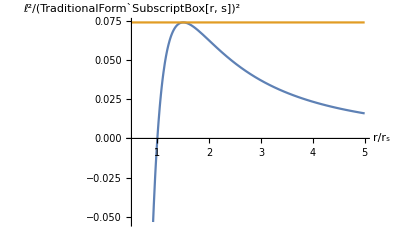

```mathematica
Plot[{FullSimplify[SchwarzschildNullPE[ρ](rs^2/ℓ^2)],2/27},{ρ,0.5,5},AxesLabel->{"r/r_s","ℓ^2/(TraditionalForm`SubscriptBox[r, s])^2"}]
```

Schwarzschild Horizon

For r > r_s,  ⟨∂_t |∂_t⟩ = g_00>0 and ⟨∂_r |∂_r⟩ = g_rr<0; whereas for r < r_s, ⟨∂_t |∂_t⟩ = g_00<0 and ⟨∂_r |∂_r⟩ = g_rr>0.

```mathematica
ToExpressionForm[gSchwarzschild]
```

(r (ⅆr)^2)/(-r+rs)+(1-rs/r) (ⅆt)^2-r^2 (ⅆθ)^2-r^2 (ⅆϕ)^2 Sin[θ]^2

This tells us the meaning of the coordinates (t, r) changes when crossing the r = r_s surface. For r > r_s, t is the timelike coordinate while r is a spatial one; but for r < r_s, r becomes the timelike coordinate while t is now a spatial one. In particular, going forward in time when  r < r_s, means r is decreasing from r_s to 0^+.

We may refer back to both the conservation law and the plot of the “potential” experienced by null geodesics. As long as E^2/2 is large enough, it would appear as though the r[λ] trajectory can decrease from large positive values all the way to 0^+; or increase from very small values, less than r_s, to very large ones. However, while r can decrease past r_s with time moving forward; to go climb out of the r < r_s portion of the “potential well” would correspond to traveling back in time. This is the primary obstacle preventing all future-pointing geodesics — even null ones — from getting out of the r = r_s surface from r < r_s to r > r_s. This r = r_s surface is dubbed the horizon.

Schwarzschild — Radial Affinely Parametrized Null Geodesic

Notice the potential is strictly non-negative for r ≥ r_s. Because kinetic plus potential = Ε^2/2 ≥ 0 — it is also strictly non-negative — that means, for a given pair of (E, ℓ), kinetic energy is maximized by setting angular momentum to zero. In turn, this leads us to the solution to the affinely parametrized radial null geodesics.

```mathematica
(drdλ/.ℓ->0)//FullSimplify[#,{r[λ]≥rs>0,Ε≥0}]&
(((geodesicSchwarzschild⟦3⟧/.geodesicConstantsSchwarzschild)/.{ℓ->0,r->Function[{λ},σE Ε λ+C[1]]})//FullSimplify)/.{σE^2->1}
```

{r'[λ]→Ε,r'[λ]→-Ε}

{True,True,True,True}

Schwarzschild — Radial Null Geodesic Vector Field

Let us solve for the radial null geodesic vector field q^μ by first superposing ∂_t  and ∂_r .

```mathematica
qNull[μ_]:=Module[{α}, MoveIndices[
NonMetricTensor[{SuperMinus[α]},(1-rs/r)^-1 σt{1,0,0,0}+σr{0,1,0,0},"q",Coordinates->{t,r,θ,ϕ}],{μ},gSchwarzschild]];
```

For q to be null, we see that σt^2 = σr^2.

```mathematica
σRules={σt^2->1,σr^2->1};
((qNull[SuperMinus[μ]]qNull[SubMinus[μ]]//ContractTensors))//FullSimplify
((qNull[SuperMinus[μ]]qNull[SubMinus[μ]]//ContractTensors)//.σRules)//FullSimplify
```

(r (-σr^2+σt^2))/(r-rs)

0

To justify why the σ’s are constants, let us verify that the result also solves the geodesic equation q^σ∇_σ q^α = 0.

```mathematica
(((qNull[SuperMinus[σ]]CovariantD[SubMinus[σ],qNull[SuperMinus[α]],gSchwarzschild])//ContractTensors)//FullSimplify)/.σRules
%//ZeroTensorQ
```

(q⊗∇q)σ̲

σ̲α

True

These radial null geodesics turn out to be the gradient of some scalar u by the Poincare lemma, because the exterior derivative of their corresponding 1-form is zero.

```mathematica
Subscript[ⅆ, SubMinus[α]] qNull[SubMinus[β]]
%//ZeroTensorQ
```

(ⅆq)
α
β

True

To solve for u such that (ⅆu)_β = q_β, we invoke PotentialForm.

```mathematica
scalaru=NonMetricTensor[{},Normal[PotentialForm[qNull[SubMinus[β]]]]/.{-rs Log[rs]+rs Log[-r+rs]->rs Log[Abs[1-r/rs]]},"u",Coordinates->{t,r,θ,ϕ}]
```

u

This leads us to null coordinates 
		 x^± ≡ t  ± (r + r_s Log|1-r/rs|)
for the (t,r)-sub metric of the Schwarzschild geometry; specifically,
		(1 - r_s/r) ⅆx^+ⅆx^- = (1 - r_s/r)  (ⅆt)^2 - (ⅆr)^2/(1 - r_s/r) .

ExteriorD[τ_Tensor] can also be entered as ⅆτ, whereby the extra index would be generated by TensoriaCalc.

```mathematica
XP=scalaru/.{σt->1,σr->1,"u"->"x^+"}
XM=scalaru/.{σt->1,σr->-1,"u"->"x^-"}
FullSimplify[(1-rs/r)ToExpressionForm[ⅆXP]ToExpressionForm[ⅆXM],{r>rs}]
FullSimplify[(1-rs/r)ToExpressionForm[ⅆXP]ToExpressionForm[ⅆXM],{r<rs}]
```

x^+

x^-

-((r (ⅆr)^2)/(r-rs))+((r-rs) (ⅆt)^2)/r

-((r (ⅆr)^2)/(r-rs))+((r-rs) (ⅆt)^2)/r

Weak Field Light Deflection

Consider a high frequency photon approaching the Sun from infinity, making its closest approach at r = b, before flying off to infinity again. Let us now use the above geodesic dynamics to solve for its net deflection angle. The Sun is a weak gravity source in that r_s/r ≪ 1 — the Schwarzschild radius r_s of the Sun is ~3km, much smaller than its physical radius of 7X10^5km (see below) — allowing us to expand in powers of r_s, the shortest length scale of the problem at hand.

But, first, we note that dϕ/dr is related to dr/dλ and r itself via the following relation:

```mathematica
dϕdr=(((ϕ'[λ]/.geodesicConstantsSchwarzschild)==D[ϕ[r[λ]],λ])/.{ϕ'[r[λ]]->ϕ'[r]})//Flatten[Solve[#,ϕ'[r]]]&
```

{ϕ'[r]→ℓ/(r[λ]^2 r'[λ])}

If we focus on the incoming portion of the trajectory, r’[λ] ≤ 0 because the radius is decreasing from infinity to b. Imposing the null Lagrangian condition to replace r’[λ] then yields the following.

```mathematica
dϕdr=(dϕdr/.drdλ⟦2⟧)//FullSimplify[#,{r[λ]>rs>0}]&
dϕdr=dϕdr/.1/(√(-r[λ] (rs ℓ^2-ℓ^2 r[λ]+Ε^2 r[λ]^3)))->1/(I √(r[λ] (rs ℓ^2-ℓ^2 r[λ]+Ε^2 r[λ]^3)))
```

{ϕ'[r]→-ℓ/(√(r[λ] (rs ℓ^2-ℓ^2 r[λ]+Ε^2 r[λ]^3)))}

{ϕ'[r]→-(ℓ/(√(r[λ] (rs ℓ^2-ℓ^2 r[λ]+Ε^2 r[λ]^3))))}

This means we may integrate this expression for dϕ/dr with respect to r to obtain Δϕ, the total change in azimuthal angle.

Now, since r = b is the closest approach, dr/dλ = 0 there. This allows us to solve ℓ for b. Following which, we employ it in dϕ/dr and expand in powers of r_s.

```mathematica
Solve[geodesicNullSchwarzschild/.{r[λ]->b,r'[λ]->0},ℓ]
((dϕdr/.%⟦2⟧)/.r[λ]->r)//FullSimplify[#,{r>b>rs>0,Ε>0}]&;
dϕdr=FullSimplify[Series[ϕ'[r]/.%,{rs,0,1}],{r>b>rs>0}]
```

{{ℓ→-(b^(3/2) Ε)/(√(b-rs))},{ℓ→(b^(3/2) Ε)/(√(b-rs))}}

-(b/(r √(-b^2+r^2)))+((b^3-r^3) rs)/(2 r^2 (-b^2+r^2)^(3/2))+O[rs]^2

Integrating over r ∈ {∞, b}, describing the photon coming in from infinity and reaching r = b.

```mathematica
Assuming[{b>rs>0},Integrate[#,{r,∞,b}]]&/@Normal[dϕdr]
```

π/2+rs/b

The total change in azimuthal angle is therefore twice of this — namely, the sum of the contribution from both the incoming and outgoing legs: Δϕ = π + 2 r_s/b. Had there been no gravity at all, the photon would sweep out a straight line and Δϕ = π. Therefore, the deflection angle is 2r_s/b. Recalling r_s≡2 G_N M_Sun and setting b to be the physical radius of the Sun — see below — we obtain a value of 1.75 arc seconds.

```mathematica
{ Entity["PhysicalConstant","GravitationalConstant"]["Value"],Entity["Star","Sun"][EntityProperty["Star","Mass"]],Entity["Star","Sun"][EntityProperty["Star","Radius"]]}
```

{6.674×10^-11 m^3/(kg s^2),1.99×10^30 kg,695700. km}

We use speed of light = 299,792,458 meters/second = 1 to convert 2r_s/b → 4 G_N M_Sun/R_radius to arc-seconds.

```mathematica
4 Entity["PhysicalConstant","GravitationalConstant"]["Value"]Entity["Star","Sun"][EntityProperty["Star","Mass"]]/Entity["Star","Sun"][EntityProperty["Star","Radius"]]
(((%/.Quantity->Times)/.{"Meters"->m,"Seconds"->s,"Kilometers"->km,"Miles"->1.60934 km})/.cRule);
%/(2Pi)(360 60 60 arcseconds)
```

763000. km^2/s^2

1.75 arcseconds

Rotating Black Holes: Kerr Solution

The Kerr metric describes a rotating black hole satisfying the vacuum Einstein’s equations G_αβ=0 with zero cosmological constant.

```mathematica
ΣΔRules={Σ->r^2+a^2 Cos[θ]^2,Δ->r^2-rs r+a^2};
gKerr=((1-(rs r)/Σ)(ⅆt)^2-(Σ/Δ)(ⅆr)^2-Σ (ⅆθ)^2-(r^2+a^2+((rs r a^2)/Σ)Sin[θ]^2)Sin[θ]^2(ⅆϕ)^2-2rs r a (Sin[θ]^2/Σ)ⅆt ⅆϕ)/.ΣΔRules
```

-((r^2+a^2 Cos[θ]^2) (ⅆr)^2)/(a^2+r^2-r rs)+(1-(r rs)/(r^2+a^2 Cos[θ]^2)) (ⅆt)^2-(r^2+a^2 Cos[θ]^2) (ⅆθ)^2-(2 a r rs ⅆt ⅆϕ Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)-(ⅆϕ)^2 Sin[θ]^2 (a^2+r^2+(a^2 r rs Sin[θ]^2)/(r^2+a^2 Cos[θ]^2))

It turns out that Computer Algebra does not handle trigonometric functions efficiently, so to verify Einstein’s equations we shall switch from θ to χ ≡ cos θ.

```mathematica
θToχRule={t->t,r->r,θ->ArcCos[χ],ϕ->ϕ};
ΣΔRules=ΣΔRules/.CoordinateTransformation[θToχRule,{t,r,χ,ϕ}];
gKerr=gKerr/.CoordinateTransformation[θToχRule,{t,r,χ,ϕ}]
gKerr=Metric[SubMinus[α],SubMinus[β],gKerr,Coordinates->{t,r,χ,ϕ}];
```

-((r^2+a^2 χ^2) (ⅆr)^2)/(a^2+r^2-r rs)+(1-(r rs)/(r^2+a^2 χ^2)) (ⅆt)^2-(2 a r rs (1-χ^2) ⅆt ⅆϕ)/(r^2+a^2 χ^2)-(1-χ^2) (a^2+r^2+(a^2 r rs (1-χ^2))/(r^2+a^2 χ^2)) (ⅆϕ)^2-((r^2+a^2 χ^2) (ⅆχ)^2)/(1-χ^2)

The Einstein tensor is indeed zero.

```mathematica
Einstein[SuperMinus[α],SubMinus[β],gKerr]
%//ZeroTensorQ
```

Gα

β

True

Kerr Isometries

The Kerr metric enjoys time t- and rotation ϕ-translation symmetry. The associated Killing vectors are as follows.

```mathematica
KerrU=NonMetricTensor[{SuperMinus[α]},{1,0,0,0},"U",Coordinates->{t,r,χ,ϕ}]
```

Uα

```mathematica
Kerrϕ=NonMetricTensor[{SuperMinus[α]},{0,0,0,1},"J",Coordinates->{t,r,χ,ϕ}]
```

Jα

Let us verify their Killing equations.

```mathematica
{LieD[KerrU,gKerr],LieD[Kerrϕ,gKerr]}
(ZeroTensorQ/@%)
```

{(£
Ug)
α
β,(£
Jg)
α
β}

{True,True}

What is less obvious is the existence of a Killing tensor K_μν defined by ∇_({α) K_(μν}) = 0 — if q^μ were tangent to some geodesic worldline, obeying q^σ∇_σ q^α=0, we may then construct the conserved quantity K_μν q^μ q^ν.

First we define the two vectors ℓ and n.

```mathematica
ℓKerr=NonMetricTensor[{SuperMinus[μ]},{(r^2+a^2)/Δ,-1,0,-(a/Δ)}/.ΣΔRules,"ℓ",Coordinates->{t,r,χ,ϕ}]
```

ℓμ

```mathematica
nKerr=NonMetricTensor[{SuperMinus[ν]},{(r^2+a^2)/(2Σ),Δ/(2Σ),0,-(a/(2Σ))}/.ΣΔRules,"n",Coordinates->{t,r,χ,ϕ}]
```

nν

The Killing tensor itself is then the following object.

```mathematica
KillingTKerr= (Σ (ℓKerr nKerr+((ℓKerr nKerr)/.{μ->ν,ν->μ}))-r^2 Metric[SuperMinus[μ],SuperMinus[ν],gKerr])/.ΣΔRules
```

(r^2+a^2 χ^2) (nμ
 ℓν
+ℓμ
 nν
)-r^2 gμ
ν

The key property is that the fully symmetrized first covariant derivative of the Killing tensor is zero.

```mathematica
Symmetrize[TensorComponents[CovariantD[SuperMinus[α],KillingTKerr,gKerr]],Symmetric[{1,2,3}]]
(%//Normal)//FullSimplify
```

SymmetrizedArray[…]

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

Kerr — Geometric Curvature

The “square” of the Kerr Riemann tensor reads as follows. Geometric curvature blows up on a “ring” defined by r = 0 and χ = cos θ = 0 (i.e., θ = π/2).

```mathematica
(Riemann[SubMinus[α],SubMinus[β],SubMinus[μ],SubMinus[ν],gKerr]Riemann[SuperMinus[α],SuperMinus[β],SuperMinus[μ],SuperMinus[ν],gKerr]//ContractTensors)//FullSimplify
```

(12 rs^2 (r^6-15 a^2 r^4 χ^2+15 a^4 r^2 χ^4-a^6 χ^6))/((r^2+a^2 χ^2)^6)

Since Kerr is a vacuum spacetime, its Weyl and Riemann tensors are the same.

```mathematica
(Weyl[SubMinus[α],SubMinus[β],SubMinus[μ],SubMinus[ν],gKerr]Weyl[SuperMinus[α],SuperMinus[β],SuperMinus[μ],SuperMinus[ν],gKerr]//ContractTensors)//FullSimplify
```

(12 rs^2 (r^6-15 a^2 r^4 χ^2+15 a^4 r^2 χ^4-a^6 χ^6))/((r^2+a^2 χ^2)^6)

We may also examine the individual Riemann tensor components in an orthonormal basis. We shall use the following inverse orthonormal frame fields; notice they are no longer simply the straightforward “square root” of the metric, because the latter is now non-diagonal — in particular, there is mixing between the (t, ϕ)-components.

```mathematica
Clear[εKerr];
θχRule=CoordinateTransformation[{θ->ArcCos[χ]},{χ}]
εKerr[0]=((1/(Sqrt[Σ Δ]/.ΣΔRules))((r^2+a^2)Del[t]-a Del[ϕ]))/.θχRule;
εKerr[1]=((Δ/Σ/.ΣΔRules)^(1/2)Del[r])/.θχRule;
εKerr[2]=((1/(Σ/.ΣΔRules)^(1/2))Del[θ])/.θχRule;
εKerr[3]=((1/((Σ/.ΣΔRules)^(1/2)Sin[θ]))(a Sin[θ]^2 Del[t]-Del[ϕ]))/.θχRule;
εKerrTable=Module[{α},Table[Coefficient[εKerr[α],#]&/@{Del[t],Del[r],Del[χ],Del[ϕ]},{α,0,3}]]
```

{ⅆθ→-ⅆχ/(√(1-χ^2)),θ→ArcCos[χ],∇θ→-√(1-χ^2) ∇χ}

{{(a^2+r^2)/(√((a^2+r^2-r rs) (r^2+a^2 χ^2))),0,0,-(a/(√((a^2+r^2-r rs) (r^2+a^2 χ^2))))},{0,√((a^2+r^2-r rs)/(r^2+a^2 χ^2)),0,0},{0,0,-((√(1-χ^2))/(√(r^2+a^2 χ^2))),0},{(a √(1-χ^2))/(√(r^2+a^2 χ^2)),0,0,-(1/(√(1-χ^2) √(r^2+a^2 χ^2)))}}

We append them to gKerr using OrthonormalFrameField. Given a set of orthonormal frame fields (or, its inverse) and a FlatMetric, TensoriaCalc would automatically compute the inverse orthonormal frame fields (or, the orthonormal frame fields) before storing both sets of frame fields into the metric Tensor object.

```mathematica
gKerr=OrthonormalFrameField[gKerr,InverseOrthonormalFrameField->εKerrTable,FlatMetric->{1,-1,-1,-1},OrthonormalFrameFieldIndices->{α̂,β}]
```

g
α
β

The inverse orthonormal frame fields should recover the inverse metric in the following manner.

```mathematica
(εKerr[0]^2-εKerr[1]^2-εKerr[2]^2-εKerr[3]^2)//FullSimplify
(ToExpressionForm[Metric[SuperMinus[α],SuperMinus[β],gKerr]]-%)//FullSimplify
```

(-(a^2+r (r-rs)) (∇r)^2+((a (-1+χ^2) ∇t+∇ϕ)^2)/(-1+χ^2)+(((a^2+r^2) ∇t-a ∇ϕ)^2)/(a^2+r (r-rs))+(-1+χ^2) (∇χ)^2)/(r^2+a^2 χ^2)

0

OrthonormalFrameFieldQ allows us to carry out this verification for both the orthonormal frame fields and their inverses; that they do indeed recover, respectively, the metric and its inverse:
		η_(α̂ β̂) (ε^(α̂))_μ (ε^(β̂))_ν = g_μν	
and		η^(α̂ β̂) (ε_(α̂))^μ (ε_(β̂))^ν = g^μν.
If both of these two equations return True, OrthonormalFrameFieldQ will return a single True. If one or both of them does not return True, a List of these two sets of equations would be displayed.

```mathematica
OrthonormalFrameFieldQ[gKerr]
```

True

Let us now examine the Kerr R_(OverHat[0]î OverHat[0]ĵ) components.

```mathematica
RiemannKerr[μ_,ν_,σ_,ρ_]:=MoveIndices[Module[{α1,α2,α3,α4},Riemann[SuperMinus[α1],SubMinus[α2],SubMinus[α3],SubMinus[α4],gKerr]],{μ,ν,σ,ρ},gKerr];
RiemannKerrdOrtho=RiemannKerr[SubMinus[OverHat[0]],SubMinus[ν̂],SubMinus[OverHat[0]],SubMinus[β̂]];
```

```mathematica
KerrAssumptions={-1<χ<1,0<θ<Pi,0<ϕ<2Pi,r>0};
Flatten[Table[Which[(* By symmetry, we do not need the lower triangular components *)ν<β,Nothing,RiemannKerrdOrtho===0,Nothing,True,Row[{"R",Column[{Null,OverHat[0]}],Column[{Null,ν̂}],Column[{Null,OverHat[0]}],Column[{Null,β̂}]}]->Simplify[RiemannKerrdOrtho,KerrAssumptions]],{ν,1,3},{β,1,3}]]
```

{R
OverHat[0]
OverHat[1]
OverHat[0]
OverHat[1]→1/2 r rs (((a^2+r^2) (-r^4+2 a^2 r^2 χ^2+3 a^4 χ^4) (a^2 (3 a^2+r (3 r-2 rs)) (-1+χ^2) √(-(a^2+r (r-rs)) (-1+χ^2) (r^2+a^2 χ^2))+(a^2+r^2) √(r^2+a^2 χ^2) (2 r (-r+rs)+a^2 (-3+χ^2))))/((a^2+r (r-rs)) (r^2+a^2 χ^2)^(13/2))+a^2 (-((a^2+r^2) (3 a^2+r (3 r-2 rs)) (1-χ^2)^(3/2) (-r^2+3 a^2 χ^2))/((r^2+a^2 χ^2)^(9/2) √((a^2+r (r-rs)) (r^2+a^2 χ^2)))+1/((r^2+a^2 χ^2)^5)(-1+χ^2)^2 (r^2-3 a^2 χ^2) (r^4+a^4 (3-2 χ^2)-2 a^2 r (rs-rs χ^2+r (-2+χ^2))))),R
OverHat[0]
OverHat[2]
OverHat[0]
OverHat[1]→(3 a^2 (a^2+r^2) rs χ (-3 r^2+a^2 χ^2) √((a^2+r^2-r rs)/(r^2+a^2 χ^2)) (a^4 (-1+χ^2)^2 √(-(-1+χ^2) (r^2+a^2 χ^2))+r^2 (√((a^2+r^2-r rs) (r^2+a^2 χ^2))-χ^2 √((a^2+r^2-r rs) (r^2+a^2 χ^2))+√(-(-1+χ^2) (r^2+a^2 χ^2)))+a^2 (2 √((a^2+r^2-r rs) (r^2+a^2 χ^2))+√(-(-1+χ^2) (r^2+a^2 χ^2))+r^2 √(-(-1+χ^2) (r^2+a^2 χ^2))-r rs √(-(-1+χ^2) (r^2+a^2 χ^2))+χ^4 (√((a^2+r^2-r rs) (r^2+a^2 χ^2))+r^2 √(-(-1+χ^2) (r^2+a^2 χ^2))-r rs √(-(-1+χ^2) (r^2+a^2 χ^2)))+χ^2 (-3 √((a^2+r^2-r rs) (r^2+a^2 χ^2))-2 r^2 √(-(-1+χ^2) (r^2+a^2 χ^2))+2 r rs √(-(-1+χ^2) (r^2+a^2 χ^2))))))/(2 (a^2+r (r-rs)) (r^2+a^2 χ^2)^5),R
OverHat[0]
OverHat[2]
OverHat[0]
OverHat[2]→1/2 r rs (-(((a^2+r^2) (a^2 (3 a^2+r (3 r-rs)) (1-χ^2)^(3/2) √((a^2+r (r-rs)) (r^2+a^2 χ^2)) (r^4-2 a^2 r^2 χ^2-3 a^4 χ^4)+(a^2+r^2) √(r^2+a^2 χ^2) (-r^4+2 a^2 r^2 χ^2+3 a^4 χ^4) (r (-r+rs)+a^2 (-3+2 χ^2))))/((a^2+r (r-rs)) (r^2+a^2 χ^2)^(13/2)))+a^2 (-r^2+3 a^2 χ^2) (((a^2+r^2) (3 a^2+r (3 r-rs)) (1-χ^2)^(3/2))/((r^2+a^2 χ^2)^(9/2) √((a^2+r (r-rs)) (r^2+a^2 χ^2)))-((-1+χ^2)^2 (-2 r^4+a^4 (-3+χ^2)+a^2 r (rs-rs χ^2+r (-5+χ^2))))/((r^2+a^2 χ^2)^5))),R
OverHat[0]
OverHat[3]
OverHat[0]
OverHat[3]→-(r rs (r^2-3 a^2 χ^2))/(2 (r^2+a^2 χ^2)^3)}

## History of TensoriaCalc

The zeroth version of TensoriaCalc was written by Yi-Zen Chu during the 2010’s. For his Master’s thesis project in the early 2020’s, Wei-Hao Chen substantially expanded upon the functionality of TensoriaCalc; and this current version was the result of his work. Vaidehi Varma worked with Wei-Hao Chen and Yi-Zen Chu to document the code and write the accompanying manual, which shall be released shortly.